# Scattering processes @ Muon collider

David Marzocca - March 2025

```mathematica
(*Quit[]*)
```

## Introduction

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/manuelmorales/learning_bayes

```mathematica
<<FixPolygons.m
```

Get::noopen: Cannot open FixPolygons.m.

$Failed

### Definitions

1 dof

```mathematica
χSQ1d68=InverseCDF[ChiSquareDistribution[1],0.68]
```

0.988946

```mathematica
χSQ1d90=InverseCDF[ChiSquareDistribution[1],0.90]
```

2.70554

```mathematica
χSQ1d95=InverseCDF[ChiSquareDistribution[1],0.95]
```

3.84146

```mathematica
√χSQ1d95
```

1.95996

```mathematica
χSQ1d99=InverseCDF[ChiSquareDistribution[1],0.997]
```

8.80747

2 dof

```mathematica
χSQ2d68=InverseCDF[ChiSquareDistribution[2],0.68]
```

2.27887

```mathematica
χSQ2d95=InverseCDF[ChiSquareDistribution[2],0.95]
```

5.99146

```mathematica
χSQ2d99=InverseCDF[ChiSquareDistribution[2],0.997]
```

11.6183

```mathematica
TeV=10^3;
GeV=1;
MeV=10^-3;
keV=10^-6;
eV=10^-9;
```

```mathematica
mμ=105.6584 MeV;
me=511.0 keV;
```

Costante per passare da Gev^{-2} a pb

```mathematica
Gevtopb=0.3894 10^9;
Gevtofb=10^3 Gevtopb;
```

```mathematica
SMpoint={Cc[_,_]->0,Cc[_,_,_,_]->0,Cc[_,_,_]->0,Ccq[_,_]->0,Ccq1[_,_]->0,Clequ1[_,_,_,_]->0,Clequ3[_,_,_,_]->0,Cledq[_,_,_,_]->0,Ccq3[_,_]->0,ϵZp->0,gZpq[qb_,q_]->0,gZpl[l_]->0,
CeB[_,_]->0,
CeW[_,_]->0,
CdB[_,_]->0,
CdW[_,_]->0,
CuB[_,_]->0,
CuW[_,_]->0,
Ceγ[_,_]->0,
CeZ[_,_]->0,
Cdγ[_,_]->0,
CdZ[_,_]->0,
Cuγ[_,_]->0,
CuZ[_,_]->0};
```

```mathematica
SMpointSMEFT={Clq1[_,_,_,_]->0,
Clq3[_,_,_,_]->0,
Ceu[_,_,_,_]->0,
Ced[_,_,_,_]->0,
Clu[_,_,_,_]->0,
Cld[_,_,_,_]->0,
Cqe[_,_,_,_]->0,
Cledq[_,_,_,_]->0,
Clequ1[_,_,_,_]->0,
Clequ3[_,_,_,_]->0,
CeB[_,_]->0,
CeW[_,_]->0,
CdB[_,_]->0,
CdW[_,_]->0,
CuB[_,_]->0,
CuW[_,_]->0};
```

### RG-evolved SM couplings

SM β functions

```mathematica
βyt[μ_]:=yt[μ]/(16 π^2)(9/2 yt[μ]^2-8 gs[μ]^2-9/4 g[μ]^2-17/12 gp[μ]^2);
βgp[μ_]:=gp[μ]^3/(16 π^2)41/6;
βg[μ_]:=g[μ]^3/(16 π^2)(-19/6);
βgs[μ_]:=gs[μ]^3/(16 π^2)(-7);
βλ[μ_]:=1/(16 π^2)(24 λ[μ]^2-6 yt[μ]^4+3/8(2 g[μ]^4+(g[μ]^2+gp[μ]^2)^2))
βlnv[μ_]:=1/(16 π^2)(3/4(gp[μ]^2+3 g[μ]^2)-3 yt[μ]^2);
βlnvsq[μ_]:=2βlnv[μ];
```

As inputs we use the values at 200GeV from [2211.08576]

```mathematica
gs0=1.1525;
g0=0.646832;
gp0=0.358851;
```

```mathematica
NumValues={
Nc->3,
Qe->-1,Qu->2/3,Qd->-1/3,Qν->0,
Ye->-1,Yl->-1/2,Yq->1/6,Yu->2/3,Yd->-1/3,YH->1/2,YS1->1/3,YS3->1/3,
v->246.22,mZ->91.1876,ΓZ->2.4952,mW->80.3524,ΓW->2.085,Vcb->0.0405,Vub->3.82 10^-3,Vus->0.2243,Vcd->0.221};
```

```mathematica
Clear[g,gp]
```

```mathematica
g[μ_]=g[μ]/.DSolve[{μ D[g[μ],μ]==βg[μ],g[200GeV]==g0},g,{μ,80,10^10}][[1,1]]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

4.99337/(√(54.2959+Log[μ]))

```mathematica
DSolve[{μ D[gp[μ],μ]==βgp[μ],gp[200GeV]==gp0},gp,{μ,90,10^10}]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

$RecursionLimit::areclim: Recursion depth of 1024 exceeded during evaluation with assumptions.

{{gp→Function[{μ},-3.39921/(√(95.0265-Log[μ]))]}}

```mathematica
gp[μ_]=-gp[μ]/.%[[1]]
```

3.39921/(√(95.0265-Log[μ]))

```mathematica
{g[10TeV],gp[10TeV]}
```

{0.626593,0.366939}

```mathematica
ggp[μ_]=√(g[μ]^2+gp[μ]^2)//Simplify
```

√((-2996.74+13.3791 Log[μ])/((-95.0265+Log[μ]) (54.2959+Log[μ])))

```mathematica
sWSQ[μ_]=gp[μ]^2/(g[μ]^2+gp[μ]^2)//Simplify
```

(46.8919+0.863636 Log[μ])/(223.987-1. Log[μ])

```mathematica
e[μ_]=(g[μ]gp[μ])/(√(g[μ]^2+gp[μ]^2))//Simplify
```

16.9735/(√(-1. (-95.0265+Log[μ]) (54.2959+Log[μ])) √((-2996.74+13.3791 Log[μ])/((-95.0265+Log[μ]) (54.2959+Log[μ]))))

```mathematica
α[μ_]=e[μ]^2/(4π)//Simplify
```

1.7136/(223.987-1. Log[μ])

```mathematica
α[91]^-1
```

128.079

```mathematica
α[10TeV]^-1
```

125.337

### Fermion Charges

```mathematica
id[uL]=11;
id[cL]=12;
id[tL]=13;
id[uR]=14;
id[cR]=15;
id[tR]=16;

id[dL]=21;
id[sL]=22;
id[bL]=23;
id[dR]=24;
id[sR]=25;
id[bR]=26;
```

```mathematica
Clear[Cas]
```

```mathematica
(* SU(2) Casimir *)
Cas[i_]=0;
Cas[eL]=Cas[μL]=Cas[τL]=1/2(1/2+1);
Cas[νe]=Cas[νμ]=Cas[ντ]=1/2(1/2+1);
Cas[dL]=Cas[sL]=Cas[bL]=1/2(1/2+1);
Cas[uL]=Cas[cL]=Cas[tL]=1/2(1/2+1);
```

```mathematica
Y[eL]=Y[μL]=Y[τL]=-1/2;
Y[νe]=Y[νμ]=Y[ντ]=-1/2;
Y[dL]=Y[sL]=Y[bL]=1/6;
Y[uL]=Y[cL]=Y[tL]=1/6;
Y[eR]=Y[μR]=Y[τR]=-1;
Y[dR]=Y[sR]=Y[bR]=-1/3;
Y[uR]=Y[cR]=Y[tR]=2/3;
```

```mathematica
Q[uL]=Q[uR]=Q[cL]=Q[cR]=Q[tL]=Q[tR]=2/3;
Q[dL]=Q[dR]=Q[sL]=Q[sR]=Q[bL]=Q[bR]=-1/3;
Q[μL]=Q[μR]=Q[eL]=Q[eR]=Q[τL]=Q[τR]=-1;
```

```mathematica
gz[eL]=gz[μL]=gz[τL]=ggp[μ](-1/2-Q[eL]sWSQ[μ]);
gz[eR]=gz[μR]=gz[τR]=ggp[μ](-Q[eL]sWSQ[μ]);

gz[uL]=gz[cL]=gz[tL]=ggp[μ](1/2-Q[uL]sWSQ[μ]);
gz[uR]=gz[cR]=gz[tR]=ggp[μ](-Q[uR]sWSQ[μ]);
gz[dL]=gz[sL]=gz[bL]=ggp[μ](-1/2-Q[dL]sWSQ[μ]);
gz[dR]=gz[sR]=gz[bR]=ggp[μ](-Q[dR]sWSQ[μ]);
```

```mathematica
{KroneckerDelta[id[uL],id[uL]],KroneckerDelta[id[uL],id[dL]]}
```

{1,0}

```mathematica
(* Chiralities *)
idL=-1;
idR=+1;
```

```mathematica
Kδ[a_,b_]:=KroneckerDelta[a,b]
```

```mathematica
{KroneckerDelta[idL,idL],KroneckerDelta[idL,idR],KroneckerDelta[idR,idR],KroneckerDelta[idR,idL]}
```

{1,0,1,0}

```mathematica
gZμ[idL]=ggp[μ](-1/2-Q[eL]sWSQ[μ]);
gZμ[idR]=ggp[μ](-Q[eL]sWSQ[μ]);
```

```mathematica
gZpμ[idL]=gZpμL;
gZpμ[idR]=gZpμR;
```

```mathematica
PartTOchID[μL]=idL;
PartTOchID[μLb]=idL;
PartTOchID[μR]=idR;
PartTOchID[μRb]=idR;
```

```mathematica
gen[uL]=1;
gen[dL]=1;
gen[cL]=2;
gen[sL]=2;
```

### pseudorapidity

```mathematica
ηθ[θ_]=-Log[Tan[θ/2]];
```

```mathematica
θη[η_]=2ArcTan[Exp[-η]];
```

```mathematica
dθdη[η_]=D[θη[η],η]
```

-(2 ⅇ^-η)/(1+ⅇ^(-2 η))

```mathematica
θη[3]
```

2 ArcTan[1/ⅇ^3]

```mathematica
dcθdθ[θ_]=D[Cos[θ],θ]
```

-Sin[θ]

```mathematica
θη[η_]=2ArcTan[Exp[-η]];
```

```mathematica
θη[2.4]/Degree
```

10.3671

```mathematica
Cos[θη[2.4]]
```

0.983675

```mathematica
CosθMax=Cos[20.Degree]
```

0.939693

```mathematica
ηMax=ηθ[20.Degree]
```

1.73542

### MuC luminosities

Luminosity in fb^-1

```mathematica
Lumi3TeV=1 10^3; (*1: conservative luminosity for a 3TeV μ collider from 2103.14043, Tab.1. is delayed*) (* From the Muon Collider report for ESPPU 2025 *)
```

```mathematica
(*Lumi3TeV=2 10^3;  (*Assuming that the 3TeV MuC could run for longer if there is a delay on the 10TeV.. *)*)
```

```mathematica
Lumi7TeV=10 10^3; (* For the 7.6 TeV collider, from the Muon Collider report for ESPPU 2025 *)
```

```mathematica
Lumi10TeV=10 10^3; (*conservative luminosity for a 10TeV μ collider from 2103.14043, Tab.1*)
```

```mathematica
Lumi14TeV=20 10^3; (*conservative luminosity for a 14TeV μ collider from 2103.14043, Tab.1*)
```

```mathematica
Lumi30TeV=90 10^3; (* optimistic luminosity for a 30TeV μ collider from 2103.14043, Tab.1*)
```

### LogTicks

```mathematica
logBase=E;
FrameLogTicks={{Log[logBase,0.001], "0.001"},{Log[logBase,0.002], ""},{Log[logBase,0.003], ""},{Log[logBase,0.004], ""},{Log[logBase,0.005], ""},{Log[logBase,0.006], ""},{Log[logBase,0.007], ""},{Log[logBase,0.008], ""},{Log[logBase,0.009], ""},
{Log[logBase,0.01],"0.01"},{Log[logBase,0.02],""},{Log[logBase,0.03],""},{Log[logBase,0.04],""},{Log[logBase,0.05], ""},{Log[logBase,0.06], ""},{Log[logBase,0.07], ""},{Log[logBase,0.08], ""},{Log[logBase,0.09], ""},
{Log[logBase,0.1],"0.1"},{Log[logBase,0.2],""},{Log[logBase,0.3],""},{Log[logBase,0.4],""},{Log[logBase,0.5], ""},{Log[logBase,0.6], ""},{Log[logBase,0.7], ""},{Log[logBase,0.8], ""},{Log[logBase,0.9], ""},
{Log[logBase,1],"1"},{Log[logBase,2],""},{Log[logBase,3],""},{Log[logBase,4],""},{Log[logBase,5], ""},{Log[logBase,6], ""},{Log[logBase,7], ""},{Log[logBase,8], ""},{Log[logBase,9], ""},{Log[logBase,10],"10"},{Log[logBase,20], ""},{Log[logBase,30], ""},{Log[logBase,40], ""},{Log[logBase,50], ""},{Log[logBase,60], ""},{Log[logBase,70], ""},{Log[logBase,80], ""},{Log[logBase,90], ""},{Log[logBase,100], "100"},{Log[logBase,200], ""},{Log[logBase,300], ""},{Log[logBase,400], ""},{Log[logBase,500], ""},{Log[logBase,600], ""},{Log[logBase,700], ""},{Log[logBase,800], ""},{Log[logBase,900], ""},{Log[logBase,1000], "1000"}};

FrameLogTicksNoText={{Log[logBase,0.001], ""},{Log[logBase,0.002], ""},{Log[logBase,0.003], ""},{Log[logBase,0.004], ""},{Log[logBase,0.005], ""},{Log[logBase,0.006], ""},{Log[logBase,0.007], ""},{Log[logBase,0.008], ""},{Log[logBase,0.009], ""},
{Log[logBase,0.01],""},{Log[logBase,0.02],""},{Log[logBase,0.03],""},{Log[logBase,0.04],""},{Log[logBase,0.05], ""},{Log[logBase,0.06], ""},{Log[logBase,0.07], ""},{Log[logBase,0.08], ""},{Log[logBase,0.09], ""},
{Log[logBase,0.1],""},{Log[logBase,0.2],""},{Log[logBase,0.3],""},{Log[logBase,0.4],""},{Log[logBase,0.5], ""},{Log[logBase,0.6], ""},{Log[logBase,0.7], ""},{Log[logBase,0.8], ""},{Log[logBase,0.9], ""},
{Log[logBase,1],""},{Log[logBase,2],""},{Log[logBase,3],""},{Log[logBase,4],""},{Log[logBase,5], ""},{Log[logBase,6], ""},{Log[logBase,7], ""},{Log[logBase,8], ""},{Log[logBase,9], ""},{Log[logBase,10],""},{Log[logBase,20], ""},{Log[logBase,30], ""},{Log[logBase,40], ""},{Log[logBase,50], ""},{Log[logBase,60], ""},{Log[logBase,70], ""},{Log[logBase,80], ""},{Log[logBase,90], ""},{Log[logBase,100], ""},{Log[logBase,200], ""},{Log[logBase,300], ""},{Log[logBase,400], ""},{Log[logBase,500], ""},{Log[logBase,600], ""},{Log[logBase,700], ""},{Log[logBase,800], ""},{Log[logBase,900], ""},{Log[logBase,1000], ""}};
```

### CKM with angles

```mathematica
(*Main definitions*)
```

```mathematica
U12=({{Cos[θ12], Sin[θ12] ⅇ^(-ⅈ δ12), 0}, {-Sin[θ12] ⅇ^(ⅈ δ12), Cos[θ12], 0}, {0, 0, 1}});
```

```mathematica
U13=({{Cos[θ13], 0, Sin[θ13] ⅇ^(-ⅈ δ13)}, {0, 1, 0}, {-Sin[θ13] ⅇ^(ⅈ δ13), 0, Cos[θ13]}});
```

```mathematica
U23=({{1, 0, 0}, {0, Cos[θ23], Sin[θ23] ⅇ^(-ⅈ δ23)}, {0, -Sin[θ23] ⅇ^(ⅈ δ23), Cos[θ23]}});
```

```mathematica
VCKM=U23.U13.U12/.{δ23->0,δ12->0,δ13->δ};
```

```mathematica
VCKM//MatrixForm
```

(Cos[θ12] Cos[θ13] | Cos[θ13] Sin[θ12] | ⅇ^(-ⅈ δ) Sin[θ13]
-Cos[θ23] Sin[θ12]-ⅇ^(ⅈ δ) Cos[θ12] Sin[θ13] Sin[θ23] | Cos[θ12] Cos[θ23]-ⅇ^(ⅈ δ) Sin[θ12] Sin[θ13] Sin[θ23] | Cos[θ13] Sin[θ23]
-ⅇ^(ⅈ δ) Cos[θ12] Cos[θ23] Sin[θ13]+Sin[θ12] Sin[θ23] | -ⅇ^(ⅈ δ) Cos[θ23] Sin[θ12] Sin[θ13]-Cos[θ12] Sin[θ23] | Cos[θ13] Cos[θ23])

```mathematica
Clear[Vud,Vus,Vub,Vcd,Vcs,Vcb,Vtd,Vts,Vtb,αem,Gf,MZ,MW,vev,CνSM]
```

```mathematica
Vv=({{Vud, Vus, Vub}, {Vcd, Vcs, Vcb}, {Vtd, Vts, Vtb}});
```

```mathematica
SubstCKMelem=Flatten[Table[{V[i,j]->Vv[[i,j]],Vdag[i,j]->Conjugate[Vv[[j,i]]]},{i,1,3},{j,1,3}]]
```

{V[1,1]→Vud,Vdag[1,1]→Conjugate[Vud],V[1,2]→Vus,Vdag[1,2]→Conjugate[Vcd],V[1,3]→Vub,Vdag[1,3]→Conjugate[Vtd],V[2,1]→Vcd,Vdag[2,1]→Conjugate[Vus],V[2,2]→Vcs,Vdag[2,2]→Conjugate[Vcs],V[2,3]→Vcb,Vdag[2,3]→Conjugate[Vts],V[3,1]→Vtd,Vdag[3,1]→Conjugate[Vub],V[3,2]→Vts,Vdag[3,2]→Conjugate[Vcb],V[3,3]→Vtb,Vdag[3,3]→Conjugate[Vtb]}

From UTfit Summer 2018 http://www.utfit.org/UTfit/ResultsSummer2018SM

```mathematica
substAnglesUTfit18={θ13->ArcSin[0.003675],θ23->ArcSin[0.04200],θ12->ArcSin[0.22500],δ->66.9Degree};
```

From UTfit Summer 2023 http://www.utfit.org/UTfit/ResultsSummer2023

```mathematica
substAnglesUTfit23={θ13->ArcSin[0.00370],θ23->ArcSin[0.04193],θ12->ArcSin[0.2251],δ->1.139}
```

{θ13→0.00370001,θ23→0.0419423,θ12→0.227046,δ→1.139}

```mathematica
VCKM/.substAnglesUTfit23//MatrixForm
```

(0.974329 | 0.225098 | 0.00154846-0.0033604 ⅈ
-0.224965-0.000137285 ⅈ | 0.973464-0.0000317169 ⅈ | 0.0419297
0.00793105-0.00327128 ⅈ | -0.0412021-0.00075576 ⅈ | 0.999114)

```mathematica
{Abs[Vv]//MatrixForm,Abs[VCKM]/.substAnglesUTfit23//MatrixForm}
```

{(Abs[Vud] | Abs[Vus] | Abs[Vub]
Abs[Vcd] | Abs[Vcs] | Abs[Vcb]
Abs[Vtd] | Abs[Vts] | Abs[Vtb]),(0.974329 | 0.225098 | 0.0037
0.224965 | 0.973464 | 0.0419297
0.00857921 | 0.0412091 | 0.999114)}

```mathematica
{Arg[Vv]//MatrixForm,Arg[VCKM]/Degree/.substAnglesUTfit23//MatrixForm}
```

{(Arg[Vud] | Arg[Vus] | Arg[Vub]
Arg[Vcd] | Arg[Vcs] | Arg[Vcb]
Arg[Vtd] | Arg[Vts] | Arg[Vtb]),(0 | 0 | -65.2599
-179.965 | -0.00186678 | 0
-22.4144 | -178.949 | 0)}

```mathematica
VNum=Flatten[Table[Vv[[i,j]]->VCKM[[i,j]]/.substAnglesUTfit23,{i,1,3},{j,1,3}]]
```

{Vud→0.974329,Vus→0.225098,Vub→0.00154846-0.0033604 ⅈ,Vcd→-0.224965-0.000137285 ⅈ,Vcs→0.973464-0.0000317169 ⅈ,Vcb→0.0419297,Vtd→0.00793105-0.00327128 ⅈ,Vts→-0.0412021-0.00075576 ⅈ,Vtb→0.999114}

```mathematica
Transpose[Conjugate[Vv]].Vv/.VNum//Chop//MatrixForm
```

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

### EW Double Logs

Here I use the results from [2202.10509] for the exclusive processes

```mathematica
{g[80.4GeV],g[3TeV]}
```

{0.651835,0.632618}

```mathematica
g[mW]^2/(16 π^2)Log[Ee^2/mW^2]^2/.{gg->(2 mW)/v}/.NumValues/.Ee->3TeV/.{ci->1/2(1/2+1),yi->-1/2}
```

0.141034

I evaluate the SM coupling at the high scale E

```mathematica
DoubleLog[f1_,f2_,f3_,f4_,Ee_]:=-(1/(16 π^2)(g[Ee]^2(Cas[f1]+Cas[f2]+Cas[f3]+Cas[f4])+gp[Ee]^2(Y[f1]^2+Y[f2]^2+Y[f3]^2+Y[f4]^2))Log[Ee^2/mW^2]^2)/.NumValues
```

```mathematica
DoubleLog[μL,μL,eL,eL,3TeV]
```

-0.442593

```mathematica
DoubleLog[μL,μL,uL,uL,3TeV]
```

-0.423004

```mathematica
DoubleLog[μL,μL,eR,eR,3TeV]
```

-0.309444

```mathematica
DoubleLog[μR,μR,uR,uR,3TeV]
```

-0.127325

3 TeV

These numbers are reproduces if the SM couplings are evaluated at the mW scale

```mathematica
(*Clear[DL]*)
```

```mathematica
(**)
```

```mathematica
(*DL[_][_,_]=0*)
```

```mathematica
(*DL[3][μL,eL]=-0.46;
DL[3][μL,νe]=-0.46;
DL[3][μL,τL]=-0.46;
DL[3][μL,ντ]=-0.46;

DL[3][μL,uL]=-0.44;
DL[3][μL,dL]=-0.44;
DL[3][μL,cL]=-0.44;
DL[3][μL,sL]=-0.44;
DL[3][μL,bL]=-0.44;
DL[3][μL,tL]=-0.44;

DL[3][μL,eR]=-0.32;
DL[3][μL,μR]=-0.32;
DL[3][μL,τR]=-0.32;

DL[3][μL,uR]=-0.27;
DL[3][μL,dR]=-0.24;
DL[3][μL,cR]=-0.27;
DL[3][μL,sR]=-0.24;
DL[3][μL,bR]=-0.24;
DL[3][μL,tR]=-0.27;


DL[3][μR,eL]=-0.32;
DL[3][μR,νe]=-0.32;
DL[3][μR,μL]=-0.32;
DL[3][μR,νμ]=-0.32;
DL[3][μR,τL]=-0.32;
DL[3][μR,ντ]=-0.32;

DL[3][μR,uL]=-0.30;
DL[3][μR,dL]=-0.30;
DL[3][μR,cL]=-0.30;
DL[3][μR,sL]=-0.30;
DL[3][μR,bL]=-0.30;
DL[3][μR,tL]=-0.30;

DL[3][μR,eR]=-0.17;
DL[3][μR,τR]=-0.17;
DL[3][μR,uR]=-0.12;
DL[3][μR,dR]=-0.09;
DL[3][μR,cR]=-0.12;
DL[3][μR,sR]=-0.09;
DL[3][μR,bR]=-0.09;
DL[3][μR,tR]=-0.12;*)
```

```mathematica
(*Exp[DL[3][μL,uL]]*)
```

10 TeV

```mathematica
(*DL[10][μL,eL]=-0.82;
DL[10][μL,νe]=-0.82;
DL[10][μL,τL]=-0.82;
DL[10][μL,ντ]=-0.82;

DL[10][μL,uL]=-0.78;
DL[10][μL,dL]=-0.78;
DL[10][μL,cL]=-0.78;
DL[10][μL,sL]=-0.78;
DL[10][μL,bL]=-0.78;
DL[10][μL,tL]=-0.78;

DL[10][μL,eR]=-0.56;
DL[10][μL,μR]=-0.56;
DL[10][μL,τR]=-0.56;

DL[10][μL,uR]=-0.48;
DL[10][μL,dR]=-0.43;
DL[10][μL,cR]=-0.48;
DL[10][μL,sR]=-0.43;
DL[10][μL,bR]=-0.43;
DL[10][μL,tR]=-0.48;


DL[10][μR,eL]=-0.56;
DL[10][μR,νe]=-0.56;
DL[10][μR,μL]=-0.56;
DL[10][μR,νμ]=-0.56;
DL[10][μR,τL]=-0.56;
DL[10][μR,ντ]=-0.56;

DL[10][μR,uL]=-0.30;
DL[10][μR,dL]=-0.30;
DL[10][μR,cL]=-0.30;
DL[10][μR,sL]=-0.30;
DL[10][μR,bL]=-0.30;
DL[10][μR,tL]=-0.30;

DL[10][μR,eR]=-0.30;
DL[10][μR,τR]=-0.30;
DL[10][μR,uR]=-0.22;
DL[10][μR,dR]=-0.17;
DL[10][μR,cR]=-0.22;
DL[10][μR,sR]=-0.17;
DL[10][μR,bR]=-0.17;
DL[10][μR,tR]=-0.22;*)
```

```mathematica
(*{Exp[DL[10][μL,eL]],Exp[DL[10][μR,eL]]}*)
```

```mathematica
(*Exp[DL[10][μL,uL]]*)
```

### Tagging efficiencies

Here I use the results from [2202.10509], taken from [1812.02093]

```mathematica
ϵtag[b,b]=0.8;
ϵtag[b,c]=0.1;
ϵtag[b,u]=0.01;
ϵtag[b,d]=0.01;
ϵtag[b,s]=0.01;

ϵtag[c,c]=0.5;
ϵtag[c,b]=0.1;
ϵtag[c,u]=0.02;
ϵtag[c,d]=0.02;
ϵtag[c,s]=0.02;
```

```mathematica
ϵtag[b,b](1-ϵtag[b,s]-ϵtag[c,s])
```

0.776

```mathematica
ϵtag[b,b]
```

0.8

```mathematica
ϵtag[b,s](1-ϵtag[b,b]-ϵtag[c,b])
```

0.001

For the top quark I take these as values for tagging of a boosted top.
The first term assumes that if we tag correctly the b quark and W goes hadronic, we can tag correctly the boosted top jet.
The second term accounts for the leptonic W decays into electron and muon, which assumes we can reconstruct with 100% efficiency.

```mathematica
BrWhad=0.674;(* Hadronic W branching ratio *)
```

```mathematica
ϵtag[t,t]=ϵtag[b,b](BrWhad+2/3(1-BrWhad))
```

0.713067

```mathematica
ϵtag[t,t]=0.7;
```

```mathematica
ϵtag[c,t]=ϵtag[c,b]BrWhad
```

0.0674

```mathematica
ϵtag[c,t]=0.07;
```

```mathematica
ϵtag[c,b]
```

0.1

```mathematica
(1-ϵtag[b,b]-ϵtag[c,b])
```

0.1

```mathematica
ϵtag[j,t]=(1-ϵtag[b,b]-ϵtag[c,b])BrWhad
```

0.0674

```mathematica
ϵtag[j,t]=0.07;
```

```mathematica
ϵtag[b,t]=0.07;
```

====================================================================
New top tagging efficiencies, inspired by ATLAS analysis [1808.07858]

```mathematica
ϵtag[t,t]=0.6
```

0.6

```mathematica
ϵtag[t,u]=0.04;
ϵtag[t,d]=0.04;
ϵtag[t,s]=0.04;
ϵtag[t,c]=0.04;
ϵtag[t,b]=0.04;
```

```mathematica
ϵtag[j,q_]:=1-ϵtag[c,q]-ϵtag[b,q]-ϵtag[t,q];
```

```mathematica
{ϵtag[j,b],ϵtag[j,c],ϵtag[j,s],ϵtag[j,d],ϵtag[j,u]}
```

{0.06,0.36,0.93,0.93,0.93}

```mathematica
ϵtag[j,t]=0;
ϵtag[c,t]=0;
ϵtag[b,t]=0;
```

```mathematica
(1-ϵtag[t,t])*ϵtag[b,b]
```

0.32

```mathematica
(1-ϵtag[t,t])*ϵtag[c,b]
```

0.04

```mathematica
(1-ϵtag[t,t])*ϵtag[j,b]
```

0.024

```mathematica
ϵtag[b,t]=0.30; (* This comes from  (1-ϵ[t,t])*ϵ[b,b]=0.4*0.8=0.32 *)
```

```mathematica
ϵtag[j,b]
```

0.06

```mathematica
ϵtag[j,c]
```

0.36

```mathematica
ϵtag[j,u]
```

0.93

### ISR

The photon PDF gives the probability of having a collinear photon with fraction x = Eγ/E of the initial muon momentum, and is given (EPA):

```mathematica
{me,mμ}
```

{0.000511,0.105658}

```mathematica
fγe[x_,Q_]:=α[Q]/(2π)Log[Q^2/me^2](1+(1-x)^2)/x
fγμ[x_,Q_]:=α[Q]/(2π)Log[Q^2/mμ^2](1+(1-x)^2)/x
```

```mathematica
fγe[0.9,10TeV]
```

0.0478507

```mathematica
2NIntegrate[fγe[x,10TeV],{x,0.9,1}]
```

0.00901572

```mathematica
2NIntegrate[fγμ[x,10TeV],{x,0.9,1}]
```

0.00615273

```mathematica
EulerGamma//N
```

0.577216

```mathematica
(* Eq.(2.17) of 2103.09844 *)
βe[Q_]:=α[Q]/π Log[Q^2/me^2];
fee[x_,Q_]:=Exp[βe[Q](3/4-EulerGamma)]/Gamma[βe[Q]](1-x)^(βe[Q]-1)
```

```mathematica
1-NIntegrate[x fee[x,3TeV],{x,0.9,1}]
```

0.125814

```mathematica
1-NIntegrate[x fee[x,10TeV],{x,0.9,1}]
```

0.135875

```mathematica
(* Eq.(2.17) of 2103.09844 *)
βμ[Q_]:=α[Q]/π Log[Q^2/mμ^2];
fμμ[x_,Q_]:=Exp[βμ[Q](3/4-EulerGamma)]/Gamma[βμ[Q]](1-x)^(βμ[Q]-1)
```

```mathematica
βμ[10.TeV]
```

0.0581978

```mathematica
1-NIntegrate[x fμμ[x,3TeV],{x,0.9,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999999999999999999999999999999999984347355}. NIntegrate obtained 0.915949 and 0.0001481 for the integral and error estimates.

0.0840509

```mathematica
1-NIntegrate[fμμ[x,10TeV],{x,0.9,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999999999999999999999999999999999984347355}. NIntegrate obtained 0.911036 and 0.0000595329 for the integral and error estimates.

0.088964

```mathematica
1-NIntegrate[x fμμ[x,10TeV],{x,0.95,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999999999999999999999999999999999992173678}. NIntegrate obtained 0.87261 and 0.0000571791 for the integral and error estimates.

0.12739

```mathematica
1-NIntegrate[x fμμ[x,80 GeV],{x,0.9,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9999999999999999999999999999983692735662508813075790426200628671}. NIntegrate obtained 0.940124 and 0.00531506 for the integral and error estimates.

0.0598759

```mathematica
1-NIntegrate[x fμμ[x,80 GeV],{x,0.8,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9999999999999999999999999999967385471325017626151580852401257342}. NIntegrate obtained 0.958735 and 0.00543778 for the integral and error estimates.

0.0412651

```mathematica
1-NIntegrate[x fμμ[x,10TeV],{x,0.9,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999999999999999999999999999999999984347355}. NIntegrate obtained 0.906025 and 0.0000595329 for the integral and error estimates.

0.093975

```mathematica
1-NIntegrate[x fμμ[x,10TeV],{x,0.8,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999999999999999999999999999999999968694711}. NIntegrate obtained 0.938104 and 0.0000619835 for the integral and error estimates.

0.0618963

```mathematica
1-NIntegrate[x fμμ[x,100TeV],{x,0.9,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99999999999999999999999999999999999999999999999999999999984347355}. NIntegrate obtained 0.886657 and 9.63441×10^-6 for the integral and error estimates.

0.113343

```mathematica
(* Motivated by this, and as done in Muon Smasher's guide, I approximate the ISR effect as a loss of events with invariant mass > 9TeV = 10TeV (1-10%) of a factor *)
```

```mathematica
βISR=0.9;
```

```mathematica
βISR=1;(* At the end, we neglect this factor. Andrea decided so... *)
```

### Low-energy flavour Bounds

```mathematica
SMEFThcRelation=Flatten[Table[
If[i<j,{Clq1[2,2,i,j]->Conjugate[Clq1[2,2,j,i]],
Clq3[2,2,i,j]->Conjugate[Clq3[2,2,j,i]],
Ceu[2,2,i,j]->Conjugate[Ceu[2,2,j,i]],
Ced[2,2,i,j]->Conjugate[Ced[2,2,j,i]],
Clu[2,2,i,j]->Conjugate[Clu[2,2,j,i]],
Cld[2,2,i,j]->Conjugate[Cld[2,2,j,i]],
Cqe[i,j,2,2]->Conjugate[Cqe[j,i,2,2]]},{}]
,{i,1,3},{j,1,3}]]
```

{Clq1[2,2,1,2]→Conjugate[Clq1[2,2,2,1]],Clq3[2,2,1,2]→Conjugate[Clq3[2,2,2,1]],Ceu[2,2,1,2]→Conjugate[Ceu[2,2,2,1]],Ced[2,2,1,2]→Conjugate[Ced[2,2,2,1]],Clu[2,2,1,2]→Conjugate[Clu[2,2,2,1]],Cld[2,2,1,2]→Conjugate[Cld[2,2,2,1]],Cqe[1,2,2,2]→Conjugate[Cqe[2,1,2,2]],Clq1[2,2,1,3]→Conjugate[Clq1[2,2,3,1]],Clq3[2,2,1,3]→Conjugate[Clq3[2,2,3,1]],Ceu[2,2,1,3]→Conjugate[Ceu[2,2,3,1]],Ced[2,2,1,3]→Conjugate[Ced[2,2,3,1]],Clu[2,2,1,3]→Conjugate[Clu[2,2,3,1]],Cld[2,2,1,3]→Conjugate[Cld[2,2,3,1]],Cqe[1,3,2,2]→Conjugate[Cqe[3,1,2,2]],Clq1[2,2,2,3]→Conjugate[Clq1[2,2,3,2]],Clq3[2,2,2,3]→Conjugate[Clq3[2,2,3,2]],Ceu[2,2,2,3]→Conjugate[Ceu[2,2,3,2]],Ced[2,2,2,3]→Conjugate[Ced[2,2,3,2]],Clu[2,2,2,3]→Conjugate[Clu[2,2,3,2]],Cld[2,2,2,3]→Conjugate[Cld[2,2,3,2]],Cqe[2,3,2,2]→Conjugate[Cqe[3,2,2,2]]}

EFT Coefficients are in units of TeV^-2

```mathematica
RνKSMEFT=0.008258210474301126 (80.72773983434772+3.152811900493714*^6 Abs[Cld[2,2,2,3]]^2+Abs[6.353256638699074+(591.7724294886491+10.854726403383498 ⅈ) (Clq1[2,2,3,2]-Clq3[2,2,3,2])]^2+Re[Conjugate[Cld[2,2,2,3]] ((22558.09269748703-413.77717550135 ⅈ)-(2629.1756302476433-48.22627873596967 ⅈ) Re[(-266.3911868602807-4.886343644193753 ⅈ) (Clq1[2,2,3,2]-Clq3[2,2,3,2])])])/.SMEFThcRelation;
```

```mathematica
RνKstSMEFT=0.008258210474301126 (80.72773983434772+3.152811900493714*^6 Abs[Cld[2,2,2,3]]^2+Abs[6.353256638699074+(591.7724294886491+10.854726403383498 ⅈ) (Clq1[2,2,3,2]-Clq3[2,2,3,2])]^2+Re[Conjugate[Cld[2,2,2,3]] ((-15113.922107316312+277.2307075859045 ⅈ)+(1761.5476722659214-32.31160675309968 ⅈ) Re[(-266.3911868602807-4.886343644193753 ⅈ) (Clq1[2,2,3,2]-Clq3[2,2,3,2])])])/.SMEFThcRelation;
```

```mathematica
RBsμμSMEFT=1. (0.0010091961653665783 Abs[(141572.3515523084+2596.8244984171047 ⅈ) Cledq[2,2,2,3]-(141572.3515523084+2596.8244984171047 ⅈ) Conjugate[Cledq[2,2,3,2]]]^2+Abs[1.-(141.09976859529067+2.5881560332340245 ⅈ) Ced[2,2,2,3]+(141.09976859529067+2.5881560332340245 ⅈ) Cld[2,2,2,3]-(4500.939267424444+82.55954801468968 ⅈ) Cledq[2,2,2,3]-(141.09976859529067+2.5881560332340245 ⅈ) Clq1[2,2,2,3]-(141.09976859529067+2.5881560332340245 ⅈ) Clq3[2,2,2,3]-(4500.939267424444+82.55954801468968 ⅈ) Conjugate[Cledq[2,2,3,2]]+(141.09976859529067+2.5881560332340245 ⅈ) Cqe[2,3,2,2]]^2)/.SMEFThcRelation;
```

```mathematica
RBdμμSMEFT=1. (0.0009854309055558064 Abs[(628754.0368974118-259338.6477036484 ⅈ) Cledq[2,2,1,3]-(628754.0368974118-259338.6477036484 ⅈ) Conjugate[Cledq[2,2,3,1]]]^2+Abs[1.+(626.655191757554-258.47294883196236 ⅈ) Ced[2,2,1,3]-(626.655191757554-258.47294883196236 ⅈ) Cld[2,2,1,3]+(19753.4074594506-8147.577076962647 ⅈ) Cledq[2,2,1,3]+(626.655191757554-258.47294883196236 ⅈ) Clq1[2,2,1,3]+(626.655191757554-258.47294883196236 ⅈ) Clq3[2,2,1,3]+(19753.4074594506-8147.577076962647 ⅈ) Conjugate[Cledq[2,2,3,1]]-(626.655191757554-258.47294883196236 ⅈ) Cqe[1,3,2,2]]^2)/.SMEFThcRelation;
```

```mathematica
RBsμμSMEFT/.Clq1[2,2,3,2]->1/(30)^2/.SMpointSMEFT
```

0.711032

```mathematica
{μRνK,σRνK}={2.93,0.90};
{μRνKst,σRνst}={1.0,1.10};
{μRBsμμ,σRBsμμ}={0.964,0.107};
```

```mathematica
(*pdg 2024: 90%CL limit = 1.5 10^-10, see also https://cds.cern.ch/record/2728059/files/ATLAS-CONF-2020-049.pdf*)
LimBdμμ90CL=1.5 10^-10;
LimBdμμ95CL=LimBdμμ90CL√χSQ1d95/√χSQ1d90
```

1.78736×10^-10

```mathematica
(*pdg 2024, see also https://cds.cern.ch/record/2728059/files/ATLAS-CONF-2020-049.pdf*)
μBrBdμμ=0.55 10^-10; 
σBrBdμμ=1/2(LimBdμμ95CL-μBrBdμμ);
BrBdμμSM=1.0488341755692344*^-10;
{μRBdμμ,σRBdμμ}=1/BrBdμμSM{μBrBdμμ,σBrBdμμ}
```

{0.524392,0.589874}

```mathematica
{μRνKfuture,σRνKfuture}={1.0,0.11};
{μRBsμμfuture,σRBsμμfuture}={1.0,0.044};
{μRBdμμfuture,σRBdμμfuture}={1.0,0.094};
```

```mathematica
RBsμμSMEFT/.Clq1[2,2,3,2]->10^-4/.SMpointSMEFT
```

0.971979

```mathematica
RBdμμSMEFT/.Clq1[2,2,3,1]->10^-4/.SMpointSMEFT
```

1.12993

# μ+ μ- > j j (with taggers)

## Definitions and cross sections

### Definitions

```mathematica
quarksL={uL,cL,dL,sL,bL};
quarksR={uR,cR,dR,sR,bR};

quarksuL={uL,cL};
quarksuR={uR,cR};

quarksdL={dL,sL,bL};
quarksdR={dR,sR,bR};

quarksdLlight={dL,sL};
quarksdRlight={dR,sR};

leptonsL={μL};
leptonsR={μR};
```

### Angular variables and integrals

```mathematica
Subtucθ={t->-1/2 (1-cθ) s,u->-1/2 (1+cθ) s}
```

{t→-1/2 (1-cθ) s,u→-1/2 (1+cθ) s}

```mathematica
ΩLL=Integrate[(1+Cosθ)^2,{Cosθ,cθmin,cθmax}]
```

cθmax+cθmax^2+cθmax^3/3-cθmin-cθmin^2-cθmin^3/3

```mathematica
ΩRR=Integrate[(1+Cosθ)^2,{Cosθ,cθmin,cθmax}]
```

cθmax+cθmax^2+cθmax^3/3-cθmin-cθmin^2-cθmin^3/3

```mathematica
ΩLR=Integrate[(1-Cosθ)^2,{Cosθ,cθmin,cθmax}]
```

cθmax-cθmax^2+cθmax^3/3-cθmin+cθmin^2-cθmin^3/3

```mathematica
ΩRL=Integrate[(1-Cosθ)^2,{Cosθ,cθmin,cθmax}]
```

cθmax-cθmax^2+cθmax^3/3-cθmin+cθmin^2-cθmin^3/3

```mathematica
{Integrate[1+x^2,{x,-1,1}],ΩLL/.{cθmin->-1,cθmax->1}}
```

{8/3,8/3}

```mathematica
{Integrate[(1-x)^2,{x,-1,1}],ΩLR/.{cθmin->-1,cθmax->1}}
```

{8/3,8/3}

```mathematica
INTtsqcθ=Integrate[(t^2/.Subtucθ),{cθ,cθmin,cθmax}]//Expand//Simplify
```

1/12 (3 cθmax-3 cθmax^2+cθmax^3-cθmin (3-3 cθmin+cθmin^2)) s^2

```mathematica
INTusqcθ=Integrate[(u^2/.Subtucθ),{cθ,cθmin,cθmax}]//Expand//Simplify
```

1/12 (3 cθmax+3 cθmax^2+cθmax^3-cθmin (3+3 cθmin+cθmin^2)) s^2

```mathematica
INTssqcθ=Integrate[(s^2/.Subtucθ),{cθ,cθmin,cθmax}]//Expand//Simplify
```

(cθmax-cθmin) s^2

```mathematica
(t-u)^2/.Subtucθ//Simplify
```

cθ^2 s^2

```mathematica
INTtmusqcθ=Integrate[((t-u)^2/.Subtucθ),{cθ,cθmin,cθmax}]//Expand//Simplify
```

1/3 (cθmax^3-cθmin^3) s^2

```mathematica
ηjBins=Table[η,{η,-2.4,2.4,0.4}]//Chop
```

{-2.4,-2.,-1.6,-1.2,-0.8,-0.4,0,0.4,0.8,1.2,1.6,2.,2.4}

```mathematica
θη[2.4]/Degree
```

10.3671

```mathematica
cθBins=Cos[θη[#]]&/@ηjBins
```

{-0.983675,-0.964028,-0.921669,-0.833655,-0.664037,-0.379949,0,0.379949,0.664037,0.833655,0.921669,0.964028,0.983675}

Now we bin in cosθ:

```mathematica
cθCut=Cos[20.Degree]
```

0.939693

```mathematica
cθBins=Table[i/5 cθCut,{i,-5,5}]
```

{-0.939693,-0.751754,-0.563816,-0.375877,-0.187939,0.,0.187939,0.375877,0.563816,0.751754,0.939693}

```mathematica
cθBins//Length
```

11

```mathematica
θBins=ArcCos[cθBins]
```

{2.79253,2.42151,2.16979,1.95614,1.75986,1.5708,1.38173,1.18545,0.971798,0.720078,0.349066}

```mathematica
θBins/Degree
```

{160.,138.743,124.32,112.079,100.833,90.,79.1675,67.9215,55.6799,41.2574,20.}

```mathematica
ηjBins=ηθ[θBins]
```

{-1.73542,-0.976977,-0.638409,-0.39525,-0.190199,1.11022×10^-16,0.190199,0.39525,0.638409,0.976977,1.73542}

```mathematica
SymmcθBins[list_]:=If[EvenQ[Length[list]],
Table[list[[i]]+list[[-i]],{i,1,Length[list]/2}],
Join[Table[list[[i]]+list[[-i]],{i,1,(Length[list]-1)/2}],{list[[(Length[list]-1)/2+1]]}]
]
```

```mathematica
SymmcθBins[{1,2,2,1}]
```

{2,4}

```mathematica
SymmcθBins[{1,2,3,2,1}]
```

{2,4,3}

### Partonic Cross Section for scalar and tensor operators - general flavour

```mathematica
DoubleLog[μL,μR,dR,dL,10TeV]
```

-0.457367

```mathematica
σScalμμddb[i_,j_,mll_]=Exp[DoubleLog[μL,μR,dR,dL,mll]]βISR Gevtofb Nc/(32π s)λEFTsq(s^2/4(Abs[Cledq[2,2,i,j]]^2+Abs[Cledq[2,2,j,i]]^2))(cθmax-cθmin)/.{s->mll^2}/.{μ->mll}/.NumValues/.{cθmin->-cθCut,cθmax->cθCut};
```

```mathematica
σScalμμddb[3,3,10TeV]
```

6.91148×10^17 λEFTsq Abs[Cledq[2,2,3,3]]^2

```mathematica
Clear[σScalμμddbBins]
```

```mathematica
σScalμμddbBins[i_,j_,mll_]:=SymmcθBins[Table[Exp[DoubleLog[μL,μR,dR,dL,mll]]βISR Gevtofb Nc/(32π s)λEFTsq(s^2/4(Abs[Cledq[2,2,i,j]]^2+Abs[Cledq[2,2,j,i]]^2))(cθmax-cθmin)/.{s->mll^2}/.{μ->mll}/.NumValues/.{cθmin->cθBins[[icθ]],cθmax->cθBins[[icθ+1]]},{icθ,1,Length[cθBins]-1}]];
```

```mathematica
σScalμμddbBins[3,3,10TeV]
```

{1.3823×10^17 λEFTsq Abs[Cledq[2,2,3,3]]^2,1.3823×10^17 λEFTsq Abs[Cledq[2,2,3,3]]^2,1.3823×10^17 λEFTsq Abs[Cledq[2,2,3,3]]^2,1.3823×10^17 λEFTsq Abs[Cledq[2,2,3,3]]^2,1.3823×10^17 λEFTsq Abs[Cledq[2,2,3,3]]^2}

```mathematica
Vv
```

{{Vud,Vus,Vub},{Vcd,Vcs,Vcb},{Vtd,Vts,Vtb}}

```mathematica
(* with this I go from the up mass basis to the down mass basis that I use in the SMEFT analysis *)
Cclequ1[2,2,i_,j_]:=Sum[Vv[[i,k]]Clequ1[2,2,k,j],{k,1,3}]
Cclequ3[2,2,i_,j_]:=Sum[Vv[[i,k]]Clequ3[2,2,k,j],{k,1,3}]
```

```mathematica
Clear[σScalTensμμuub]
```

```mathematica
σScalTensμμuub[i_,j_,mll_]:=Exp[DoubleLog[μL,μR,uR,uL,mll]]βISR Gevtofb Nc/(32π s)λEFTsq(
INTssqcθ/4(Abs[Cclequ1[2,2,i,j]]^2+Abs[Cclequ1[2,2,j,i]]^2)+
4INTtmusqcθ(Abs[Cclequ3[2,2,i,j]]^2+Abs[Cclequ3[2,2,j,i]]^2)+
2(INTtsqcθ-INTusqcθ)(Re[Cclequ1[2,2,i,j]Cclequ3[2,2,i,j]+Cclequ1[2,2,j,i]Cclequ3[2,2,j,i]])
)/.{s->mll^2}/.{μ->mll}/.VNum/.NumValues/.{cθmin->-cθCut,cθmax->cθCut};
```

```mathematica
σScalTensμμuub[1,2,10TeV]
```

71.6302 λEFTsq (0.+4.69846×10^15 (Abs[(-0.224965-0.000137285 ⅈ) Clequ1[2,2,1,1]+(0.973464-0.0000317169 ⅈ) Clequ1[2,2,2,1]+0.0419297 Clequ1[2,2,3,1]]^2+Abs[0.974329 Clequ1[2,2,1,2]+0.225098 Clequ1[2,2,2,2]+(0.00154846-0.0033604 ⅈ) Clequ1[2,2,3,2]]^2)+2.21272×10^16 (Abs[(-0.224965-0.000137285 ⅈ) Clequ3[2,2,1,1]+(0.973464-0.0000317169 ⅈ) Clequ3[2,2,2,1]+0.0419297 Clequ3[2,2,3,1]]^2+Abs[0.974329 Clequ3[2,2,1,2]+0.225098 Clequ3[2,2,2,2]+(0.00154846-0.0033604 ⅈ) Clequ3[2,2,3,2]]^2))

```mathematica
σScalTensμμuub[1,2,mll]-σScalTensμμuub[2,1,mll]
```

0.

```mathematica
σScalTensμμuubBins[i_,j_,mll_]:=SymmcθBins[Table[
Exp[DoubleLog[μL,μR,uR,uL,mll]]βISR Gevtofb Nc/(32π s)λEFTsq(
INTssqcθ/4(Abs[Cclequ1[2,2,i,j]]^2+Abs[Cclequ1[2,2,j,i]]^2)+
4INTtmusqcθ(Abs[Cclequ3[2,2,i,j]]^2+Abs[Cclequ3[2,2,j,i]]^2)+
2(INTtsqcθ-INTusqcθ)(Re[Cclequ1[2,2,i,j]Cclequ3[2,2,i,j]+Cclequ1[2,2,j,i]Cclequ3[2,2,j,i]])
)/.{s->mll^2}/.{μ->mll}/.VNum/.NumValues/.{cθmin->cθBins[[icθ]],cθmax->cθBins[[icθ+1]]},{icθ,1,Length[cθBins]-1}]];
```

```mathematica
σScalTensμμuubBins[1,1,10TeV]/. Clequ1[2,2,1,1]->cc/.SMpoint
```

{143.26 λEFTsq (0.+9.39693×10^14 Abs[(0.+0. ⅈ)+0.974329 cc]^2),143.26 λEFTsq (0.+9.39693×10^14 Abs[(0.+0. ⅈ)+0.974329 cc]^2),143.26 λEFTsq (0.+9.39693×10^14 Abs[(0.+0. ⅈ)+0.974329 cc]^2),143.26 λEFTsq (0.+9.39693×10^14 Abs[(0.+0. ⅈ)+0.974329 cc]^2),143.26 λEFTsq (0.+9.39693×10^14 Abs[(0.+0. ⅈ)+0.974329 cc]^2)}

### Partonic Cross Section for Dipole operators - general flavour

```mathematica
SMpointDipoles={Ceγ[_,_]->0,CeZ[_,_]->0,Cdγ[_,_]->0,CdZ[_,_]->0,Cuγ[_,_]->0,CuZ[_,_]->0};
```

```mathematica
{Q[μL],Q[μR]}
```

{-1,-1}

```mathematica
Clear[FllpDip]
```

```mathematica
FllpDip[lcurr_,s_]:=((e[μ]Q[lcurr])/s+gz[lcurr]/(s-mZ^2))/.{μ->√s}
```

```mathematica
(* 1/4 Sum_spin[M M*] for all dipole diagrams (s-channel, t-channel, and interference)*)
MsqDip4=4 s t u;
```

```mathematica
MsqDip4/.Subtucθ//FullSimplify
```

-((-1+cθ^2) s^3)

```mathematica
MsqDip4
```

4 s t u

This is integrated in cosθ

```mathematica
IntegratedMsqDip4=Integrate[MsqDip4/.Subtucθ,{cθ,cθmin,cθmax}]
```

cθmax s^3-(cθmax^3 s^3)/3-cθmin s^3+(cθmin^3 s^3)/3

```mathematica
Exp[DoubleLog[μL,μL,quarksdL[[1]],quarksdR[[1]],10 TeV]]
```

0.564727

```mathematica
σddLLLR[i_,j_,nTeV_]:=βISR Gevtofb Nc/(32π s)λEFTsq(Abs[(e[μ]Q[μL])/s Cdγ[i,j]+gz[μL]/(s-mZ^2)CdZ[i,j]]^2 IntegratedMsqDip4)/.{μ->√s}/.{s->(nTeV TeV)^2}/.NumValues;
σddRRRL[i_,j_,nTeV_]:=βISR Gevtofb Nc/(32π s)λEFTsq(Abs[(e[μ]Q[μR])/s Conjugate[Cdγ[j,i]]+gz[μR]/(s-mZ^2)Conjugate[CdZ[j,i]]]^2 IntegratedMsqDip4)/.{μ->√s}/.{s->(nTeV TeV)^2}/.NumValues;
```

```mathematica
σddLLRL[i_,j_,nTeV_]:=βISR Gevtofb Nc/(32π s)λEFTsq(Abs[(e[μ]Q[μL])/s Conjugate[Cdγ[j,i]]+gz[μL]/(s-mZ^2)Conjugate[CdZ[j,i]]]^2 IntegratedMsqDip4)/.{μ->√s}/.{s->(nTeV TeV)^2}/.NumValues;
```

```mathematica
σddRRLR[i_,j_,nTeV_]:=βISR Gevtofb Nc/(32π s)λEFTsq(Abs[(e[μ]Q[μR])/s Cdγ[i,j]+gz[μR]/(s-mZ^2)CdZ[i,j]]^2 IntegratedMsqDip4)/.{μ->√s}/.{s->(nTeV TeV)^2}/.NumValues;
```

```mathematica
σDipdd[i_,j_,nTeV_]:=(σddLLLR[i,j,nTeV]+σddRRLR[i,j,nTeV]+σddRRRL[i,j,nTeV]+σddLLRL[i,j,nTeV])/.{cθmin->-cθCut,cθmax->cθCut}
```

```mathematica
σDipdd[2,3,3]
```

1.24828×10^24 λEFTsq Abs[-2.03691×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+1.24828×10^24 λEFTsq Abs[2.02273×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+1.24828×10^24 λEFTsq Abs[-2.03691×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2+1.24828×10^24 λEFTsq Abs[2.02273×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2

```mathematica
σDipdd[2,2,3]
```

1.24828×10^24 λEFTsq Abs[-2.03691×10^-8 CdZ[2,2]-3.5084×10^-8 Cdγ[2,2]]^2+1.24828×10^24 λEFTsq Abs[2.02273×10^-8 CdZ[2,2]-3.5084×10^-8 Cdγ[2,2]]^2+1.24828×10^24 λEFTsq Abs[-2.03691×10^-8 Conjugate[CdZ[2,2]]-3.5084×10^-8 Conjugate[Cdγ[2,2]]]^2+1.24828×10^24 λEFTsq Abs[2.02273×10^-8 Conjugate[CdZ[2,2]]-3.5084×10^-8 Conjugate[Cdγ[2,2]]]^2

```mathematica
σDipddBins[i_,j_,nTeV_]:=SymmcθBins[Table[
(σddLLLR[i,j,nTeV]+σddRRLR[i,j,nTeV]+σddRRRL[i,j,nTeV]+σddLLRL[i,j,nTeV])/.{cθmin->cθBins[[icθ]],cθmax->cθBins[[icθ+1]]},{icθ,1,Length[cθBins]-1}]];
```

```mathematica
σDipddBins[2,3,3]
```

{9.97017×10^22 λEFTsq Abs[-2.03691×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+9.97017×10^22 λEFTsq Abs[2.02273×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+9.97017×10^22 λEFTsq Abs[-2.03691×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2+9.97017×10^22 λEFTsq Abs[2.02273×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2,1.99672×10^23 λEFTsq Abs[-2.03691×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+1.99672×10^23 λEFTsq Abs[2.02273×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+1.99672×10^23 λEFTsq Abs[-2.03691×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2+1.99672×10^23 λEFTsq Abs[2.02273×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2,2.74649×10^23 λEFTsq Abs[-2.03691×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+2.74649×10^23 λEFTsq Abs[2.02273×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+2.74649×10^23 λEFTsq Abs[-2.03691×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2+2.74649×10^23 λEFTsq Abs[2.02273×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2,3.24634×10^23 λEFTsq Abs[-2.03691×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+3.24634×10^23 λEFTsq Abs[2.02273×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+3.24634×10^23 λEFTsq Abs[-2.03691×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2+3.24634×10^23 λEFTsq Abs[2.02273×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2,3.49627×10^23 λEFTsq Abs[-2.03691×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+3.49627×10^23 λEFTsq Abs[2.02273×10^-8 CdZ[2,3]-3.5084×10^-8 Cdγ[2,3]]^2+3.49627×10^23 λEFTsq Abs[-2.03691×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2+3.49627×10^23 λEFTsq Abs[2.02273×10^-8 Conjugate[CdZ[3,2]]-3.5084×10^-8 Conjugate[Cdγ[3,2]]]^2}

```mathematica
σuuLLLR[i_,j_,nTeV_]:=βISR Gevtofb Nc/(32π s)λEFTsq(Abs[(e[μ]Q[μL])/s Cuγ[i,j]+gz[μL]/(s-mZ^2)CuZ[i,j]]^2 IntegratedMsqDip4)/.{μ->√s}/.{s->(nTeV TeV)^2}/.NumValues;
σuuRRRL[i_,j_,nTeV_]:=βISR Gevtofb Nc/(32π s)λEFTsq(Abs[(e[μ]Q[μR])/s Conjugate[Cuγ[j,i]]+gz[μR]/(s-mZ^2)Conjugate[CuZ[j,i]]]^2 IntegratedMsqDip4)/.{μ->√s}/.{s->(nTeV TeV)^2}/.NumValues;
```

```mathematica
σuuLLRL[i_,j_,nTeV_]:=βISR Gevtofb Nc/(32π s)λEFTsq(Abs[(e[μ]Q[μL])/s Conjugate[Cuγ[j,i]]+gz[μL]/(s-mZ^2)Conjugate[CuZ[j,i]]]^2 IntegratedMsqDip4)/.{μ->√s}/.{s->(nTeV TeV)^2}/.NumValues;
```

```mathematica
σuuRRLR[i_,j_,nTeV_]:=βISR Gevtofb Nc/(32π s)λEFTsq(Abs[(e[μ]Q[μR])/s Cuγ[i,j]+gz[μR]/(s-mZ^2)CuZ[i,j]]^2 IntegratedMsqDip4)/.{μ->√s}/.{s->(nTeV TeV)^2}/.NumValues;
```

```mathematica
σDipuu[i_,j_,nTeV_]:=(σuuLLLR[i,j,nTeV]+σuuRRLR[i,j,nTeV]+σuuRRRL[i,j,nTeV]+σuuLLRL[i,j,nTeV])/.{cθmin->-cθCut,cθmax->cθCut}
```

```mathematica
σDipuu[3,2,3]
```

1.24828×10^24 λEFTsq Abs[-2.03691×10^-8 Conjugate[CuZ[2,3]]-3.5084×10^-8 Conjugate[Cuγ[2,3]]]^2+1.24828×10^24 λEFTsq Abs[2.02273×10^-8 Conjugate[CuZ[2,3]]-3.5084×10^-8 Conjugate[Cuγ[2,3]]]^2+1.24828×10^24 λEFTsq Abs[-2.03691×10^-8 CuZ[3,2]-3.5084×10^-8 Cuγ[3,2]]^2+1.24828×10^24 λEFTsq Abs[2.02273×10^-8 CuZ[3,2]-3.5084×10^-8 Cuγ[3,2]]^2

```mathematica
σDipuuBins[i_,j_,nTeV_]:=SymmcθBins[Table[
(σuuLLLR[i,j,nTeV]+σuuRRLR[i,j,nTeV]+σuuRRRL[i,j,nTeV]+σuuLLRL[i,j,nTeV])/.{cθmin->cθBins[[icθ]],cθmax->cθBins[[icθ+1]]},{icθ,1,Length[cθBins]-1}]];
```

### Partonic Differential Cross Section for vector-vector operators - general flavour:

Cross section e+e- > μ+ μ-:

```mathematica
σ0[p_]:=(4π)/3 α[μ]^2/p^2;
```

```mathematica
Lumi10TeV Gevtofb σ0[10TeV]/.{μ->10TeV}
```

10383.1

Form factors for μ+μ- > q qbar for SM + contact terms + Z’ resonance

```mathematica
Ff[q_,qb_,l_]:=((e[μ]^2 Q[q]Q[l])/s+(gz[q]gz[l])/((s-mZ^2)^2+(ΓZ mZ)^2)(s-mZ^2-I ΓZ mZ))KroneckerDelta[id[q],id[qb]]+Cc[q,qb,l]/v^2(*+ϵZp(gZpq[qb,q]gZpl[l])/((s-MZp^2)^2+(ΓZp MZp)^2)(s-MZp^2-I ΓZp MZp)*);
Ffst[q_,qb_,l_]:=((e[μ]^2 Q[q]Q[l])/s+(gz[q]gz[l])/((s-mZ^2)^2+(ΓZ mZ)^2)(s-mZ^2+I ΓZ mZ))KroneckerDelta[id[q],id[qb]]+Conjugate[Cc[q,qb,l]]/v^2(*+ϵZp(gZpq[qb,q]gZpl[l])/((s-MZp^2)^2+(ΓZp MZp)^2)(s-MZp^2+I ΓZp MZp)*);
```

```mathematica
Fsq[q_,qb_,l_,ss_]:=Expand[Ff[q,qb,l] Ffst[q,qb,l] ]/.{s->ss}/.{Cc[q,qb,l]Conjugate[Cc[q,qb,l]]->λEFTsq Cc[q,qb,l]Conjugate[Cc[q,qb,l]]}
```

```mathematica
cθCut
```

0.939693

```mathematica
σBSMμμqqbTLLRR[q_,qb_,l_,mll_]:=Exp[DoubleLog[l,l,q,qb,mll]]βISR Gevtofb Nc/(32π)s/4 Fsq[q,qb,l,s]ΩLL/.{s->mll^2}/.{μ->mll}/.NumValues/.{cθmin->-cθCut,cθmax->cθCut};

σBSMμμqqbTLRRL[q_,qb_,l_,mll_]:=Exp[DoubleLog[l,l,q,qb,mll]]βISR Gevtofb Nc/(32π)s/4 Fsq[q,qb,l,s]ΩLR/.{s->mll^2}/.{μ->mll}/.NumValues/.{cθmin->-cθCut,cθmax->cθCut};
```

```mathematica
σBSMμμqqbTLLRRBins[q_,qb_,l_,mll_]:=SymmcθBins[Table[
Exp[DoubleLog[l,l,q,qb,mll]]βISR Gevtofb Nc/(32π)s/4 Fsq[q,qb,l,s]ΩLL/.{s->mll^2}/.{μ->mll}/.NumValues/.{cθmin->cθBins[[icθ]],cθmax->cθBins[[icθ+1]]},{icθ,1,Length[cθBins]-1}]];

σBSMμμqqbTLRRLBins[q_,qb_,l_,mll_]:=SymmcθBins[Table[
Exp[DoubleLog[l,l,q,qb,mll]]βISR Gevtofb Nc/(32π)s/4 Fsq[q,qb,l,s]ΩLR/.{s->mll^2}/.{μ->mll}/.NumValues/.{cθmin->cθBins[[icθ]],cθmax->cθBins[[icθ+1]]},{icθ,1,Length[cθBins]-1}]];
```

### Combining all contributions with same flavours

```mathematica
σBSMμμdLightdLight[nTeV_]=Sum[σBSMμμqqbTLLRR[qi,qj,μL,nTeV TeV],{qi,quarksdLlight},{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLLRR[qi,qj,μR,nTeV TeV],{qi,quarksdRlight},{qj,quarksdRlight}]+
Sum[σBSMμμqqbTLRRL[qi,qj,μR,nTeV TeV],{qi,quarksdLlight},{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLRRL[qi,qj,μL,nTeV TeV],{qi,quarksdRlight},{qj,quarksdRlight}]+
Sum[σScalμμddb[i,j,nTeV TeV]+σDipdd[i,j,nTeV],{i,2},{j,2}];
```

```mathematica
σBSMμμdLightdLight[10]/.SMpoint
```

0.839432+7.66885×10^-24 ⅈ

```mathematica
σBSMμμbdLight[nTeV_]=Sum[σBSMμμqqbTLLRR[bL,qj,μL,nTeV TeV],{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLLRR[bR,qj,μR,nTeV TeV],{qj,quarksdRlight}]+
Sum[σBSMμμqqbTLRRL[bL,qj,μR,nTeV TeV],{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLRRL[bR,qj,μL,nTeV TeV],{qj,quarksdRlight}]+
Sum[σBSMμμqqbTLLRR[qj,bL,μL,nTeV TeV],{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLLRR[qj,bR,μR,nTeV TeV],{qj,quarksdRlight}]+
Sum[σBSMμμqqbTLRRL[qj,bL,μR,nTeV TeV],{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLRRL[qj,bR,μL,nTeV TeV],{qj,quarksdRlight}]+
Sum[σScalμμddb[i,3,nTeV TeV]+σDipdd[i,3,nTeV],{i,2}]+Sum[σScalμμddb[3,j,nTeV TeV]+σDipdd[3,j,nTeV],{j,2}];
```

```mathematica
σBSMμμbb[nTeV_]=σBSMμμqqbTLLRR[bL,bL,μL,nTeV TeV]+σBSMμμqqbTLRRL[bL,bL,μR,nTeV TeV]+σBSMμμqqbTLRRL[bR,bR,μL,nTeV TeV]+σBSMμμqqbTLLRR[bR,bR,μR,nTeV TeV]+σScalμμddb[3,3,nTeV TeV]+σDipdd[3,3,nTeV];
```

```mathematica
Lumi10TeV
```

10000

```mathematica
σBSMμμcc[nTeV_]=σBSMμμqqbTLLRR[cL,cL,μL,nTeV TeV]+σBSMμμqqbTLRRL[cL,cL,μR,nTeV TeV]+σBSMμμqqbTLRRL[cR,cR,μL,nTeV TeV]+σBSMμμqqbTLLRR[cR,cR,μR,nTeV TeV]+σScalTensμμuub[2,2,nTeV TeV]+σDipuu[2,2,nTeV];
```

```mathematica
σBSMμμuc[nTeV_]=σBSMμμqqbTLLRR[uL,cL,μL,nTeV TeV]+σBSMμμqqbTLRRL[uL,cL,μR,nTeV TeV]+σBSMμμqqbTLRRL[uR,cR,μL,nTeV TeV]+σBSMμμqqbTLLRR[uR,cR,μR,nTeV TeV]+
σBSMμμqqbTLLRR[cL,uL,μL,nTeV TeV]+σBSMμμqqbTLRRL[cL,uL,μR,nTeV TeV]+σBSMμμqqbTLRRL[cR,uR,μL,nTeV TeV]+σBSMμμqqbTLLRR[cR,uR,μR,nTeV TeV]+
σScalTensμμuub[1,2,nTeV TeV]+σScalTensμμuub[2,1,nTeV TeV]+σDipuu[1,2,nTeV]+σDipuu[2,1,nTeV];
```

```mathematica
σBSMμμuu[nTeV_]=σBSMμμqqbTLLRR[uL,uL,μL,nTeV TeV]+σBSMμμqqbTLRRL[uL,uL,μR,nTeV TeV]+σBSMμμqqbTLRRL[uR,uR,μL,nTeV TeV]+σBSMμμqqbTLLRR[uR,uR,μR,nTeV TeV]+σScalTensμμuub[1,1,nTeV TeV]+σDipuu[1,1,nTeV];
```

```mathematica
σBSMμμtt[nTeV_]=σBSMμμqqbTLLRR[tL,tL,μL,nTeV TeV]+σBSMμμqqbTLRRL[tL,tL,μR,nTeV TeV]+σBSMμμqqbTLRRL[tR,tR,μL,nTeV TeV]+σBSMμμqqbTLLRR[tR,tR,μR,nTeV TeV]+σScalTensμμuub[3,3,nTeV TeV]+σDipuu[3,3,nTeV ];
```

```mathematica
σBSMμμtc[nTeV_]=σBSMμμqqbTLLRR[tL,cL,μL,nTeV TeV]+σBSMμμqqbTLRRL[tL,cL,μR,nTeV TeV]+σBSMμμqqbTLRRL[tR,cR,μL,nTeV TeV]+σBSMμμqqbTLLRR[tR,cR,μR,nTeV TeV]+
σBSMμμqqbTLLRR[cL,tL,μL,nTeV TeV]+σBSMμμqqbTLRRL[cL,tL,μR,nTeV TeV]+σBSMμμqqbTLRRL[cR,tR,μL,nTeV TeV]+σBSMμμqqbTLLRR[cR,tR,μR,nTeV TeV]+σScalTensμμuub[3,2,nTeV TeV]+σScalTensμμuub[2,3,nTeV TeV]+σDipuu[3,2,nTeV ]+σDipuu[2,3,nTeV ];
```

```mathematica
σBSMμμtu[nTeV_]=σBSMμμqqbTLLRR[tL,uL,μL,nTeV TeV]+σBSMμμqqbTLRRL[tL,uL,μR,nTeV TeV]+σBSMμμqqbTLRRL[tR,uR,μL,nTeV TeV]+σBSMμμqqbTLLRR[tR,uR,μR,nTeV TeV]+
σBSMμμqqbTLLRR[uL,tL,μL,nTeV TeV]+σBSMμμqqbTLRRL[uL,tL,μR,nTeV TeV]+σBSMμμqqbTLRRL[uR,tR,μL,nTeV TeV]+σBSMμμqqbTLLRR[uR,tR,μR,nTeV TeV]+σScalTensμμuub[3,1,nTeV TeV]+σScalTensμμuub[1,3,nTeV TeV]+σDipuu[3,1,nTeV ]+σDipuu[1,3,nTeV ];
```

### Combining all contributions with same flavours - with η Bins

```mathematica
quarksdLlight
```

{dL,sL}

```mathematica
σBSMμμdLightdLightBins[nTeV_]=Sum[σBSMμμqqbTLLRRBins[qi,qj,μL,nTeV TeV],{qi,quarksdLlight},{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLLRRBins[qi,qj,μR,nTeV TeV],{qi,quarksdRlight},{qj,quarksdRlight}]+
Sum[σBSMμμqqbTLRRLBins[qi,qj,μR,nTeV TeV],{qi,quarksdLlight},{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLRRLBins[qi,qj,μL,nTeV TeV],{qi,quarksdRlight},{qj,quarksdRlight}]+
Sum[σScalμμddbBins[i,j,nTeV TeV]+σDipddBins[i,j,nTeV],{i,2},{j,2}];
```

```mathematica
σBSMμμdLightdLightBins[10]/.SMpoint
```

{0.222863+2.03603×10^-24 ⅈ,0.186212+1.70119×10^-24 ⅈ,0.158724+1.45006×10^-24 ⅈ,0.140398+1.28264×10^-24 ⅈ,0.131235+1.19893×10^-24 ⅈ}

```mathematica
σBSMμμbdLightBins[nTeV_]=Sum[σBSMμμqqbTLLRRBins[bL,qj,μL,nTeV TeV],{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLLRRBins[bR,qj,μR,nTeV TeV],{qj,quarksdRlight}]+
Sum[σBSMμμqqbTLRRLBins[bL,qj,μR,nTeV TeV],{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLRRLBins[bR,qj,μL,nTeV TeV],{qj,quarksdRlight}]+
Sum[σBSMμμqqbTLLRRBins[qj,bL,μL,nTeV TeV],{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLLRRBins[qj,bR,μR,nTeV TeV],{qj,quarksdRlight}]+
Sum[σBSMμμqqbTLRRLBins[qj,bL,μR,nTeV TeV],{qj,quarksdLlight}]+
Sum[σBSMμμqqbTLRRLBins[qj,bR,μL,nTeV TeV],{qj,quarksdRlight}]+
Sum[σScalμμddbBins[i,3,nTeV TeV]+σDipddBins[i,3,nTeV],{i,2}]+Sum[σScalμμddbBins[3,j,nTeV TeV]+σDipddBins[3,j,nTeV],{j,2}];
```

```mathematica
σBSMμμbbBins[nTeV_]=σBSMμμqqbTLLRRBins[bL,bL,μL,nTeV TeV]+
σBSMμμqqbTLRRLBins[bL,bL,μR,nTeV TeV]+
σBSMμμqqbTLRRLBins[bR,bR,μL,nTeV TeV]+
σBSMμμqqbTLLRRBins[bR,bR,μR,nTeV TeV]+
σScalμμddbBins[3,3,nTeV TeV]+σDipddBins[3,3,nTeV];
```

```mathematica
Lumi10TeV
```

10000

```mathematica
σBSMμμccBins[nTeV_]=σBSMμμqqbTLLRRBins[cL,cL,μL,nTeV TeV]+
σBSMμμqqbTLRRLBins[cL,cL,μR,nTeV TeV]+
σBSMμμqqbTLRRLBins[cR,cR,μL,nTeV TeV]+
σBSMμμqqbTLLRRBins[cR,cR,μR,nTeV TeV]+
σScalTensμμuubBins[2,2,nTeV TeV]+σDipuuBins[2,2,nTeV];
```

```mathematica
σBSMμμucBins[nTeV_]=σBSMμμqqbTLLRRBins[uL,cL,μL,nTeV TeV]+
σBSMμμqqbTLRRLBins[uL,cL,μR,nTeV TeV]+
σBSMμμqqbTLRRLBins[uR,cR,μL,nTeV TeV]+
σBSMμμqqbTLLRRBins[uR,cR,μR,nTeV TeV]+
σBSMμμqqbTLLRRBins[cL,uL,μL,nTeV TeV]+
σBSMμμqqbTLRRLBins[cL,uL,μR,nTeV TeV]+
σBSMμμqqbTLRRLBins[cR,uR,μL,nTeV TeV]+
σBSMμμqqbTLLRRBins[cR,uR,μR,nTeV TeV]+
σScalTensμμuubBins[1,2,nTeV TeV]+σScalTensμμuubBins[2,1,nTeV TeV]+
σDipuuBins[1,2,nTeV]+σDipuuBins[2,1,nTeV];
```

```mathematica
σBSMμμuuBins[nTeV_]=σBSMμμqqbTLLRRBins[uL,uL,μL,nTeV TeV]+
σBSMμμqqbTLRRLBins[uL,uL,μR,nTeV TeV]+
σBSMμμqqbTLRRLBins[uR,uR,μL,nTeV TeV]+
σBSMμμqqbTLLRRBins[uR,uR,μR,nTeV TeV]+
σScalTensμμuubBins[1,1,nTeV TeV]+σDipuuBins[1,1,nTeV];
```

```mathematica
σBSMμμttBins[nTeV_]=σBSMμμqqbTLLRRBins[tL,tL,μL,nTeV TeV]+
σBSMμμqqbTLRRLBins[tL,tL,μR,nTeV TeV]+
σBSMμμqqbTLRRLBins[tR,tR,μL,nTeV TeV]+
σBSMμμqqbTLLRRBins[tR,tR,μR,nTeV TeV]+
σScalTensμμuubBins[3,3,nTeV TeV]+σDipuuBins[3,3,nTeV ];
```

```mathematica
σBSMμμtcBins[nTeV_]=σBSMμμqqbTLLRRBins[tL,cL,μL,nTeV TeV]+
σBSMμμqqbTLRRLBins[tL,cL,μR,nTeV TeV]+
σBSMμμqqbTLRRLBins[tR,cR,μL,nTeV TeV]+
σBSMμμqqbTLLRRBins[tR,cR,μR,nTeV TeV]+
σBSMμμqqbTLLRRBins[cL,tL,μL,nTeV TeV]+
σBSMμμqqbTLRRLBins[cL,tL,μR,nTeV TeV]+
σBSMμμqqbTLRRLBins[cR,tR,μL,nTeV TeV]+
σBSMμμqqbTLLRRBins[cR,tR,μR,nTeV TeV]+
σScalTensμμuubBins[3,2,nTeV TeV]+σScalTensμμuubBins[2,3,nTeV TeV]+
σDipuuBins[3,2,nTeV ]+σDipuuBins[2,3,nTeV ];
```

```mathematica
σBSMμμtuBins[nTeV_]=σBSMμμqqbTLLRRBins[tL,uL,μL,nTeV TeV]+
σBSMμμqqbTLRRLBins[tL,uL,μR,nTeV TeV]+
σBSMμμqqbTLRRLBins[tR,uR,μL,nTeV TeV]+
σBSMμμqqbTLLRRBins[tR,uR,μR,nTeV TeV]+
σBSMμμqqbTLLRRBins[uL,tL,μL,nTeV TeV]+
σBSMμμqqbTLRRLBins[uL,tL,μR,nTeV TeV]+
σBSMμμqqbTLRRLBins[uR,tR,μL,nTeV TeV]+
σBSMμμqqbTLLRRBins[uR,tR,μR,nTeV TeV]+
σScalTensμμuubBins[3,1,nTeV TeV]+σScalTensμμuubBins[1,3,nTeV TeV]+
σDipuuBins[3,1,nTeV ]+σDipuuBins[1,3,nTeV ];
```

### Example plot

```mathematica
σBSMμμbb[10]/.SMpoint
```

0.419716+3.83443×10^-24 ⅈ

```mathematica
(σBSMμμbb[10]/.{Cc[bL,bL,μL]->v^2/(190TeV)^2}/.SMpoint/.NumValues)
```

(0.164458-1.49222×10^-26 ⅈ)+3.37717×10^17 ((8.03999×10^-19+1.14794×10^-41 ⅈ)+7.67336×10^-22 λEFTsq)

```mathematica
(σBSMμμbb[10]/.{Cc[bL,bL,μL]->Ccbbμμ}/.SMpoint/.NumValues)//ComplexExpand
```

(0.419716+3.83443×10^-24 ⅈ)+9686.11 Ccbbμμ+9.18882×10^7 Ccbbμμ^2 λEFTsq

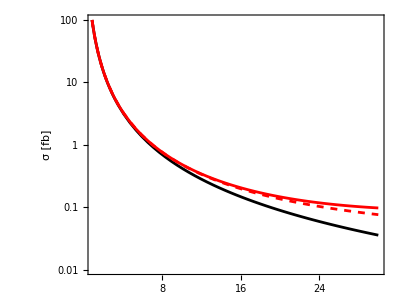

```mathematica
plotσμμbb=LogPlot[{(σBSMμμbb[nTeV]/.SMpoint),(σBSMμμbb[nTeV]/.{Cc[bL,bL,μL]->v^2/(100TeV)^2}/.SMpoint/.NumValues/.λEFTsq->1),(σBSMμμbb[nTeV]/.{Cc[bL,bL,μL]->v^2/(100TeV)^2}/.SMpoint/.NumValues/.λEFTsq->0)},{nTeV,0.5,30},PlotRange->{{1,30},{0.01,100}},PlotStyle->{Black,Red,Directive[Dashed,Red]},AxesOrigin->{0,0},
Frame->True,FrameLabel->{"","σ [fb]"},AspectRatio->3/4,BaseStyle->Directive[16,FontFamily->"Times",Black], FrameStyle->Directive[Black],ImageSize->400,FrameTicks->{{Automatic,Automatic},{None,Automatic}}]
```

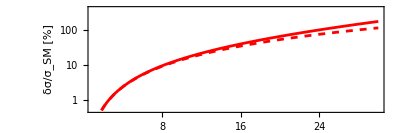

```mathematica
plotRσμμbb=LogPlot[{
100((σBSMμμbb[nTeV]/.{Cc[bL,bL,μL]->v^2/(100TeV)^2}/.SMpoint/.NumValues/.λEFTsq->1)/(σBSMμμbb[nTeV]/.SMpoint)-1),
100((σBSMμμbb[nTeV]/.{Cc[bL,bL,μL]->v^2/(100TeV)^2}/.SMpoint/.NumValues/.λEFTsq->0)/(σBSMμμbb[nTeV]/.SMpoint)-1)},
{nTeV,0.5,30},PlotRange->{{1,30},{0.5,400}},PlotStyle->{Red,Directive[Dashed,Red]},AxesOrigin->{0,0},
Frame->True,FrameLabel->{"E_cm [TeV]","δσ/σ_SM [%]"},AspectRatio->1/3,BaseStyle->Directive[16,FontFamily->"Times",Black], FrameStyle->Directive[Black],ImageSize->400]
```

```mathematica
(* (e[μ]^2 Q[q]Q[l])/s+(gz[q]gz[l])/((s-mZ^2)^2+(ΓZ mZ)^2) +Cc[q,qb,l]/v^2 *)
```

```mathematica
{e[μ]^2,gz[bL]gz[μL]}/.{μ->10TeV}
```

{0.100261,0.0535139}

```mathematica
{1,mll^2/(e[μ]^2 Λ^2),mll^4/(e[μ]^4 Λ^4)}/.{μ->mll}/.{mll->10TeV}/.{Λ->100TeV}
```

{1,0.0997398,0.00994802}

## Deriving the contribution to tagger bins - with η Bins

### N(b-tag + b-tag)

```mathematica
σBSMμμqqbTLLRR[bL,bL,μL,10 TeV]
```

3.37717×10^17 ((7.55834×10^-19+1.13982×10^-41 ⅈ)+(1.43406×10^-14+2.00879×10^-20 ⅈ) Cc[bL,bL,μL]+(1.43406×10^-14-2.00879×10^-20 ⅈ) Conjugate[Cc[bL,bL,μL]]+2.72086×10^-10 λEFTsq Cc[bL,bL,μL] Conjugate[Cc[bL,bL,μL]])

```mathematica
ϵtag[b,t]^2 σBSMμμttBins[10]+
ϵtag[b,t]ϵtag[b,c]σBSMμμtcBins[10]+
ϵtag[b,t]ϵtag[b,u]σBSMμμtuBins[10]/.SMpoint//Chop
```

{0.0231354,0.0193306,0.016477,0.0145747,0.0136235}

```mathematica
ϵtag[b,b]^2 σBSMμμbbBins[10]/.SMpoint//Chop
```

{0.0713162,0.0595878,0.0507915,0.0449273,0.0419952}

```mathematica
NbbBSMBins[nTeV_,Lumi_]=Lumi(
ϵtag[b,t]^2 σBSMμμttBins[nTeV]+
ϵtag[b,t]ϵtag[b,c]σBSMμμtcBins[nTeV]+
ϵtag[b,t]ϵtag[b,u]σBSMμμtuBins[nTeV]+
ϵtag[b,b]ϵtag[b,d]σBSMμμbdLightBins[nTeV]+
ϵtag[b,b]^2 σBSMμμbbBins[nTeV]+
ϵtag[b,c]^2 σBSMμμccBins[nTeV]+
ϵtag[b,u]^2 σBSMμμuuBins[nTeV]+
ϵtag[b,c]ϵtag[b,u]σBSMμμucBins[nTeV]+
ϵtag[b,d]^2 σBSMμμdLightdLightBins[nTeV]
)/.λEFTsq->1;
```

```mathematica
NbbBSMIntBins[nTeV_,Lumi_]=Lumi(
ϵtag[b,t]^2 σBSMμμttBins[nTeV]+
ϵtag[b,t]ϵtag[b,c]σBSMμμtcBins[nTeV]+
ϵtag[b,t]ϵtag[b,u]σBSMμμtuBins[nTeV]+
ϵtag[b,b]ϵtag[b,d]σBSMμμbdLightBins[nTeV]+
ϵtag[b,b]^2 σBSMμμbbBins[nTeV]+
ϵtag[b,c]^2 σBSMμμccBins[nTeV]+
ϵtag[b,u]^2 σBSMμμuuBins[nTeV]+
ϵtag[b,c]ϵtag[b,u]σBSMμμucBins[nTeV]+
ϵtag[b,d]^2 σBSMμμdLightdLightBins[nTeV]
)/.λEFTsq->0;
```

```mathematica
NbbSMBins[nTeV_,Lumi_]=NbbBSMBins[nTeV,Lumi]/.SMpoint//Chop;
```

```mathematica
NbbSMIntBins[nTeV_,Lumi_]=NbbBSMIntBins[nTeV,Lumi]/.SMpoint//Chop;
```

```mathematica
NbbSMBins[10,Lumi10TeV]
```

{970.701+8.55555×10^-21 ⅈ,811.064+7.14854×10^-21 ⅈ,691.335+6.09328×10^-21 ⅈ,611.516+5.38977×10^-21 ⅈ,571.607+5.03802×10^-21 ⅈ}

```mathematica
NbbBSMBins[10,Lumi10TeV]/.{Cc[bL,bL,μL]->v^2 cc}/.NumValues/.SMpoint/.{cc->1/(Λbs TeV)^2}/.Λbs->40//Chop
```

{1818.46,1519.4,1295.11,1145.58,1070.82}

```mathematica
NbbSMBins[10,1]//Chop//Total
```

0.365622

```mathematica
{ϵtag[b,b]^2 σBSMμμbbBins[10]//Total,
ϵtag[b,c]^2 σBSMμμccBins[10]//Total,
ϵtag[b,u]^2 σBSMμμuuBins[10]//Total,
ϵtag[b,d]^2 σBSMμμdLightdLightBins[10]//Total}/.λEFTsq->1/.SMpoint//Chop
```

{0.268618,0.00968235,0.0000968235,0.0000839432}

### N(b-tag + light)

```mathematica
(1-ϵtag[b,d]-ϵtag[c,d])
```

0.97

```mathematica
ϵtag[j,d]
```

0.93

```mathematica
ϵtag[j,b]
```

0.06

```mathematica
ϵtag[j,t]
```

0

```mathematica
{2ϵtag[b,t]ϵtag[j,t],σBSMμμttBins[10]//Total}/.SMpoint//Chop
```

{0,0.968235}

```mathematica
{2ϵtag[b,b]ϵtag[j,b],σBSMμμbbBins[10]//Total}/.SMpoint//Chop
```

{0.096,0.419716}

```mathematica
{2ϵtag[b,c]ϵtag[j,c],σBSMμμccBins[10]//Total}/.SMpoint//Chop
```

{0.072,0.968235}

```mathematica
{2ϵtag[b,u]ϵtag[j,u],σBSMμμuuBins[10]//Total}/.SMpoint//Chop
```

{0.0186,0.968235}

```mathematica
{2ϵtag[b,d]ϵtag[j,d],σBSMμμdLightdLightBins[10]//Total}/.SMpoint//Chop
```

{0.0186,0.839432}

```mathematica
NbjBSMBins[nTeV_,Lumi_]=Lumi(
2ϵtag[b,t]ϵtag[j,t]σBSMμμttBins[nTeV]+
(ϵtag[b,t]ϵtag[j,c]+ϵtag[b,c]ϵtag[j,t])σBSMμμtcBins[nTeV]+
(ϵtag[b,t]ϵtag[j,u]+ϵtag[b,u]ϵtag[j,t])σBSMμμtuBins[nTeV]+
(ϵtag[b,b]ϵtag[j,d]+ϵtag[b,d]ϵtag[j,b])σBSMμμbdLightBins[nTeV]
+2ϵtag[b,b]ϵtag[j,b]σBSMμμbbBins[nTeV]
+2ϵtag[b,c]ϵtag[j,c]σBSMμμccBins[nTeV]
+2ϵtag[b,u]ϵtag[j,u]σBSMμμuuBins[nTeV]
+(ϵtag[b,c]ϵtag[j,u]+ϵtag[b,u]ϵtag[j,c])σBSMμμucBins[nTeV]
+2ϵtag[b,d]ϵtag[j,d]σBSMμμdLightdLightBins[nTeV]
)/.λEFTsq->1;
```

```mathematica
NbjSMBins[nTeV_,Lumi_]=NbjBSMBins[nTeV,Lumi]/.SMpoint//Chop;
```

```mathematica
NbjSMBins[10,1]
```

{0.0381323+3.20079×10^-25 ⅈ,0.0318612+2.6744×10^-25 ⅈ,0.0271579+2.27961×10^-25 ⅈ,0.0240223+2.01641×10^-25 ⅈ,0.0224546+1.88482×10^-25 ⅈ}

```mathematica
NbjSMBins[10,1]//Total//Chop
```

0.143628

```mathematica
NbjSMBins[10,Lumi10TeV]
```

{381.323+3.20079×10^-21 ⅈ,318.612+2.6744×10^-21 ⅈ,271.579+2.27961×10^-21 ⅈ,240.223+2.01641×10^-21 ⅈ,224.546+1.88482×10^-21 ⅈ}

```mathematica
NbjBSMBins[10,Lumi10TeV]/.{Cc[sL,bL,μL]->v^2 cbs,Cc[bL,sL,μL]->v^2 cbs}/.NumValues/.SMpoint/.{cbs->1/(Λbs TeV)^2}/.Λbs->40
```

{902.9+3.20079×10^-21 ⅈ,754.413+2.6744×10^-21 ⅈ,643.047+2.27961×10^-21 ⅈ,568.803+2.01641×10^-21 ⅈ,531.681+1.88482×10^-21 ⅈ}

```mathematica
σbjSMtot=NbjSMBins[10,1]//Chop//Total
```

0.143628

```mathematica
ϵtag[b,d]
```

0.01

```mathematica
σBSMμμbbBins[10]/.λEFTsq->1/.SMpoint//Chop//Total
```

0.419716

```mathematica
σBSMμμccBins[10]/.λEFTsq->1/.SMpoint//Chop//Total
```

0.968235

```mathematica
σBSMμμuuBins[10]/.λEFTsq->1/.SMpoint//Chop//Total
```

0.968235

```mathematica
σBSMμμdLightdLightBins[10]/.λEFTsq->1/.SMpoint//Chop//Total
```

0.839432

```mathematica
σBSMμμuuBins[10]+σBSMμμdLightdLightBins[10]/.λEFTsq->1/.SMpoint//Chop//Total
```

1.80767

```mathematica
1/σbjSMtot{2ϵtag[b,b]ϵtag[j,b]σBSMμμbbBins[10]//Total,
2ϵtag[b,c]ϵtag[j,c]σBSMμμccBins[10]//Total,
2ϵtag[b,u]ϵtag[j,u]σBSMμμuuBins[10]//Total,
2ϵtag[b,d]ϵtag[j,d]σBSMμμdLightdLightBins[10]//Total}/.λEFTsq->1/.SMpoint//Chop
```

{0.280535,0.485371,0.125387,0.108707}

```mathematica
%//Total
```

1.

```mathematica
{ϵtag[b,b],ϵtag[j,b]}
```

{0.8,0.06}

```mathematica
2ϵtag[b,b]ϵtag[j,b]
```

0.096

```mathematica
{ϵtag[b,c],ϵtag[j,c]}
```

{0.1,0.36}

```mathematica
2ϵtag[b,c]ϵtag[j,c]
```

0.072

```mathematica
ϵtag[b,u]
```

0.01

```mathematica
ϵtag[j,u]
```

0.93

```mathematica
2ϵtag[b,u]ϵtag[j,u]
```

0.0186

### N(c-tag + c-tag)

```mathematica
NccBSMBins[nTeV_,Lumi_]=Lumi(
ϵtag[c,t]^2 σBSMμμttBins[nTeV]+
ϵtag[c,t]ϵtag[c,c]σBSMμμtcBins[nTeV]+
ϵtag[c,t]ϵtag[c,u]σBSMμμtuBins[nTeV]+
ϵtag[c,b]ϵtag[c,d]σBSMμμbdLightBins[nTeV]
+ϵtag[c,b]^2 σBSMμμbbBins[nTeV]+
ϵtag[c,c]^2 σBSMμμccBins[nTeV]+
ϵtag[c,u]^2 σBSMμμuuBins[nTeV]+
ϵtag[c,c]ϵtag[c,u]σBSMμμucBins[nTeV]+
ϵtag[c,d]^2 σBSMμμdLightdLightBins[nTeV]
)/.λEFTsq->1;
```

```mathematica
NccSMBins[nTeV_,Lumi_]=NccBSMBins[nTeV,Lumi]/.SMpoint//Chop;
```

```mathematica
NccSMBins[10,Lumi10TeV]
```

{655.711+5.20858×10^-21 ⅈ,547.876+4.352×10^-21 ⅈ,466.999+3.70956×10^-21 ⅈ,413.081+3.28127×10^-21 ⅈ,386.122+3.06712×10^-21 ⅈ}

```mathematica
NccBSMBins[10,Lumi10TeV]/.{Cc[bL,bL,μL]->v^2 cc}/.NumValues/.SMpoint/.{cc->1/(Λbs TeV)^2}/.Λbs->40
```

{668.958+5.10639×10^-21 ⅈ,558.943+4.26661×10^-21 ⅈ,476.433+3.63678×10^-21 ⅈ,421.426+3.21689×10^-21 ⅈ,393.922+3.00694×10^-21 ⅈ}

### N(c-tag + light)

```mathematica
ϵtag[j,t]
```

0

```mathematica
ϵtag[c,t]
```

0

```mathematica
NcjBSMBins[nTeV_,Lumi_]=Lumi(
2ϵtag[c,t]ϵtag[j,t]σBSMμμttBins[nTeV]+
(ϵtag[c,t]ϵtag[j,c]+ϵtag[c,c]ϵtag[j,t])σBSMμμtcBins[nTeV]+
(ϵtag[c,t]ϵtag[j,u]+ϵtag[c,u]ϵtag[j,t])σBSMμμtuBins[nTeV]+
(ϵtag[c,b]ϵtag[j,d]+ϵtag[c,d]ϵtag[j,b])σBSMμμbdLightBins[nTeV]+2ϵtag[c,b]ϵtag[j,b]σBSMμμbbBins[nTeV]+
2ϵtag[c,c]ϵtag[j,c]σBSMμμccBins[nTeV]+
2ϵtag[c,u]ϵtag[j,u]σBSMμμuuBins[nTeV]+
(ϵtag[c,c]ϵtag[j,u]+ϵtag[b,u]ϵtag[j,c])σBSMμμucBins[nTeV]+2ϵtag[c,d]ϵtag[j,d]σBSMμμdLightdLightBins[nTeV]
)/.λEFTsq->1;
```

```mathematica
NcjSMBins[nTeV_,Lumi_]=NcjBSMBins[nTeV,Lumi]/.SMpoint//Chop;
```

```mathematica
NcjSMBins[10,Lumi10TeV]
```

{1117.32+8.96734×10^-21 ⅈ,933.567+7.49261×10^-21 ⅈ,795.755+6.38655×10^-21 ⅈ,703.88+5.64919×10^-21 ⅈ,657.943+5.2805×10^-21 ⅈ}

```mathematica
NcjBSMBins[10,Lumi10TeV]/.{Cc[uL,cL,μL]->v^2 cc,Cc[cL,uL,μL]->v^2 cc}/.NumValues/.SMpoint/.{cc->1/(Λbs TeV)^2}/.Λbs->40
```

{1445.56+8.96734×10^-21 ⅈ,1207.83+7.49261×10^-21 ⅈ,1029.53+6.38655×10^-21 ⅈ,910.666+5.64919×10^-21 ⅈ,851.233+5.2805×10^-21 ⅈ}

### N(light + light)

```mathematica
NjjBSMBins[nTeV_,Lumi_]=Lumi(
ϵtag[j,t]^2 σBSMμμttBins[nTeV]+
ϵtag[j,t]ϵtag[j,c]σBSMμμtcBins[nTeV]+
ϵtag[j,t]ϵtag[j,u]σBSMμμtuBins[nTeV]+
ϵtag[j,b]ϵtag[j,d]σBSMμμbdLightBins[nTeV]
+ϵtag[j,b]^2 σBSMμμbbBins[nTeV]
+ϵtag[j,c]^2 σBSMμμccBins[nTeV]
+ϵtag[j,u]^2 σBSMμμuuBins[nTeV]
+ϵtag[j,c]ϵtag[j,u]σBSMμμucBins[nTeV]
+ϵtag[j,d]^2 σBSMμμdLightdLightBins[nTeV]
)/.{low->-cθCut,up->cθCut}/.λEFTsq->1;
```

```mathematica
NjjSMBins[nTeV_,Lumi_]=NjjBSMBins[nTeV,Lumi]/.SMpoint//Chop;
```

```mathematica
NjjSMBins[10,Lumi10TeV]
```

{4488.01+3.78962×10^-20 ⅈ,3749.93+3.1664×10^-20 ⅈ,3196.37+2.69898×10^-20 ⅈ,2827.33+2.38736×10^-20 ⅈ,2642.81+2.23156×10^-20 ⅈ}

```mathematica
NjjBSMBins[10,Lumi10TeV]/.{Cc[uL,cL,μL]->v^2 cc,Cc[cL,uL,μL]->v^2 cc}/.NumValues/.SMpoint/.{cc->1/(Λbs TeV)^2}/.Λbs->40
```

{4722.53+3.78962×10^-20 ⅈ,3945.88+3.1664×10^-20 ⅈ,3363.4+2.69898×10^-20 ⅈ,2975.07+2.38736×10^-20 ⅈ,2780.91+2.23156×10^-20 ⅈ}

### N(t-tag + t-tag)

```mathematica
ϵtag[t,W]=0.1;
ϵtag[t,Z]=0.1;
```

```mathematica
cθCut
```

0.939693

```mathematica
NttBSMBins[nTeV_,Lumi_]=Lumi(
ϵtag[t,t]^2 σBSMμμttBins[nTeV]+
ϵtag[t,t]ϵtag[t,c]σBSMμμtcBins[nTeV]+
ϵtag[t,t]ϵtag[t,u]σBSMμμtuBins[nTeV]+
ϵtag[t,b]ϵtag[t,d]σBSMμμbdLightBins[nTeV]+
ϵtag[t,b]^2 σBSMμμbbBins[nTeV]+
ϵtag[t,c]^2 σBSMμμccBins[nTeV]+
ϵtag[t,u]^2 σBSMμμuuBins[nTeV]+
ϵtag[t,c]ϵtag[t,u]σBSMμμucBins[nTeV]+
ϵtag[t,d]^2 σBSMμμdLightdLightBins[nTeV]
)(*+ϵtag[t,W]^2NWW[nTeV,Lumi]*)/.λEFTsq->1;
```

```mathematica
ϵtag[t,t]
```

0.6

```mathematica
NttSMBins[nTeV_,Lumi_]=NttBSMBins[nTeV,Lumi]/.SMpoint//Chop;
```

```mathematica
NttSMBins[10,Lumi10TeV]
```

{938.989+7.44433×10^-21 ⅈ,784.566+6.22007×10^-21 ⅈ,668.749+5.30187×10^-21 ⅈ,591.538+4.68973×10^-21 ⅈ,552.933+4.38367×10^-21 ⅈ}

```mathematica
NttSMBins[10,Lumi10TeV]
```

{938.989+7.44433×10^-21 ⅈ,784.566+6.22007×10^-21 ⅈ,668.749+5.30187×10^-21 ⅈ,591.538+4.68973×10^-21 ⅈ,552.933+4.38367×10^-21 ⅈ}

```mathematica
NttBSMBins[10,Lumi10TeV]/.{Cc[tL,tL,μL]->v^2 1/(Λ TeV)^2}/.NumValues/.SMpoint/.Λ->40
```

{623.758+8.54986×10^-23 ⅈ,521.178+7.14379×10^-23 ⅈ,444.242+6.08923×10^-23 ⅈ,392.951+5.38619×10^-23 ⅈ,367.306+5.03467×10^-23 ⅈ}

```mathematica
NttBSMBins[10,Lumi10TeV]/.{Cc[tL,tL,μL]->-v^2 1/(Λ TeV)^2}/.NumValues/.SMpoint/.Λ->40
```

{1506.39+8.54986×10^-23 ⅈ,1258.66+7.14379×10^-23 ⅈ,1072.85+6.08923×10^-23 ⅈ,948.987+5.38619×10^-23 ⅈ,887.053+5.03467×10^-23 ⅈ}

```mathematica
χSQ1d95
```

3.84146

### N(t-tag + c-tag)

```mathematica
2ϵtag[t,t]ϵtag[c,t]
```

0.

```mathematica
ϵtag[c,t]
```

0

```mathematica
ϵtag[b,c]
```

0.1

```mathematica
ϵtag[t,u]ϵtag[c,t]
```

0.

```mathematica
NtcBSMBins[nTeV_,Lumi_]=Lumi(
2ϵtag[t,t]ϵtag[c,t]σBSMμμttBins[nTeV]+
(ϵtag[t,t]ϵtag[c,c]+ϵtag[t,c]ϵtag[c,t])σBSMμμtcBins[nTeV]+
(ϵtag[t,t]ϵtag[c,u]+ϵtag[t,u]ϵtag[c,t])σBSMμμtuBins[nTeV]+
(ϵtag[t,b]ϵtag[c,d]+ϵtag[t,d]ϵtag[c,b])σBSMμμbdLightBins[nTeV]+
2ϵtag[t,b]ϵtag[c,b]σBSMμμbbBins[nTeV]+
2ϵtag[t,c]ϵtag[c,c]σBSMμμccBins[nTeV]+
2ϵtag[t,u]ϵtag[c,u]σBSMμμuuBins[nTeV]+
(ϵtag[t,c]ϵtag[c,u]+ϵtag[t,u]ϵtag[c,c])σBSMμμucBins[nTeV]+
2ϵtag[t,d]ϵtag[c,d]σBSMμμdLightdLightBins[nTeV]
)/.{low->-cθCut,up->cθCut}/.λEFTsq->1;
```

```mathematica
NtcSMBins[nTeV_,Lumi_]=NtcBSMBins[nTeV,Lumi]/.SMpoint//Chop;
```

```mathematica
NtcSMBins[10,Lumi10TeV]
```

{119.417+9.61076×10^-22 ⅈ,99.7782+8.03021×10^-22 ⅈ,85.049+6.8448×10^-22 ⅈ,75.2296+6.05452×10^-22 ⅈ,70.3199+5.65939×10^-22 ⅈ}

```mathematica
NtcBSMBins[10,Lumi10TeV]/.{Cc[tL,tL,μL]->-v^2 1/(Λ TeV)^2}/.NumValues/.SMpoint/.Λ->40
```

{119.417+9.61076×10^-22 ⅈ,99.7782+8.03021×10^-22 ⅈ,85.049+6.8448×10^-22 ⅈ,75.2296+6.05452×10^-22 ⅈ,70.3199+5.65939×10^-22 ⅈ}

```mathematica
NtcBSMBins[10,Lumi10TeV]/.{Cc[tL,cL,μL]->-v^2 1/(Λ TeV)^2}/.NumValues/.SMpoint/.Λ->40
```

{224.489+9.61076×10^-22 ⅈ,187.57+8.03021×10^-22 ⅈ,159.882+6.8448×10^-22 ⅈ,141.422+6.05452×10^-22 ⅈ,132.193+5.65939×10^-22 ⅈ}

```mathematica
NtcBSMBins[10,Lumi10TeV]/.{Cc[tL,uL,μL]->-v^2 1/(Λ TeV)^2}/.NumValues/.SMpoint/.Λ->40
```

{123.62+9.61076×10^-22 ⅈ,103.29+8.03021×10^-22 ⅈ,88.0423+6.8448×10^-22 ⅈ,77.8773+6.05452×10^-22 ⅈ,72.7948+5.65939×10^-22 ⅈ}

### N(t-tag + light)

```mathematica
2ϵtag[t,t]ϵtag[c,t]
```

0.

```mathematica
ϵtag[c,t]
```

0

```mathematica
ϵtag[b,c]
```

0.1

```mathematica
(1-ϵtag[b,c]-ϵtag[c,c])
```

0.4

```mathematica
(1-ϵtag[b,u]-ϵtag[c,u])
```

0.97

```mathematica
{2ϵtag[t,b]ϵtag[c,b],2ϵtag[t,b]ϵtag[j,b]}
```

{0.008,0.0048}

```mathematica
{2ϵtag[t,c]ϵtag[c,c],2ϵtag[t,c]ϵtag[j,c]}
```

{0.04,0.0288}

```mathematica
{2ϵtag[t,u]ϵtag[c,u],2ϵtag[t,u]ϵtag[j,u]}
```

{0.0016,0.0744}

```mathematica
{2ϵtag[t,d]ϵtag[c,d],2ϵtag[t,d]ϵtag[j,d]}
```

{0.0016,0.0744}

```mathematica
NtjBSMBins[nTeV_,Lumi_]=Lumi(
2ϵtag[t,t]ϵtag[j,t]σBSMμμttBins[nTeV]+
(ϵtag[t,t]ϵtag[j,c]+ϵtag[t,c]ϵtag[j,t])σBSMμμtcBins[nTeV]+
(ϵtag[t,t]ϵtag[j,u]+ϵtag[t,u]ϵtag[j,t])σBSMμμtuBins[nTeV]+
(ϵtag[t,b]ϵtag[j,d]+ϵtag[t,d]ϵtag[j,b])σBSMμμbdLightBins[nTeV]+
2ϵtag[t,b]ϵtag[j,b]σBSMμμbbBins[nTeV]+
2ϵtag[t,c]ϵtag[j,c]σBSMμμccBins[nTeV]+
2ϵtag[t,u]ϵtag[j,u]σBSMμμuuBins[nTeV]+
(ϵtag[t,c]ϵtag[j,u]+ϵtag[t,u]ϵtag[j,c])σBSMμμucBins[nTeV]+
2ϵtag[t,d]ϵtag[j,d]σBSMμμdLightdLightBins[nTeV]
)/.{low->-cθCut,up->cθCut}/.λEFTsq->1;
```

```mathematica
NtjSMBins[nTeV_,Lumi_]=NtjBSMBins[nTeV,Lumi]/.SMpoint//Chop;
```

```mathematica
NtcSMBins[3,Lumi10TeV]//Total
```

6189.98+5.34067×10^-19 ⅈ

```mathematica
NtjSMBins[3,Lumi10TeV]//Total
```

22989.3+2.03611×10^-18 ⅈ

```mathematica
NtjBSMBins[10,Lumi10TeV]/.{Cc[tL,tL,μL]->-v^2 1/(Λ TeV)^2}/.NumValues/.SMpoint/.Λ->40
```

{436.444+3.66502×10^-21 ⅈ,364.668+3.06229×10^-21 ⅈ,310.836+2.61024×10^-21 ⅈ,274.948+2.30887×10^-21 ⅈ,257.004+2.15818×10^-21 ⅈ}

```mathematica
NtjBSMBins[10,Lumi10TeV]/.{Cc[tL,cL,μL]->-v^2 1/(Λ TeV)^2}/.NumValues/.SMpoint/.Λ->40
```

{512.096+3.66502×10^-21 ⅈ,427.879+3.06229×10^-21 ⅈ,364.716+2.61024×10^-21 ⅈ,322.607+2.30887×10^-21 ⅈ,301.553+2.15818×10^-21 ⅈ}

```mathematica
NtjBSMBins[10,Lumi10TeV]/.{Cc[tL,uL,μL]->-v^2 1/(Λ TeV)^2}/.NumValues/.SMpoint/.Λ->40
```

{631.878+3.66502×10^-21 ⅈ,527.962+3.06229×10^-21 ⅈ,450.025+2.61024×10^-21 ⅈ,398.067+2.30887×10^-21 ⅈ,372.088+2.15818×10^-21 ⅈ}

```mathematica
NtjBSMBins[10,Lumi10TeV]/.{Cuγ[3,1]->v 1/(Λ TeV)^2}/.NumValues/.SMpoint/.Λ->8
```

{477.213+3.66502×10^-21 ⅈ,446.316+3.06229×10^-21 ⅈ,423.143+2.61024×10^-21 ⅈ,407.695+2.30887×10^-21 ⅈ,399.97+2.15818×10^-21 ⅈ}

### Summary of SM cross sections for each category

```mathematica
NtjSMBins[3,1]//Total//Chop
```

2.29893

```mathematica
NtcSMBins[3,1]//Total//Chop
```

0.618998

```mathematica
Chop[SetPrecision[1/Lumi{
NjjBSMBins[3,Lumi]//Total,
NcjBSMBins[3,Lumi]//Total,
NbjBSMBins[3,Lumi]//Total,
NtjBSMBins[3,Lumi]//Total,
NccBSMBins[3,Lumi]//Total,
"bc",
NtcBSMBins[3,Lumi]//Total,
NbbBSMBins[3,Lumi]//Total,
"tb",
NttBSMBins[3,Lumi]//Total}/.SMpoint,2]]
```

{24.,5.8,2.,2.3,3.4,bc/Lumi,0.62,5.2,tb/Lumi,4.8}

```mathematica
Chop[SetPrecision[1/Lumi{NjjBSMBins[10,Lumi]//Total,NcjBSMBins[10,Lumi]//Total,NbjBSMBins[10,Lumi]//Total,NtjBSMBins[10,Lumi]//Total,NccBSMBins[10,Lumi]//Total,"bc",NtcBSMBins[10,Lumi]//Total,NbbBSMBins[10,Lumi]//Total,"tb",NttBSMBins[10,Lumi]//Total}/.SMpoint,2]]
```

{1.7,0.42,0.14,0.16,0.25,bc/Lumi,0.045,0.37,tb/Lumi,0.35}

```mathematica
Total[NbbBSMBins[3,Lumi3TeV]]/.SMpoint//Chop
```

5210.12

```mathematica
1/√%
```

0.013854

```mathematica
Total[NbbBSMBins[10,Lumi10TeV]]/.SMpoint//Chop
```

3656.22

```mathematica
1/√%
```

0.016538

```mathematica
Total[NbjBSMBins[3,Lumi3TeV]]/.SMpoint//Chop
```

2008.25

```mathematica
1/√%
```

0.0223147

```mathematica
Total[NbjBSMBins[10,Lumi10TeV]]/.SMpoint//Chop
```

1436.28

```mathematica
1/√%
```

0.0263864

### Example plot

```mathematica
NbbBSMBins[10,1]/.SMpoint//Total
```

0.365622+3.22252×10^-24 ⅈ

```mathematica
(NbbBSMBins[10,1]/.{Cc[bL,bL,μL]->v^2/(100TeV)^2}/.SMpoint/.NumValues)//Total
```

0.405365+7.58933×10^-25 ⅈ

```mathematica
(NbbBSMIntBins[10,1]/.{Cc[bL,bL,μL]->v^2/(100TeV)^2}/.SMpoint/.NumValues)//Total
```

0.403204+7.58933×10^-25 ⅈ

```mathematica
(NbbBSMBins[10,1]/.{Cc[bL,bL,μL]->Ccbbμμ}/.SMpoint/.NumValues)//ComplexExpand//Total
```

(0.365622+3.22252×10^-24 ⅈ)+6199.11 Ccbbμμ+5.88084×10^7 Ccbbμμ^2

```mathematica
(NbbBSMIntBins[10,1]/.{Cc[bL,bL,μL]->Ccbbμμ}/.SMpoint/.NumValues)//ComplexExpand//Total
```

(0.365622+3.22252×10^-24 ⅈ)+6199.11 Ccbbμμ

```mathematica
fSM=(NbbBSMBins[nTeV,1]/.SMpoint//Total);
fBSM=(NbbBSMBins[nTeV,1]/.{Cc[bL,bL,μL]->v^2/(100TeV)^2}/.SMpoint/.NumValues//Total);
fBSMInt=(NbbBSMIntBins[nTeV,1]/.{Cc[bL,bL,μL]->v^2/(100TeV)^2}/.SMpoint/.NumValues//Total);
```

```mathematica
fSM/.nTeV->10
```

0.365622+3.22252×10^-24 ⅈ

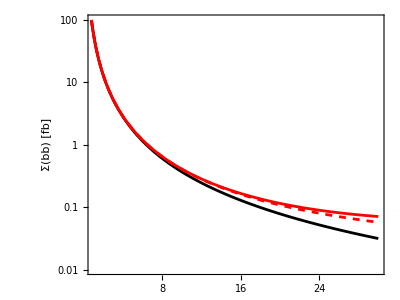

```mathematica
plotΣμμbb=LogPlot[{fSM,fBSM,fBSMInt},{nTeV,0.5,30},PlotRange->{{1,30},{0.01,100}},PlotStyle->{Black,Red,Directive[Dashed,Red]},AxesOrigin->{0,0},
Frame->True,FrameLabel->{"","Σ(bb) [fb]"},AspectRatio->3/4,BaseStyle->Directive[16,FontFamily->"Times",Black], FrameStyle->Directive[Black],ImageSize->400,FrameTicks->{{Automatic,Automatic},{None,Automatic}}]
```

```mathematica
Export["Plot/Sigma_mumubb_top.pdf",%]
```

Plot/Sigma_mumubb_top.pdf

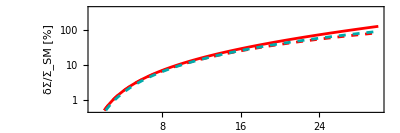

```mathematica
plotRΣμμbb=LogPlot[{
100(fBSM/fSM-1),100(fBSMInt/fSM-1),10(nTeV/10)^2((100TeV)/(100TeV))^2},
{nTeV,0.5,30},PlotRange->{{1,30},{0.5,400}},PlotStyle->{Red,Directive[Dashed,Red],Directive[Darker[Cyan],Dashed]},AxesOrigin->{0,0},
Frame->True,FrameLabel->{"E_cm [TeV]","δΣ/Σ_SM [%]"},AspectRatio->1/3,BaseStyle->Directive[16,FontFamily->"Times",Black], FrameStyle->Directive[Black],ImageSize->400]
```

```mathematica
Export["Plot/Sigma_mumubb_bottom.pdf",%]
```

Plot/Sigma_mumubb_bottom.pdf

```mathematica
fSM=(NbjBSMBins[nTeV,1]/.SMpoint//Total);
fBSM=(NbjBSMBins[nTeV,1]/.{Cc[bL,sL,μL]->v^2/(100TeV)^2,Cc[sL,bL,μL]->v^2/(100TeV)^2}/.SMpoint/.NumValues//Total);
```

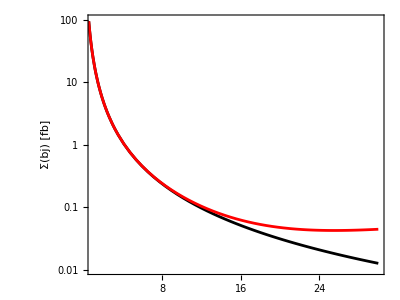

```mathematica
plotΣμμbj=LogPlot[{fSM,fBSM},{nTeV,0.5,30},PlotRange->{{1,30},{0.01,100}},PlotStyle->{Black,Red},AxesOrigin->{0,0},
Frame->True,FrameLabel->{"","Σ(bj) [fb]"},AspectRatio->3/4,BaseStyle->Directive[16,FontFamily->"Times",Black], FrameStyle->Directive[Black],ImageSize->400,FrameTicks->{{Automatic,Automatic},{None,Automatic}}]
```

```mathematica
Export["Plot/Sigma_mumubj_top.pdf",%]
```

Plot/Sigma_mumubj_top.pdf

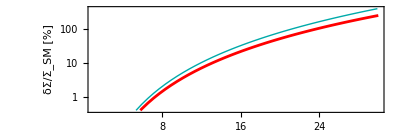

```mathematica
plotRΣμμbj=LogPlot[
{100(fBSM/fSM-1),1/(2 0.10)(nTeV/10)^4((100 TeV)/(100TeV))^4},
{nTeV,0.5,30},PlotRange->{{1,30},{0.4,400}},PlotStyle->{Red,Directive[Thick,Darker[Cyan]]},AxesOrigin->{0,0},
Frame->True,FrameLabel->{"E_cm [TeV]","δΣ/Σ_SM [%]"},AspectRatio->1/3,BaseStyle->Directive[16,FontFamily->"Times",Black], FrameStyle->Directive[Black],ImageSize->400]
```

```mathematica
Export["Plot/Sigma_mumubj_bottom.pdf",%]
```

Plot/Sigma_mumubj_bottom.pdf

## Number of events inclusive in η

```mathematica
NbbBSM[nTeV_,Lumi_]:=Total[NbbBSMBins[nTeV,Lumi]]
NbjBSM[nTeV_,Lumi_]:=Total[NbjBSMBins[nTeV,Lumi]]
NccBSM[nTeV_,Lumi_]:=Total[NccBSMBins[nTeV,Lumi]]
NcjBSM[nTeV_,Lumi_]:=Total[NcjBSMBins[nTeV,Lumi]]
NjjBSM[nTeV_,Lumi_]:=Total[NjjBSMBins[nTeV,Lumi]]
NttBSM[nTeV_,Lumi_]:=Total[NttBSMBins[nTeV,Lumi]]
NtcBSM[nTeV_,Lumi_]:=Total[NtcBSMBins[nTeV,Lumi]]
NtjBSM[nTeV_,Lumi_]:=Total[NtjBSMBins[nTeV,Lumi]]
```

```mathematica
NbbSM[nTeV_,Lumi_]:=Total[NbbSMBins[nTeV,Lumi]]
NbjSM[nTeV_,Lumi_]:=Total[NbjSMBins[nTeV,Lumi]]
NccSM[nTeV_,Lumi_]:=Total[NccSMBins[nTeV,Lumi]]
NcjSM[nTeV_,Lumi_]:=Total[NcjSMBins[nTeV,Lumi]]
NjjSM[nTeV_,Lumi_]:=Total[NjjSMBins[nTeV,Lumi]]
NttSM[nTeV_,Lumi_]:=Total[NttSMBins[nTeV,Lumi]]
NtcSM[nTeV_,Lumi_]:=Total[NtcSMBins[nTeV,Lumi]]
NtjSM[nTeV_,Lumi_]:=Total[NtjSMBins[nTeV,Lumi]]
```

## Building the χSQ with η bins

```mathematica
χSQjjMuC3ηBins=Total[Total[{
(NtjBSMBins[3,Lumi3TeV]-Chop[NtjSMBins[3,Lumi3TeV]])^2/Chop[NtjSMBins[3,Lumi3TeV]+(syst NtjSMBins[3,Lumi3TeV])^2],(NtcBSMBins[3,Lumi3TeV]-Chop[NtcSMBins[3,Lumi3TeV]])^2/Chop[NtcSMBins[3,Lumi3TeV]+(syst NtcSMBins[3,Lumi3TeV])^2],(NttBSMBins[3,Lumi3TeV]-Chop[NttSMBins[3,Lumi3TeV]])^2/Chop[NttSMBins[3,Lumi3TeV]+(syst NttSMBins[3,Lumi3TeV])^2],
(NbbBSMBins[3,Lumi3TeV]-Chop[NbbSMBins[3,Lumi3TeV]])^2/Chop[NbbSMBins[3,Lumi3TeV]+(syst NbbSMBins[3,Lumi3TeV])^2],
(NbjBSMBins[3,Lumi3TeV]-Chop[NbjSMBins[3,Lumi3TeV]])^2/Chop[NbjSMBins[3,Lumi3TeV]+(syst NbjSMBins[3,Lumi3TeV])^2],
(NccBSMBins[3,Lumi3TeV]-Chop[NccSMBins[3,Lumi3TeV]])^2/Chop[NccSMBins[3,Lumi3TeV]+(syst NccSMBins[3,Lumi3TeV])^2],
(NcjBSMBins[3,Lumi3TeV]-Chop[NcjSMBins[3,Lumi3TeV]])^2/Chop[NcjSMBins[3,Lumi3TeV]+(syst NcjSMBins[3,Lumi3TeV])^2],
(NjjBSMBins[3,Lumi3TeV]-Chop[NjjSMBins[3,Lumi3TeV]])^2/Chop[NjjSMBins[3,Lumi3TeV]+(syst NjjSMBins[3,Lumi3TeV])^2]}]]/.syst->0.2/100;
```

```mathematica
χSQjjMuC3ηBins/.SMpoint//Chop
```

0

```mathematica
χSQjjMuC7ηBins=Total[Total[{
(NtjBSMBins[7.6,Lumi7TeV]-Chop[NtjSMBins[7.6,Lumi7TeV]])^2/Chop[NtjSMBins[7.6,Lumi7TeV]+(syst NtjSMBins[7.6,Lumi7TeV])^2],(NtcBSMBins[7.6,Lumi7TeV]-Chop[NtcSMBins[7.6,Lumi7TeV]])^2/Chop[NtcSMBins[7.6,Lumi7TeV]+(syst NtcSMBins[7.6,Lumi7TeV])^2],(NttBSMBins[7.6,Lumi7TeV]-Chop[NttSMBins[7.6,Lumi7TeV]])^2/Chop[NttSMBins[7.6,Lumi7TeV]+(syst NttSMBins[7.6,Lumi7TeV])^2],(NbbBSMBins[7.6,Lumi7TeV]-Chop[NbbSMBins[7.6,Lumi7TeV]])^2/Chop[NbbSMBins[7.6,Lumi7TeV]+(syst NbbSMBins[7.6,Lumi7TeV])^2],
(NbjBSMBins[7.6,Lumi7TeV]-Chop[NbjSMBins[7.6,Lumi7TeV]])^2/Chop[NbjSMBins[7.6,Lumi7TeV]+(syst NbjSMBins[7.6,Lumi7TeV])^2],
(NccBSMBins[7.6,Lumi7TeV]-Chop[NccSMBins[7.6,Lumi7TeV]])^2/Chop[NccSMBins[7.6,Lumi7TeV]+(syst NccSMBins[7.6,Lumi7TeV])^2],
(NcjBSMBins[7.6,Lumi7TeV]-Chop[NcjSMBins[7.6,Lumi7TeV]])^2/Chop[NcjSMBins[7.6,Lumi7TeV]+(syst NcjSMBins[7.6,Lumi7TeV])^2],
(NjjBSMBins[7.6,Lumi7TeV]-Chop[NjjSMBins[7.6,Lumi7TeV]])^2/Chop[NjjSMBins[7.6,Lumi7TeV]+(syst NjjSMBins[7.6,Lumi7TeV])^2]}]]/.syst->0.2/100;
```

```mathematica
χSQjjMuC7ηBins/.SMpoint//Chop
```

0

```mathematica
χSQjjMuC10ηBins=Total[Total[{
(NtjBSMBins[10,Lumi10TeV]-Chop[NtjSMBins[10,Lumi10TeV]])^2/Chop[NtjSMBins[10,Lumi10TeV]+(syst NtjSMBins[10,Lumi10TeV])^2],(NtcBSMBins[10,Lumi10TeV]-Chop[NtcSMBins[10,Lumi10TeV]])^2/Chop[NtcSMBins[10,Lumi10TeV]+(syst NtcSMBins[10,Lumi10TeV])^2],(NttBSMBins[10,Lumi10TeV]-Chop[NttSMBins[10,Lumi10TeV]])^2/Chop[NttSMBins[10,Lumi10TeV]+(syst NttSMBins[10,Lumi10TeV])^2],(NbbBSMBins[10,Lumi10TeV]-Chop[NbbSMBins[10,Lumi10TeV]])^2/Chop[NbbSMBins[10,Lumi10TeV]+(syst NbbSMBins[10,Lumi10TeV])^2],
(NbjBSMBins[10,Lumi10TeV]-Chop[NbjSMBins[10,Lumi10TeV]])^2/Chop[NbjSMBins[10,Lumi10TeV]+(syst NbjSMBins[10,Lumi10TeV])^2],
(NccBSMBins[10,Lumi10TeV]-Chop[NccSMBins[10,Lumi10TeV]])^2/Chop[NccSMBins[10,Lumi10TeV]+(syst NccSMBins[10,Lumi10TeV])^2],
(NcjBSMBins[10,Lumi10TeV]-Chop[NcjSMBins[10,Lumi10TeV]])^2/Chop[NcjSMBins[10,Lumi10TeV]+(syst NcjSMBins[10,Lumi10TeV])^2],
(NjjBSMBins[10,Lumi10TeV]-Chop[NjjSMBins[10,Lumi10TeV]])^2/Chop[NjjSMBins[10,Lumi10TeV]+(syst NjjSMBins[10,Lumi10TeV])^2]}]]/.syst->0.2/100;
```

```mathematica
χSQjjMuC10ηBins/.SMpoint//Chop
```

0

```mathematica
χSQjjMuC30ηBins=Total[Total[{
(NtjBSMBins[30,Lumi30TeV]-Chop[NtjSMBins[30,Lumi30TeV]])^2/Chop[NtjSMBins[30,Lumi30TeV]+(syst NtjSMBins[30,Lumi30TeV])^2],(NtcBSMBins[30,Lumi30TeV]-Chop[NtcSMBins[30,Lumi30TeV]])^2/Chop[NtcSMBins[30,Lumi30TeV]+(syst NtcSMBins[30,Lumi30TeV])^2],(NttBSMBins[30,Lumi30TeV]-Chop[NttSMBins[30,Lumi30TeV]])^2/Chop[NttSMBins[30,Lumi30TeV]+(syst NttSMBins[30,Lumi30TeV])^2],(NbbBSMBins[30,Lumi30TeV]-Chop[NbbSMBins[30,Lumi30TeV]])^2/Chop[NbbSMBins[30,Lumi30TeV]+(syst NbbSMBins[30,Lumi30TeV])^2],
(NbjBSMBins[30,Lumi30TeV]-Chop[NbjSMBins[30,Lumi30TeV]])^2/Chop[NbjSMBins[30,Lumi30TeV]+(syst NbjSMBins[30,Lumi30TeV])^2],
(NccBSMBins[30,Lumi30TeV]-Chop[NccSMBins[30,Lumi30TeV]])^2/Chop[NccSMBins[30,Lumi30TeV]+(syst NccSMBins[30,Lumi30TeV])^2],
(NcjBSMBins[30,Lumi30TeV]-Chop[NcjSMBins[30,Lumi30TeV]])^2/Chop[NcjSMBins[30,Lumi30TeV]+(syst NcjSMBins[30,Lumi30TeV])^2],
(NjjBSMBins[30,Lumi30TeV]-Chop[NjjSMBins[30,Lumi30TeV]])^2/Chop[NjjSMBins[30,Lumi30TeV]+(syst NjjSMBins[30,Lumi30TeV])^2]}]]/.syst->0.2/100;
```

```mathematica
χSQjjMuC30ηBins/.SMpoint//Chop
```

0

## Building the χSQ inclusive in η

```mathematica
χSQjjMuC3Bins={
(NtjBSM[3,Lumi3TeV]-Chop[NtjSM[3,Lumi3TeV]])^2/Chop[NtjSM[3,Lumi3TeV]+(syst NtjSM[3,Lumi3TeV])^2],(NtcBSM[3,Lumi3TeV]-Chop[NtcSM[3,Lumi3TeV]])^2/Chop[NtcSM[3,Lumi3TeV]+(syst NtcSM[3,Lumi3TeV])^2],(NttBSM[3,Lumi3TeV]-Chop[NttSM[3,Lumi3TeV]])^2/Chop[NttSM[3,Lumi3TeV]+(syst NttSM[3,Lumi3TeV])^2],
(NbbBSM[3,Lumi3TeV]-Chop[NbbSM[3,Lumi3TeV]])^2/Chop[NbbSM[3,Lumi3TeV]+(syst NbbSM[3,Lumi3TeV])^2],
(NbjBSM[3,Lumi3TeV]-Chop[NbjSM[3,Lumi3TeV]])^2/Chop[NbjSM[3,Lumi3TeV]+(syst NbjSM[3,Lumi3TeV])^2],
(NccBSM[3,Lumi3TeV]-Chop[NccSM[3,Lumi3TeV]])^2/Chop[NccSM[3,Lumi3TeV]+(syst NccSM[3,Lumi3TeV])^2],
(NcjBSM[3,Lumi3TeV]-Chop[NcjSM[3,Lumi3TeV]])^2/Chop[NcjSM[3,Lumi3TeV]+(syst NcjSM[3,Lumi3TeV])^2],
(NjjBSM[3,Lumi3TeV]-Chop[NjjSM[3,Lumi3TeV]])^2/Chop[NjjSM[3,Lumi3TeV]+(syst NjjSM[3,Lumi3TeV])^2]}/.syst->0.2/100;
```

```mathematica
χSQjjMuC3Bins/.SMpoint//Chop
```

{0,0,0,0,0,0,0,0}

```mathematica
χSQjjMuC7Bins={
(NtjBSM[7.6,Lumi7TeV]-Chop[NtjSM[7.6,Lumi7TeV]])^2/Chop[NtjSM[7.6,Lumi7TeV]+(syst NtjSM[7.6,Lumi7TeV])^2],(NtcBSM[7.6,Lumi7TeV]-Chop[NtcSM[7.6,Lumi7TeV]])^2/Chop[NtcSM[7.6,Lumi7TeV]+(syst NtcSM[7.6,Lumi7TeV])^2],(NttBSM[7.6,Lumi7TeV]-Chop[NttSM[7.6,Lumi7TeV]])^2/Chop[NttSM[7.6,Lumi7TeV]+(syst NttSM[7.6,Lumi7TeV])^2],(NbbBSM[7.6,Lumi7TeV]-Chop[NbbSM[7.6,Lumi7TeV]])^2/Chop[NbbSM[7.6,Lumi7TeV]+(syst NbbSM[7.6,Lumi7TeV])^2],
(NbjBSM[7.6,Lumi7TeV]-Chop[NbjSM[7.6,Lumi7TeV]])^2/Chop[NbjSM[7.6,Lumi7TeV]+(syst NbjSM[7.6,Lumi7TeV])^2],
(NccBSM[7.6,Lumi7TeV]-Chop[NccSM[7.6,Lumi7TeV]])^2/Chop[NccSM[7.6,Lumi7TeV]+(syst NccSM[7.6,Lumi7TeV])^2],
(NcjBSM[7.6,Lumi7TeV]-Chop[NcjSM[7.6,Lumi7TeV]])^2/Chop[NcjSM[7.6,Lumi7TeV]+(syst NcjSM[7.6,Lumi7TeV])^2],
(NjjBSM[7.6,Lumi7TeV]-Chop[NjjSM[7.6,Lumi7TeV]])^2/Chop[NjjSM[7.6,Lumi7TeV]+(syst NjjSM[7.6,Lumi7TeV])^2]}/.syst->0.2/100;
```

```mathematica
χSQjjMuC7Bins/.SMpoint//Chop
```

{0,0,0,0,0,0,0,0}

```mathematica
χSQjjMuC10Bins={
(NtjBSM[10,Lumi10TeV]-Chop[NtjSM[10,Lumi10TeV]])^2/Chop[NtjSM[10,Lumi10TeV]+(syst NtjSM[10,Lumi10TeV])^2],(NtcBSM[10,Lumi10TeV]-Chop[NtcSM[10,Lumi10TeV]])^2/Chop[NtcSM[10,Lumi10TeV]+(syst NtcSM[10,Lumi10TeV])^2],(NttBSM[10,Lumi10TeV]-Chop[NttSM[10,Lumi10TeV]])^2/Chop[NttSM[10,Lumi10TeV]+(syst NttSM[10,Lumi10TeV])^2],(NbbBSM[10,Lumi10TeV]-Chop[NbbSM[10,Lumi10TeV]])^2/Chop[NbbSM[10,Lumi10TeV]+(syst NbbSM[10,Lumi10TeV])^2],
(NbjBSM[10,Lumi10TeV]-Chop[NbjSM[10,Lumi10TeV]])^2/Chop[NbjSM[10,Lumi10TeV]+(syst NbjSM[10,Lumi10TeV])^2],
(NccBSM[10,Lumi10TeV]-Chop[NccSM[10,Lumi10TeV]])^2/Chop[NccSM[10,Lumi10TeV]+(syst NccSM[10,Lumi10TeV])^2],
(NcjBSM[10,Lumi10TeV]-Chop[NcjSM[10,Lumi10TeV]])^2/Chop[NcjSM[10,Lumi10TeV]+(syst NcjSM[10,Lumi10TeV])^2],
(NjjBSM[10,Lumi10TeV]-Chop[NjjSM[10,Lumi10TeV]])^2/Chop[NjjSM[10,Lumi10TeV]+(syst NjjSM[10,Lumi10TeV])^2]}/.syst->0.2/100;
```

```mathematica
χSQjjMuC10Bins/.SMpoint//Chop
```

{0,0,0,0,0,0,0,0}

```mathematica
χSQjjMuC30Bins={
(NtjBSM[30,Lumi30TeV]-Chop[NtjSM[30,Lumi30TeV]])^2/Chop[NtjSM[30,Lumi30TeV]+(syst NtjSM[30,Lumi30TeV])^2],(NtcBSM[30,Lumi30TeV]-Chop[NtcSM[30,Lumi30TeV]])^2/Chop[NtcSM[30,Lumi30TeV]+(syst NtcSM[30,Lumi30TeV])^2],(NttBSM[30,Lumi30TeV]-Chop[NttSM[30,Lumi30TeV]])^2/Chop[NttSM[30,Lumi30TeV]+(syst NttSM[30,Lumi30TeV])^2],(NbbBSM[30,Lumi30TeV]-Chop[NbbSM[30,Lumi30TeV]])^2/Chop[NbbSM[30,Lumi30TeV]+(syst NbbSM[30,Lumi30TeV])^2],
(NbjBSM[30,Lumi30TeV]-Chop[NbjSM[30,Lumi30TeV]])^2/Chop[NbjSM[30,Lumi30TeV]+(syst NbjSM[30,Lumi30TeV])^2],
(NccBSM[30,Lumi30TeV]-Chop[NccSM[30,Lumi30TeV]])^2/Chop[NccSM[30,Lumi30TeV]+(syst NccSM[30,Lumi30TeV])^2],
(NcjBSM[30,Lumi30TeV]-Chop[NcjSM[30,Lumi30TeV]])^2/Chop[NcjSM[30,Lumi30TeV]+(syst NcjSM[30,Lumi30TeV])^2],
(NjjBSM[30,Lumi30TeV]-Chop[NjjSM[30,Lumi30TeV]])^2/Chop[NjjSM[30,Lumi30TeV]+(syst NjjSM[30,Lumi30TeV])^2]}/.syst->0.2/100;
```

```mathematica
χSQjjMuC30Bins/.SMpoint//Chop
```

{0,0,0,0,0,0,0,0}

# Limits on 4-fermion contact interactions

### Definitions

```mathematica
quarksL={uL,cL,tL,dL,sL,bL};
quarksR={uR,cR,tR,dR,sR,bR};

quarksuL={uL,cL,tL};
quarksuR={uR,cR,tR};

quarksdL={dL,sL,bL};
quarksdR={dR,sR,bR};

quarksdLlight={dL,sL};
quarksdRlight={dR,sR};

leptonsL={μL};
leptonsR={μR};
```

```mathematica
cθCut=Cos[10.Degree]
```

0.984808

```mathematica
OpList=Flatten[Join[
Table[Cc[quarksdL[[i]],quarksdL[[j]],μL],{i,1,Length[quarksdL]},{j,1,Length[quarksdL]}],
Table[Cc[quarksdL[[i]],quarksdL[[j]],μR],{i,1,Length[quarksdL]},{j,1,Length[quarksdL]}],
Table[Cc[quarksdR[[i]],quarksdR[[j]],μL],{i,1,Length[quarksdR]},{j,1,Length[quarksdR]}],
Table[Cc[quarksdR[[i]],quarksdR[[j]],μR],{i,1,Length[quarksdR]},{j,1,Length[quarksdR]}],
Table[Cc[quarksuL[[i]],quarksuL[[j]],μL],{i,1,Length[quarksuL]},{j,1,Length[quarksuL]}],
Table[Cc[quarksuL[[i]],quarksuL[[j]],μR],{i,1,Length[quarksuL]},{j,1,Length[quarksuL]}],
Table[Cc[quarksuR[[i]],quarksuR[[j]],μL],{i,1,Length[quarksuR]},{j,1,Length[quarksuR]}],
Table[Cc[quarksuR[[i]],quarksuR[[j]],μR],{i,1,Length[quarksuR]},{j,1,Length[quarksuR]}]
]]
```

{Cc[dL,dL,μL],Cc[dL,sL,μL],Cc[dL,bL,μL],Cc[sL,dL,μL],Cc[sL,sL,μL],Cc[sL,bL,μL],Cc[bL,dL,μL],Cc[bL,sL,μL],Cc[bL,bL,μL],Cc[dL,dL,μR],Cc[dL,sL,μR],Cc[dL,bL,μR],Cc[sL,dL,μR],Cc[sL,sL,μR],Cc[sL,bL,μR],Cc[bL,dL,μR],Cc[bL,sL,μR],Cc[bL,bL,μR],Cc[dR,dR,μL],Cc[dR,sR,μL],Cc[dR,bR,μL],Cc[sR,dR,μL],Cc[sR,sR,μL],Cc[sR,bR,μL],Cc[bR,dR,μL],Cc[bR,sR,μL],Cc[bR,bR,μL],Cc[dR,dR,μR],Cc[dR,sR,μR],Cc[dR,bR,μR],Cc[sR,dR,μR],Cc[sR,sR,μR],Cc[sR,bR,μR],Cc[bR,dR,μR],Cc[bR,sR,μR],Cc[bR,bR,μR],Cc[uL,uL,μL],Cc[uL,cL,μL],Cc[uL,tL,μL],Cc[cL,uL,μL],Cc[cL,cL,μL],Cc[cL,tL,μL],Cc[tL,uL,μL],Cc[tL,cL,μL],Cc[tL,tL,μL],Cc[uL,uL,μR],Cc[uL,cL,μR],Cc[uL,tL,μR],Cc[cL,uL,μR],Cc[cL,cL,μR],Cc[cL,tL,μR],Cc[tL,uL,μR],Cc[tL,cL,μR],Cc[tL,tL,μR],Cc[uR,uR,μL],Cc[uR,cR,μL],Cc[uR,tR,μL],Cc[cR,uR,μL],Cc[cR,cR,μL],Cc[cR,tR,μL],Cc[tR,uR,μL],Cc[tR,cR,μL],Cc[tR,tR,μL],Cc[uR,uR,μR],Cc[uR,cR,μR],Cc[uR,tR,μR],Cc[cR,uR,μR],Cc[cR,cR,μR],Cc[cR,tR,μR],Cc[tR,uR,μR],Cc[tR,cR,μR],Cc[tR,tR,μR]}

```mathematica
OpList//Length
```

72

```mathematica
OpListFC=Flatten[Join[
Table[Cc[quarksdL[[i]],quarksdL[[i]],μL],{i,1,Length[quarksdL]}],
Table[Cc[quarksdL[[i]],quarksdL[[i]],μR],{i,1,Length[quarksdL]}],
Table[Cc[quarksdR[[i]],quarksdR[[i]],μL],{i,1,Length[quarksdR]}],
Table[Cc[quarksdR[[i]],quarksdR[[i]],μR],{i,1,Length[quarksdR]}],
Table[Cc[quarksuL[[i]],quarksuL[[i]],μL],{i,1,Length[quarksuL]}],
Table[Cc[quarksuL[[i]],quarksuL[[i]],μR],{i,1,Length[quarksuL]}],
Table[Cc[quarksuR[[i]],quarksuR[[i]],μL],{i,1,Length[quarksuR]}],
Table[Cc[quarksuR[[i]],quarksuR[[i]],μR],{i,1,Length[quarksuR]}]
]]
OpListFC//Length
```

{Cc[dL,dL,μL],Cc[sL,sL,μL],Cc[bL,bL,μL],Cc[dL,dL,μR],Cc[sL,sL,μR],Cc[bL,bL,μR],Cc[dR,dR,μL],Cc[sR,sR,μL],Cc[bR,bR,μL],Cc[dR,dR,μR],Cc[sR,sR,μR],Cc[bR,bR,μR],Cc[uL,uL,μL],Cc[cL,cL,μL],Cc[tL,tL,μL],Cc[uL,uL,μR],Cc[cL,cL,μR],Cc[tL,tL,μR],Cc[uR,uR,μL],Cc[cR,cR,μL],Cc[tR,tR,μL],Cc[uR,uR,μR],Cc[cR,cR,μR],Cc[tR,tR,μR]}

24

```mathematica
Table[Cc[quarksdL[[i]],quarksdL[[j]],μL],{i,1,Length[quarksdL]-1},{j,i+1,Length[quarksdL]-1}]
```

{{Cc[dL,sL,μL]},{}}

```mathematica
OpListFV={
Cc[dL,sL,μL],
Cc[dL,bL,μL],
Cc[sL,bL,μL],
Cc[dL,sL,μR],
Cc[dL,bL,μR],
Cc[sL,bL,μR],
Cc[dR,sR,μL],
Cc[dR,bR,μL],
Cc[sR,bR,μL],
Cc[dR,sR,μR],
Cc[dR,bR,μR],
Cc[sR,bR,μR],
Cc[uL,cL,μL],
Cc[uL,cL,μR],
Cc[uR,cR,μL],
Cc[uR,cR,μR],

Cc[uL,tL,μL],
Cc[uL,tL,μR],
Cc[uR,tR,μL],
Cc[uR,tR,μR],

Cc[cL,tL,μL],
Cc[cL,tL,μR],
Cc[cR,tR,μL],
Cc[cR,tR,μR]
}

OpListFVhc={
Cc[sL,dL,μL],
Cc[bL,dL,μL],
Cc[bL,sL,μL],
Cc[sL,dL,μR],
Cc[bL,dL,μR],
Cc[bL,sL,μR],
Cc[sR,dR,μL],
Cc[bR,dR,μL],
Cc[bR,sR,μL],
Cc[sR,dR,μR],
Cc[bR,dR,μR],
Cc[bR,sR,μR],
Cc[cL,uL,μL],
Cc[cL,uL,μR],
Cc[cR,uR,μL],
Cc[cR,uR,μR],

Cc[tL,uL,μL],
Cc[tL,uL,μR],
Cc[tR,uR,μL],
Cc[tR,uR,μR],

Cc[tL,cL,μL],
Cc[tL,cL,μR],
Cc[tR,cR,μL],
Cc[tR,cR,μR]
};
OpListFV//Length
```

{Cc[dL,sL,μL],Cc[dL,bL,μL],Cc[sL,bL,μL],Cc[dL,sL,μR],Cc[dL,bL,μR],Cc[sL,bL,μR],Cc[dR,sR,μL],Cc[dR,bR,μL],Cc[sR,bR,μL],Cc[dR,sR,μR],Cc[dR,bR,μR],Cc[sR,bR,μR],Cc[uL,cL,μL],Cc[uL,cL,μR],Cc[uR,cR,μL],Cc[uR,cR,μR],Cc[uL,tL,μL],Cc[uL,tL,μR],Cc[uR,tR,μL],Cc[uR,tR,μR],Cc[cL,tL,μL],Cc[cL,tL,μR],Cc[cR,tR,μL],Cc[cR,tR,μR]}

24

```mathematica
OpListFV
```

{Cc[dL,sL,μL],Cc[dL,bL,μL],Cc[sL,bL,μL],Cc[dL,sL,μR],Cc[dL,bL,μR],Cc[sL,bL,μR],Cc[dR,sR,μL],Cc[dR,bR,μL],Cc[sR,bR,μL],Cc[dR,sR,μR],Cc[dR,bR,μR],Cc[sR,bR,μR],Cc[uL,cL,μL],Cc[uL,cL,μR],Cc[uR,cR,μL],Cc[uR,cR,μR],Cc[uL,tL,μL],Cc[uL,tL,μR],Cc[uR,tR,μL],Cc[uR,tR,μR],Cc[cL,tL,μL],Cc[cL,tL,μR],Cc[cR,tR,μL],Cc[cR,tR,μR]}

### 1-operator bounds - Flavour Conserving

```mathematica
χSQ10tmp=Chop[χSQjjMuC10ηBins/.{OpListFC[[1]]->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-13]
```

3.43568×10^-10 cc+(4.10129×10^8+1148.99 ⅈ) cc^2+3.43568×10^-10 Conjugate[cc]+8.20259×10^8 cc Conjugate[cc]+(9.43491×10^11+1.32162×10^6 ⅈ) cc^2 Conjugate[cc]+(4.10129×10^8-1148.99 ⅈ) Conjugate[cc]^2+(9.43491×10^11-1.32162×10^6 ⅈ) cc Conjugate[cc]^2+5.42619×10^14 cc^2 Conjugate[cc]^2

```mathematica
FindMinimum[χSQ10tmp,{cc,0}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.,{cc→0.}}

```mathematica
{cc/.FindRoot[χSQ10tmp==χSQ1d95,{cc,-10^-4}],cc/.FindRoot[χSQ10tmp==χSQ1d95,{cc,10^-4}]}
```

{-0.0000498175+0. ⅈ,0.0000471136+0. ⅈ}

```mathematica
OpListFC//Length
```

24

Make the full table for flavour conserving operators

```mathematica
Tab2σBoundsFC=Table[
Block[{χsqtmp},
χsqtmp=Chop[χSQjjMuC10ηBins/.{OpListFC[[i]]->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-15];
{OpListFC[[i]],Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]],Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]]}
]
,{i,1,Length[OpListFC]}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Tab2σBoundsFC//MatrixForm
```

(Cc[dL,dL,μL] | -0.0000498175 | 0.0000471136
Cc[sL,sL,μL] | -0.0000498175 | 0.0000471136
Cc[bL,bL,μL] | -0.000031245 | 0.0000301604
Cc[dL,dL,μR] | -0.000118123 | 0.000224447
Cc[sL,sL,μR] | -0.000118123 | 0.000224447
Cc[bL,bL,μR] | -0.0000802596 | 0.000135523
Cc[dR,dR,μL] | -0.000556977 | 0.00010818
Cc[sR,sR,μL] | -0.000556977 | 0.00010818
Cc[bR,bR,μL] | -0.000114178 | 0.0000731932
Cc[dR,dR,μR] | -0.0000570617 | 0.0000505839
Cc[sR,sR,μR] | -0.0000570617 | 0.0000505839
Cc[bR,bR,μR] | -0.0000352675 | 0.0000326913
Cc[uL,uL,μL] | -0.0000378091 | 0.0000391638
Cc[cL,cL,μL] | -0.0000325207 | 0.0000335178
Cc[tL,tL,μL] | -0.0000418217 | 0.0000434857
Cc[uL,uL,μR] | -0.000118152 | 0.000566893
Cc[cL,cL,μR] | -0.000103983 | 0.000224364
Cc[tL,tL,μR] | -0.000128565 | 0.00022437
Cc[uR,uR,μL] | -0.0000659327 | 0.0000774605
Cc[cR,cR,μL] | -0.0000570993 | 0.0000655133
Cc[tR,tR,μL] | -0.0000725622 | 0.0000868273
Cc[uR,uR,μR] | -0.0000277402 | 0.0000286253
Cc[cR,cR,μR] | -0.0000238543 | 0.0000245058
Cc[tR,tR,μR] | -0.0000306899 | 0.000031777)

```mathematica
Tab2σBoundsFCprint=Table[
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC10ηBins/.{OpListFC[[i]]->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]];
upbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]];
{OpListFC[[i]],
"["<>If[lowbound<0,"-","+"]<>"("<>ToString[Round[Abs[lowbound]^(-1/2),0.1]]<>")^-2"<>","<>
If[upbound<0,"-","+"]<>"("<>ToString[Round[Abs[upbound]^(-1/2),0.1]]<>")^-2]"}
]
,{i,1,Length[OpListFC]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{Cc[dL,dL,μL],[-(141.7)^-2,+(145.7)^-2]},{Cc[sL,sL,μL],[-(141.7)^-2,+(145.7)^-2]},{Cc[bL,bL,μL],[-(178.9)^-2,+(182.1)^-2]},{Cc[dL,dL,μR],[-(92.)^-2,+(66.7)^-2]},{Cc[sL,sL,μR],[-(92.)^-2,+(66.7)^-2]},{Cc[bL,bL,μR],[-(111.6)^-2,+(85.9)^-2]},{Cc[dR,dR,μL],[-(42.4)^-2,+(96.1)^-2]},{Cc[sR,sR,μL],[-(42.4)^-2,+(96.1)^-2]},{Cc[bR,bR,μL],[-(93.6)^-2,+(116.9)^-2]},{Cc[dR,dR,μR],[-(132.4)^-2,+(140.6)^-2]},{Cc[sR,sR,μR],[-(132.4)^-2,+(140.6)^-2]},{Cc[bR,bR,μR],[-(168.4)^-2,+(174.9)^-2]},{Cc[uL,uL,μL],[-(162.6)^-2,+(159.8)^-2]},{Cc[cL,cL,μL],[-(175.4)^-2,+(172.7)^-2]},{Cc[tL,tL,μL],[-(154.6)^-2,+(151.6)^-2]},{Cc[uL,uL,μR],[-(92.)^-2,+(42.)^-2]},{Cc[cL,cL,μR],[-(98.1)^-2,+(66.8)^-2]},{Cc[tL,tL,μR],[-(88.2)^-2,+(66.8)^-2]},{Cc[uR,uR,μL],[-(123.2)^-2,+(113.6)^-2]},{Cc[cR,cR,μL],[-(132.3)^-2,+(123.5)^-2]},{Cc[tR,tR,μL],[-(117.4)^-2,+(107.3)^-2]},{Cc[uR,uR,μR],[-(189.9)^-2,+(186.9)^-2]},{Cc[cR,cR,μR],[-(204.7)^-2,+(202.)^-2]},{Cc[tR,tR,μR],[-(180.5)^-2,+(177.4)^-2]}}

```mathematica
Tab2σBoundsFCprint//MatrixForm
```

(Cc[dL,dL,μL] | [-(141.7)^-2,+(145.7)^-2]
Cc[sL,sL,μL] | [-(141.7)^-2,+(145.7)^-2]
Cc[bL,bL,μL] | [-(178.9)^-2,+(182.1)^-2]
Cc[dL,dL,μR] | [-(92.)^-2,+(66.7)^-2]
Cc[sL,sL,μR] | [-(92.)^-2,+(66.7)^-2]
Cc[bL,bL,μR] | [-(111.6)^-2,+(85.9)^-2]
Cc[dR,dR,μL] | [-(42.4)^-2,+(96.1)^-2]
Cc[sR,sR,μL] | [-(42.4)^-2,+(96.1)^-2]
Cc[bR,bR,μL] | [-(93.6)^-2,+(116.9)^-2]
Cc[dR,dR,μR] | [-(132.4)^-2,+(140.6)^-2]
Cc[sR,sR,μR] | [-(132.4)^-2,+(140.6)^-2]
Cc[bR,bR,μR] | [-(168.4)^-2,+(174.9)^-2]
Cc[uL,uL,μL] | [-(162.6)^-2,+(159.8)^-2]
Cc[cL,cL,μL] | [-(175.4)^-2,+(172.7)^-2]
Cc[tL,tL,μL] | [-(154.6)^-2,+(151.6)^-2]
Cc[uL,uL,μR] | [-(92.)^-2,+(42.)^-2]
Cc[cL,cL,μR] | [-(98.1)^-2,+(66.8)^-2]
Cc[tL,tL,μR] | [-(88.2)^-2,+(66.8)^-2]
Cc[uR,uR,μL] | [-(123.2)^-2,+(113.6)^-2]
Cc[cR,cR,μL] | [-(132.3)^-2,+(123.5)^-2]
Cc[tR,tR,μL] | [-(117.4)^-2,+(107.3)^-2]
Cc[uR,uR,μR] | [-(189.9)^-2,+(186.9)^-2]
Cc[cR,cR,μR] | [-(204.7)^-2,+(202.)^-2]
Cc[tR,tR,μR] | [-(180.5)^-2,+(177.4)^-2])

### 1-operator bounds - Flavour Violating

Make the full table for flavour-violating operators

```mathematica
OpListFV[[1]]
```

Cc[dL,sL,μL]

```mathematica
χsqtmp=Chop[χSQjjMuC10ηBins/.syst->0.2/100/.{OpListFV[[1]]->v^2 cc/TeV^2,OpListFVhc[[1]]->Conjugate[v^2 cc/TeV^2]}/.NumValues/.SMpoint//Expand,10^-15]
```

(7.90368×10^-7+1.12242×10^-13 ⅈ) cc Conjugate[cc]+2.17047×10^15 cc^2 Conjugate[cc]^2

```mathematica
Tab2σBoundsFV=Table[
Block[{χsqtmp},
χsqtmp=Chop[χSQjjMuC10ηBins/.syst->0.2/100/.{OpListFV[[i]]->v^2 cc/TeV^2,OpListFVhc[[i]]->Conjugate[v^2 cc/TeV^2]}/.NumValues/.SMpoint//Expand,10^-15];
{OpListFV[[i]],Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]],Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]]}
]
,{i,1,Length[OpListFV]}];
```

```mathematica
Tab2σBoundsFV//MatrixForm
```

(Cc[dL,sL,μL] | -0.000205109 | 0.000205109
Cc[dL,bL,μL] | -0.000121306 | 0.000121306
Cc[sL,bL,μL] | -0.000121306 | 0.000121306
Cc[dL,sL,μR] | -0.000183002 | 0.000183002
Cc[dL,bL,μR] | -0.000108232 | 0.000108232
Cc[sL,bL,μR] | -0.000108232 | 0.000108232
Cc[dR,sR,μL] | -0.000173571 | 0.000173571
Cc[dR,bR,μL] | -0.000102654 | 0.000102654
Cc[sR,bR,μL] | -0.000102654 | 0.000102654
Cc[dR,sR,μR] | -0.000154863 | 0.000154863
Cc[dR,bR,μR] | -0.0000915897 | 0.0000915897
Cc[sR,bR,μR] | -0.0000915897 | 0.0000915897
Cc[uL,cL,μL] | -0.000187835 | 0.000187835
Cc[uL,cL,μR] | -0.000167589 | 0.000167589
Cc[uR,cR,μL] | -0.000163214 | 0.000163214
Cc[uR,cR,μR] | -0.000145622 | 0.000145622
Cc[uL,tL,μL] | -0.00013633 | 0.00013633
Cc[uL,tL,μR] | -0.000121636 | 0.000121636
Cc[uR,tR,μL] | -0.00011846 | 0.00011846
Cc[uR,tR,μR] | -0.000105692 | 0.000105692
Cc[cL,tL,μL] | -0.00013731 | 0.00013731
Cc[cL,tL,μR] | -0.00012251 | 0.00012251
Cc[cR,tR,μL] | -0.000119312 | 0.000119312
Cc[cR,tR,μR] | -0.000106452 | 0.000106452)

```mathematica
Tab2σBoundsFVprint=Table[
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC10ηBins/.syst->0.2/100/.{OpListFV[[i]]->v^2 cc/TeV^2,OpListFVhc[[i]]->Conjugate[v^2 cc/TeV^2]}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]];
upbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]];
{OpListFV[[i]],
"["<>If[lowbound<0,"-","+"]<>"("<>ToString[Round[Abs[lowbound]^(-1/2),0.1]]<>")^-2"<>","<>
If[upbound<0,"-","+"]<>"("<>ToString[Round[Abs[upbound]^(-1/2),0.1]]<>")^-2]"}
]
,{i,1,Length[OpListFV]}];
```

```mathematica
Tab2σBoundsFVprint//MatrixForm
```

(Cc[dL,sL,μL] | [-(69.8)^-2,+(69.8)^-2]
Cc[dL,bL,μL] | [-(90.8)^-2,+(90.8)^-2]
Cc[sL,bL,μL] | [-(90.8)^-2,+(90.8)^-2]
Cc[dL,sL,μR] | [-(73.9)^-2,+(73.9)^-2]
Cc[dL,bL,μR] | [-(96.1)^-2,+(96.1)^-2]
Cc[sL,bL,μR] | [-(96.1)^-2,+(96.1)^-2]
Cc[dR,sR,μL] | [-(75.9)^-2,+(75.9)^-2]
Cc[dR,bR,μL] | [-(98.7)^-2,+(98.7)^-2]
Cc[sR,bR,μL] | [-(98.7)^-2,+(98.7)^-2]
Cc[dR,sR,μR] | [-(80.4)^-2,+(80.4)^-2]
Cc[dR,bR,μR] | [-(104.5)^-2,+(104.5)^-2]
Cc[sR,bR,μR] | [-(104.5)^-2,+(104.5)^-2]
Cc[uL,cL,μL] | [-(73.)^-2,+(73.)^-2]
Cc[uL,cL,μR] | [-(77.2)^-2,+(77.2)^-2]
Cc[uR,cR,μL] | [-(78.3)^-2,+(78.3)^-2]
Cc[uR,cR,μR] | [-(82.9)^-2,+(82.9)^-2]
Cc[uL,tL,μL] | [-(85.6)^-2,+(85.6)^-2]
Cc[uL,tL,μR] | [-(90.7)^-2,+(90.7)^-2]
Cc[uR,tR,μL] | [-(91.9)^-2,+(91.9)^-2]
Cc[uR,tR,μR] | [-(97.3)^-2,+(97.3)^-2]
Cc[cL,tL,μL] | [-(85.3)^-2,+(85.3)^-2]
Cc[cL,tL,μR] | [-(90.3)^-2,+(90.3)^-2]
Cc[cR,tR,μL] | [-(91.6)^-2,+(91.6)^-2]
Cc[cR,tR,μR] | [-(96.9)^-2,+(96.9)^-2])

### Studying which bins constraints which operator

```mathematica
Chop[χSQjjMuC10Bins/.{Tab2σBoundsFC[[1,1]]->Tab2σBoundsFC[[1,3]] v^2/TeV^2}/.syst->0.2/100/.SMpoint/.NumValues]
```

{0.270104,0.000458726,0.0000576287,2.17655×10^-7,0.0193377,5.17962×10^-6,0.0261108,3.34674}

```mathematica
Total[%]/χSQ1d95
```

0.953496

```mathematica
OpListFC
```

{Cc[dL,dL,μL],Cc[sL,sL,μL],Cc[bL,bL,μL],Cc[dL,dL,μR],Cc[sL,sL,μR],Cc[bL,bL,μR],Cc[dR,dR,μL],Cc[sR,sR,μL],Cc[bR,bR,μL],Cc[dR,dR,μR],Cc[sR,sR,μR],Cc[bR,bR,μR],Cc[uL,uL,μL],Cc[cL,cL,μL],Cc[tL,tL,μL],Cc[uL,uL,μR],Cc[cL,cL,μR],Cc[tL,tL,μR],Cc[uR,uR,μL],Cc[cR,cR,μL],Cc[tR,tR,μL],Cc[uR,uR,μR],Cc[cR,cR,μR],Cc[tR,tR,μR]}

```mathematica
TabχSQBinsFC=Table[Chop[1/χSQ1d95 χSQjjMuC10Bins/.{Tab2σBoundsFC[[i,1]]->Tab2σBoundsFC[[i,3]] v^2/TeV^2}/.syst->0.2/100/.SMpoint/.NumValues],
{i,1,Length[Tab2σBoundsFC]}];

Chop[TabχSQBinsFC,10^-4]//MatrixForm
```

(0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00011767 | 0.00120031 | 0 | 0.933099 | 0.0539164 | 0.000338826 | 0.000284377 | 0
0.0397793 | 0 | 0 | 0 | 0.00284795 | 0 | 0.00384544 | 0.492888
0.0397793 | 0 | 0 | 0 | 0.00284795 | 0 | 0.00384544 | 0.492888
0.00011767 | 0.00120031 | 0 | 0.933099 | 0.0539164 | 0.000338826 | 0.000284377 | 0
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00011767 | 0.00120031 | 0 | 0.933099 | 0.0539164 | 0.000338826 | 0.000284377 | 0
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00011767 | 0.00120031 | 0 | 0.933099 | 0.0539164 | 0.000338826 | 0.000284377 | 0
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00775773 | 0.0549538 | 0 | 0.00041719 | 0.0555404 | 0.387813 | 0.468709 | 0.0144034
0 | 0 | 0.932574 | 0.0563551 | 0 | 0 | 0 | 0
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00595183 | 0.0421613 | 0 | 0.000320074 | 0.0426114 | 0.297536 | 0.3596 | 0.0110505
0 | 0 | 0.429027 | 0.025926 | 0 | 0 | 0 | 0
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00775773 | 0.0549538 | 0 | 0.00041719 | 0.0555404 | 0.387813 | 0.468709 | 0.0144034
0 | 0 | 0.932574 | 0.0563551 | 0 | 0 | 0 | 0
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00775773 | 0.0549538 | 0 | 0.00041719 | 0.0555404 | 0.387813 | 0.468709 | 0.0144034
0 | 0 | 0.932574 | 0.0563551 | 0 | 0 | 0 | 0)

```mathematica
ExportString[Chop[TabχSQBinsFC,10^-4],"PythonExpression"]
```

[[0.07031284353679734, 0.00011941444381590545, 0, 0, 0.005033953957061735, 0, 0.006797096536966163, 0.871216383872027], [0.07031284353679734, 0.00011941444381590545, 0, 0, 0.005033953957061735, 0, 0.006797096536966163, 0.871216383872027], [0.0001176700990556499, 0.0012003052967790482, 0, 0.9330986941971819, 0.05391637314362315, 0.0003388259221814789, 0.0002843772853451484, 0], [0.039779304944999504, 0, 0, 0, 0.002847946114314462, 0, 0.0038454393576466206, 0.49288836098608757], [0.039779304944999504, 0, 0, 0, 0.002847946114314462, 0, 0.0038454393576466206, 0.49288836098608757], [0.00011767009921169103, 0.0012003052983713923, 0, 0.9330986954351852, 0.053916373215154426, 0.00033882592263069283, 0.00028437728572195916, 0], [0.07031284351955552, 0.00011941444378661255, 0, 0, 0.005033953955827114, 0, 0.0067970965352988225, 0.8712163836583604], [0.07031284351955552, 0.00011941444378661255, 0, 0, 0.005033953955827114, 0, 0.0067970965352988225, 0.8712163836583604], [0.00011767009931990511, 0.0012003052994749564, 0, 0.933098696292932, 0.053916373264718924, 0.0003388259229425685, 0.00028437728598369315, 0], [0.07031284353154918, 0.00011941444380697723, 0, 0, 0.005033953956685783, 0, 0.006797096536458534, 0.8712163838070036], [0.07031284353154918, 0.00011941444380697723, 0, 0, 0.005033953956685783, 0, 0.006797096536458534, 0.8712163838070036], [0.0001176700990545362, 0.0012003052967675932, 0, 0.9330986941882697, 0.0539163731431079, 0.00033882592217822935, 0.0002843772853422774, 0], [0.07031284355861127, 0.00011941444385287244, 0, 0, 0.005033953958622283, 0, 0.006797096539072708, 0.8712163841422959], [0.0077577278353301625, 0.054953790102184756, 0, 0.0004171896764247813, 0.055540414482066106, 0.3878131809194015, 0.46870904332578395, 0.014403399808031785], [0, 0, 0.9325735007802202, 0.05635509574487757, 0, 0, 0, 0], [0.0703128435198459, 0.00011941444378706045, 0, 0, 0.005033953955847904, 0, 0.006797096535326895, 0.8712163836619456], [0.0059518349887946725, 0.04216130001461028, 0, 0.000320073630554589, 0.04261136626900368, 0.29753558107565753, 0.35959999407636006, 0.011050485497137559], [0, 0, 0.42902716781450817, 0.02592596411876518, 0, 0, 0, 0], [0.07031284351967501, 0.00011941444378673199, 0, 0, 0.00503395395583491, 0, 0.006797096535308765, 0.8712163836598821], [0.0077577278362635765, 0.05495379010879348, 0, 0.00041718967647504476, 0.05554041448874588, 0.3878131809660504, 0.46870904338215735, 0.0144033998097646], [0, 0, 0.9325735019727536, 0.05635509581694421, 0, 0, 0, 0], [0.0703128435201242, 0.00011941444378750836, 0, 0, 0.005033953955867395, 0, 0.0067970965353514575, 0.8712163836654147], [0.007757727835885287, 0.05495379010612104, 0, 0.0004171896764548149, 0.05554041448604476, 0.38781318094719003, 0.46870904335935154, 0.014403399809063184], [0, 0, 0.9325735006856805, 0.05635509573916592, 0, 0, 0, 0]]

```mathematica
Chop[χSQjjMuC10Bins/.{Tab2σBoundsFC[[1,1]]->Tab2σBoundsFC[[1,3]] v^2/TeV^2}/.syst->0.2/100/.SMpoint/.NumValues]
```

{0.270104,0.000458726,0.0000576287,2.17655×10^-7,0.0193377,5.17962×10^-6,0.0261108,3.34674}

```mathematica
TabχSQBinsFV=Table[Chop[1/χSQ1d95 χSQjjMuC10Bins/.{OpListFV[[i]]->Tab2σBoundsFV[[i,3]] v^2/TeV^2,OpListFVhc[[i]]->Tab2σBoundsFV[[i,3]] v^2/TeV^2}/.syst->0.2/100/.SMpoint/.NumValues],
{i,1,Length[Tab2σBoundsFV]}];

Chop[TabχSQBinsFV,10^-4]//MatrixForm
```

(0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00243709 | 0.00013149 | 0 | 0 | 0.987011 | 0 | 0.00533251 | 0.000443665
0.00243709 | 0.00013149 | 0 | 0 | 0.987011 | 0 | 0.00533251 | 0.000443665
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00243709 | 0.00013149 | 0 | 0 | 0.987011 | 0 | 0.00533251 | 0.000443665
0.00243709 | 0.00013149 | 0 | 0 | 0.987011 | 0 | 0.00533251 | 0.000443665
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00243709 | 0.00013149 | 0 | 0 | 0.987011 | 0 | 0.00533251 | 0.000443665
0.00243709 | 0.00013149 | 0 | 0 | 0.987011 | 0 | 0.00533251 | 0.000443665
0.0703128 | 0.000119414 | 0 | 0 | 0.00503395 | 0 | 0.0067971 | 0.871216
0.00243709 | 0.00013149 | 0 | 0 | 0.987011 | 0 | 0.00533251 | 0.000443665
0.00243709 | 0.00013149 | 0 | 0 | 0.987011 | 0 | 0.00533251 | 0.000443665
0.0237875 | 0.014194 | 0 | 0 | 0.0954987 | 0.000592709 | 0.758581 | 0.0918174
0.0237875 | 0.014194 | 0 | 0 | 0.0954987 | 0.000592709 | 0.758581 | 0.0918174
0.0237875 | 0.014194 | 0 | 0 | 0.0954987 | 0.000592709 | 0.758581 | 0.0918174
0.0237875 | 0.014194 | 0 | 0 | 0.0954987 | 0.000592709 | 0.758581 | 0.0918174
0.77193 | 0.00131099 | 0.000658788 | 0 | 0.221061 | 0 | 0 | 0
0.77193 | 0.00131099 | 0.000658788 | 0 | 0.221061 | 0 | 0 | 0
0.77193 | 0.00131099 | 0.000658788 | 0 | 0.221061 | 0 | 0 | 0
0.77193 | 0.00131099 | 0.000658788 | 0 | 0.221061 | 0 | 0 | 0
0.119031 | 0.843185 | 0.000677936 | 0.00102419 | 0.0340874 | 0 | 0 | 0
0.119031 | 0.843185 | 0.000677936 | 0.00102419 | 0.0340874 | 0 | 0 | 0
0.119031 | 0.843185 | 0.000677936 | 0.00102419 | 0.0340874 | 0 | 0 | 0
0.119031 | 0.843185 | 0.000677936 | 0.00102419 | 0.0340874 | 0 | 0 | 0)

```mathematica
OpListFV
```

{Cc[dL,sL,μL],Cc[dL,bL,μL],Cc[sL,bL,μL],Cc[dL,sL,μR],Cc[dL,bL,μR],Cc[sL,bL,μR],Cc[dR,sR,μL],Cc[dR,bR,μL],Cc[sR,bR,μL],Cc[dR,sR,μR],Cc[dR,bR,μR],Cc[sR,bR,μR],Cc[uL,cL,μL],Cc[uL,cL,μR],Cc[uR,cR,μL],Cc[uR,cR,μR],Cc[uL,tL,μL],Cc[uL,tL,μR],Cc[uR,tR,μL],Cc[uR,tR,μR],Cc[cL,tL,μL],Cc[cL,tL,μR],Cc[cR,tR,μL],Cc[cR,tR,μR]}

```mathematica
ExportString[Chop[TabχSQBinsFV,10^-4],"PythonExpression"]
```

[[0.07031284352166689, 0.00011941444379016592, 0, 0, 0.005033953955978274, 0, 0.006797096535502342, 0.8712163836845399], [0.00243709018418213, 0.00013148972215715744, 0, 0, 0.9870106807661361, 0, 0.0053325115154786605, 0.0004436649044466681], [0.00243709018418213, 0.00013148972215715744, 0, 0, 0.9870106807661361, 0, 0.0053325115154786605, 0.0004436649044466681], [0.07031284352542984, 0.00011941444379655602, 0, 0, 0.005033953956247894, 0, 0.006797096535866689, 0.871216383731199], [0.00243709018428575, 0.00013148972216273482, 0, 0, 0.9870106808080775, 0, 0.005332511515705027, 0.0004436649044655847], [0.00243709018428575, 0.00013148972216273482, 0, 0, 0.9870106808080775, 0, 0.005332511515705027, 0.0004436649044655847], [0.07031284352162605, 0.00011941444379013606, 0, 0, 0.005033953955975242, 0, 0.006797096535499419, 0.871216383684037], [0.0024370901881371567, 0.0001314897223705709, 0, 0, 0.9870106823680266, 0, 0.005332511524132399, 0.00044366490516695644], [0.0024370901881371567, 0.0001314897223705709, 0, 0, 0.9870106823680266, 0, 0.005332511524132399, 0.00044366490516695644], [0.07031284368649869, 0.00011941444407007591, 0, 0, 0.005033953967779187, 0, 0.00679709655143711, 0.8712163857268956], [0.002437090184379515, 0.00013148972216781086, 0, 0, 0.9870106808461101, 0, 0.005332511515909639, 0.00044366490448275527], [0.002437090184379515, 0.00013148972216781086, 0, 0, 0.9870106808461101, 0, 0.005332511515909639, 0.00044366490448275527], [0.02378746560586416, 0.014193958931876884, 0, 0, 0.09549872708712917, 0.0005927093179631622, 0.7585812542137058, 0.0918174269195296], [0.023787465603701857, 0.014193958930586732, 0, 0, 0.09549872707845125, 0.0005927093179095509, 0.7585812541447625, 0.09181742691118562], [0.023787465603553187, 0.014193958930498832, 0, 0, 0.09549872707785419, 0.0005927093179057054, 0.75858125414003, 0.09181742691061205], [0.0237874656058149, 0.01419395893184791, 0, 0, 0.09549872708693202, 0.000592709317961918, 0.7585812542121303, 0.0918174269193412], [0.7719296273672064, 0.0013109915981252135, 0.0006587880017714765, 0, 0.22106107543350545, 0, 0, 0], [0.7719296270030908, 0.0013109915975067494, 0.0006587880014608406, 0, 0.22106107532923194, 0, 0, 0], [0.7719296269970772, 0.0013109915974965588, 0.0006587880014556699, 0, 0.22106107532750838, 0, 0, 0], [0.771929627000966, 0.0013109915975031876, 0.0006587880014590508, 0, 0.22106107532862204, 0, 0, 0], [0.11903088297487131, 0.8431847955388498, 0.0006779357272729285, 0.0010241855678766068, 0.03408742723086046, 0, 0, 0], [0.119030882846068, 0.8431847946264279, 0.0006779357265391998, 0.0010241855667681935, 0.03408742719397446, 0, 0, 0], [0.11903088284471217, 0.8431847946168304, 0.0006779357265315337, 0.0010241855667564902, 0.034087427193585616, 0, 0, 0], [0.11903088284591648, 0.8431847946253691, 0.0006779357265385945, 0.0010241855667672184, 0.03408742719393107, 0, 0, 0]]

### Joined Bar Plot on LL contact interaction

--------------------------------------------
bsμμ

```mathematica
ΛbsFlavlimits=56;
(* Limits from RK-RK* -- 2023 updates *)
```

```mathematica
ΛbsFlavlimits2=33;(*combination of Subscript[B, s]>μμ [https://arxiv.org/abs/2210.07221]*)
```

```mathematica
ΛbsFlavlimitsFuture=144; (* Sensitivity from RK at LHCb Upgrade II (https://cds.cern.ch/record/2776420/files/LHCB-TDR-023.pdf)*)
```

```mathematica
(*ΛbsMuClimits={31.1,94.0}*)
```

```mathematica
ΛbsMuClimits={0,0};
coefftmp=Cc[sL,bL,μL];
coefftmphc=Cc[bL,sL,μL];

Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC3/.syst->0.2/100/.{coefftmp->v^2 cc/TeV^2,coefftmphc->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]];
upbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]];
ΛbsMuClimits[[1]]=Max[Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)]
];
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC10/.syst->0.2/100/.{coefftmp->v^2 cc/TeV^2,coefftmphc->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]];
upbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]];
ΛbsMuClimits[[2]]=Max[Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)];
];
ΛbsMuClimits
```

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{69.8244,69.8244}

--------------------------------------------
bdμμ

```mathematica
ΛbdFlavlimits=46;(*combination of B^0>μμ [https://arxiv.org/abs/2210.07221]*)
```

```mathematica
ΛbdFlavlimitsFuture=84; (* Future sensitivity from LHCb upgrade 2[1812.07638], 95%CL: 9.4% *)
```

```mathematica
(*MuC limits are the same as for b s μ μ *)
```

```mathematica
(*ΛbdMuClimits={31.1,94.0}*)
```

```mathematica
ΛbdMuClimits={0,0};
coefftmp=Cc[dL,bL,μL];
coefftmphc=Cc[bL,dL,μL];

Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC3/.syst->0.2/100/.{coefftmp->v^2 cc/TeV^2,coefftmphc->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]];
upbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]];
ΛbdMuClimits[[1]]=Max[Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)]
];
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC10/.syst->0.2/100/.{coefftmp->v^2 cc/TeV^2,coefftmphc->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]];
upbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]];
ΛbdMuClimits[[2]]=Max[Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)];
];
ΛbdMuClimits
```

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{69.8244,69.8244}

--------------------------------------------
cuμμ

```mathematica
ΛcuFlavlimits=6.8;(* Limits from D^0>μμ from CMS: https://cds.cern.ch/record/2905689*)
```

```mathematica
ΛcuFlavlimitsFuture=12.6; (* from LHCb upgrade 2[1812.07638], 95%CL *)
```

```mathematica
(*ΛcuMuClimits={24.6,74.6}*)
```

```mathematica
ΛcuMuClimits={0,0};
coefftmp=Cc[uL,cL,μL];
coefftmphc=Cc[cL,uL,μL];

Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC3/.syst->0.2/100/.{coefftmp->v^2 cc/TeV^2,coefftmphc->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]];
upbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]];
ΛcuMuClimits[[1]]=Max[Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)]
];
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC10/.syst->0.2/100/.{coefftmp->v^2 cc/TeV^2,coefftmphc->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]];
upbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]];
ΛcuMuClimits[[2]]=Max[Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)];
];
ΛcuMuClimits
```

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{69.8244,69.8244}

--------------------------------------------
sdμμ

```mathematica
ΛsdFlavlimits=74.3;(* Limits from Subscript[K, L]>μμ *)
```

```mathematica
(*ΛcuFlavlimitsFuture=10; (* random guess *)*)
```

```mathematica
(*ΛsdMuClimits={23.9,73.1}*)
```

```mathematica
ΛsdMuClimits={0,0};
coefftmp=Cc[dL,sL,μL];
coefftmphc=Cc[sL,dL,μL];

Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC3/.syst->0.2/100/.{coefftmp->v^2 cc/TeV^2,coefftmphc->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]];
upbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]];
ΛsdMuClimits[[1]]=Max[Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)]
];
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC10/.syst->0.2/100/.{coefftmp->v^2 cc/TeV^2,coefftmphc->v^2 cc/TeV^2}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]];
upbound=Chop[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]];
ΛsdMuClimits[[2]]=Max[Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)];
];
ΛsdMuClimits
```

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC3} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.84146+χSQjjMuC10} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{69.8244,69.8244}

--------------------------------------------
τμμμ
Numbers from Muon Smasher’s guide

```mathematica
Λτ3μFlavlimits=15.2;(* Limits from Belle, Br<2.1 x 10^-8 *)
```

```mathematica
Λτ3μFlavlimitsFuture=43; (* Prospects from Belle II [1808.10567], Br<3.3 x 10^-10 *)
```

```mathematica
Λτ3μMuClimitsINCL={21.8,58.7}; (* My bound, for inclusive signal (FWD+BKW) *)
```

```mathematica
Λτ3μMuClimits={30.9,88.0}; (* My bound, separating FWD & BKW regions *)
```

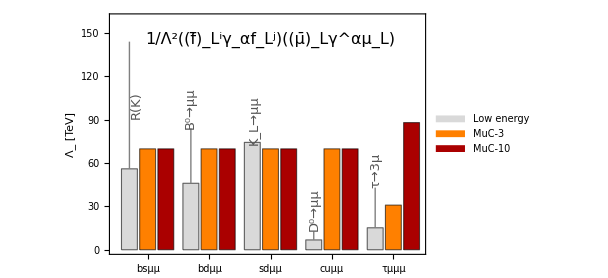
FixPolygons[-Graphics-]

```mathematica
xBARWdth=0.80;
ΔxBAR=0.1;

Show[BarChart[{
Join[{Around[ΛbsFlavlimits,{0,ΛbsFlavlimitsFuture-ΛbsFlavlimits}]},ΛbsMuClimits[[1;;2]]],
Join[{Around[ΛbdFlavlimits,{0,ΛbdFlavlimitsFuture-ΛbdFlavlimits}]},ΛbdMuClimits[[1;;2]]],
Join[{ΛsdFlavlimits},ΛsdMuClimits[[1;;2]]],
Join[{Around[ΛcuFlavlimits,{0,ΛcuFlavlimitsFuture-ΛcuFlavlimits}]},ΛcuMuClimits[[1;;2]]],
Join[{Around[Λτ3μFlavlimits,{0,Λτ3μFlavlimitsFuture-Λτ3μFlavlimits}]},Λτ3μMuClimits[[1;;2]]]},(*ChartStyle->{Orange,LightOrange,Lighter[Green],Green,Cyan,LightBlue},*)
(*ChartStyle->"DarkRainbow",*)
ChartStyle->{LightGray,Orange,Darker[Red]},
IntervalMarkersStyle->Gray,
ChartLegends->Placed[{
Style["Low energy",16,Black,FontFamily->"Times"],
Style["MuC-3",16,Black,FontFamily->"Times"],
Style["MuC-10",16,Black,FontFamily->"Times"](*,
Style["MuC-14",16,Black,FontFamily->"Times"]*)},Above],(*BarSpacing->Medium,*)FrameTicks->{Automatic, Automatic},
ChartLabels->{{"bsμμ","bdμμ","sdμμ","cuμμ","τμμμ"},None},
Frame->True,FrameLabel->{None,"Λ_ [TeV]"},ImageSize->450,AspectRatio->1/GoldenRatio,BaseStyle->Directive[16,FontFamily->"Times"],FrameStyle->Directive[Black],PlotRange->{Automatic,{0,160}}],
(**)
Graphics[Text[Style["1/Λ^2((f̄)_L^iγ_αf_L^j)((μ̄)_Lγ^αμ_L)",16,Black,FontFamily->"Times"],{9,145}]],
(**)
Graphics[ Inset[Rotate[Style["R(K)",13,Darker[Gray],FontFamily->"Times"],90Degree],{1.6,100}]],
Graphics[ Inset[Rotate[Style["B^0→μμ",13,Darker[Gray],FontFamily->"Times"],90Degree],{4.6,98}]],
Graphics[ Inset[Rotate[Style["K_L→μμ",13,Darker[Gray],FontFamily->"Times"],90Degree],{8.1,90}]],
Graphics[ Inset[Rotate[Style["D^0→μμ",13,Darker[Gray],FontFamily->"Times"],90Degree],{11.4,28}]],
Graphics[ Inset[Rotate[Style["τ→3μ",13,Darker[Gray],FontFamily->"Times"],90Degree],{14.8,55}]]
]//FixPolygons
```

```mathematica
Export["Plot/MuC_flavour.pdf",%]
```

Plot/MuC_flavour.pdf

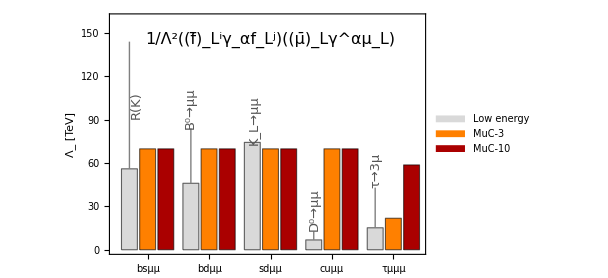
FixPolygons[-Graphics-]

```mathematica
xBARWdth=0.80;
ΔxBAR=0.1;

Show[BarChart[{
Join[{Around[ΛbsFlavlimits,{0,ΛbsFlavlimitsFuture-ΛbsFlavlimits}]},ΛbsMuClimits[[1;;2]]],
Join[{Around[ΛbdFlavlimits,{0,ΛbdFlavlimitsFuture-ΛbdFlavlimits}]},ΛbdMuClimits[[1;;2]]],
Join[{ΛsdFlavlimits},ΛsdMuClimits[[1;;2]]],
Join[{Around[ΛcuFlavlimits,{0,ΛcuFlavlimitsFuture-ΛcuFlavlimits}]},ΛcuMuClimits[[1;;2]]],
Join[{Around[Λτ3μFlavlimits,{0,Λτ3μFlavlimitsFuture-Λτ3μFlavlimits}]},Λτ3μMuClimitsINCL[[1;;2]]]},(*ChartStyle->{Orange,LightOrange,Lighter[Green],Green,Cyan,LightBlue},*)
(*ChartStyle->"DarkRainbow",*)
ChartStyle->{LightGray,Orange,Darker[Red]},
IntervalMarkersStyle->Gray,
ChartLegends->Placed[{
Style["Low energy",16,Black,FontFamily->"Times"],
Style["MuC-3",16,Black,FontFamily->"Times"],
Style["MuC-10",16,Black,FontFamily->"Times"](*,
Style["MuC-14",16,Black,FontFamily->"Times"]*)},Above],(*BarSpacing->Medium,*)FrameTicks->{Automatic, Automatic},
ChartLabels->{{"bsμμ","bdμμ","sdμμ","cuμμ","τμμμ"},None},
Frame->True,FrameLabel->{None,"Λ_ [TeV]"},ImageSize->450,AspectRatio->1/GoldenRatio,BaseStyle->Directive[16,FontFamily->"Times"],FrameStyle->Directive[Black],PlotRange->{Automatic,{0,160}}],
(**)
Graphics[Text[Style["1/Λ^2((f̄)_L^iγ_αf_L^j)((μ̄)_Lγ^αμ_L)",16,Black,FontFamily->"Times"],{9,145}]],
(**)
Graphics[ Inset[Rotate[Style["R(K)",13,Darker[Gray],FontFamily->"Times"],90Degree],{1.6,100}]],
Graphics[ Inset[Rotate[Style["B^0→μμ",13,Darker[Gray],FontFamily->"Times"],90Degree],{4.6,98}]],
Graphics[ Inset[Rotate[Style["K_L→μμ",13,Darker[Gray],FontFamily->"Times"],90Degree],{8.1,90}]],
Graphics[ Inset[Rotate[Style["D^0→μμ",13,Darker[Gray],FontFamily->"Times"],90Degree],{11.4,28}]],
Graphics[ Inset[Rotate[Style["τ→3μ",13,Darker[Gray],FontFamily->"Times"],90Degree],{14.8,55}]]
]//FixPolygons
```

```mathematica
Export["Plot/MuC_flavour_inclLFV.pdf",%]
```

Plot/MuC_flavour_inclLFV.pdf

# Limits on SMEFT coefficients

I work in the down-quark mass basis:  q_i = ( (V^*)_ji  uL_j,  dL_i ) 

I use the Warsaw basis.

## Deriving the LEFT > SMEFT translation and translating the χ^2

### Definitions

```mathematica
dRi={dR,sR,bR};
dLi={dL,sL,bL};
uRi={uR,cR,tR};
uLi={uL,cL,tL};

dRbi={dRb,sRb,bRb};
dLbi={dLb,sLb,bLb};
uRbi={uRb,cRb,tRb};
uLbi={uLb,cLb,tLb};
```

```mathematica
qL[i_]:={Sum[Conjugate[Vv[[j,i]]]uLi[[j]],{j,1,3}],dLi[[i]]};
qLb[i_]:={Sum[Vv[[j,i]]uLbi[[j]],{j,1,3}],dLbi[[i]]};
lL={νμL,μL};
lLb={νμLb,μLb};

LeviCivitaTensor[2]//MatrixForm
```

(0 | 1
-1 | 0)

```mathematica
(qLb[3].qL[3])//Expand
```

bL bLb+cL cLb Vcb Conjugate[Vcb]+cL tLb Vtb Conjugate[Vcb]+cL uLb Vub Conjugate[Vcb]+cLb tL Vcb Conjugate[Vtb]+tL tLb Vtb Conjugate[Vtb]+tL uLb Vub Conjugate[Vtb]+cLb uL Vcb Conjugate[Vub]+tLb uL Vtb Conjugate[Vub]+uL uLb Vub Conjugate[Vub]

### SMEFT operators

```mathematica
Olq1[2,2,i_,j_]:=(lLb.lL)(qLb[i].qL[j])
Olq3[2,2,i_,j_]:=Sum[(lLb.PauliMatrix[a].lL)(qLb[i].PauliMatrix[a].qL[j]),{a,1,3}]

Oeu[2,2,i_,j_]:=μRb μR uRbi[[i]]uRi[[j]]
Oed[2,2,i_,j_]:=μRb μR dRbi[[i]]dRi[[j]]

Olu[2,2,i_,j_]:=(lLb.lL) uRbi[[i]]uRi[[j]]
Old[2,2,i_,j_]:=(lLb.lL) dRbi[[i]]dRi[[j]]
Oqe[i_,j_,2,2]:=(qLb[i].qL[j])μRb μR 

Oledq[2,2,i_,j_]:=lLb.qL[j] dRbi[[i]]μR
Olequ1[2,2,i_,j_]:=lLb.LeviCivitaTensor[2].qLb[i] uRbi[[j]]μR
Olequ3[2,2,i_,j_]:=σμνσμν lLb.LeviCivitaTensor[2].qLb[i] uRbi[[j]]μR

OuB[i_,j_]:=v/(√2)(qLb[i][[1]] uRi[[j]])Bμν
OuW[i_,j_]:=v/(√2)(qLb[i][[1]] uRi[[j]])W3μν
```

```mathematica
(* This list does not contain those coefficients related by conjugation *)
SMEFTCoeffListALLhc=Flatten[Join[
Table[
{Clq1[2,2,i,j],
Clq3[2,2,i,j],
Cqe[i,j,2,2],
Cld[2,2,i,j],
Ced[2,2,i,j],
Cledq[2,2,i,j],
Clu[2,2,i,j],
Ceu[2,2,i,j],
Clequ1[2,2,i,j],
Clequ3[2,2,i,j]}
,{i,1,2},{j,1,2}],
Table[
{Clq1[2,2,i,j],
Clq3[2,2,i,j],
Cqe[i,j,2,2],
Cld[2,2,i,j],
Ced[2,2,i,j],
Cledq[2,2,i,j]}
,{i,{3}},{j,1,2}],
Table[
{Clq1[2,2,i,j],
Clq3[2,2,i,j],
Cqe[i,j,2,2],
Cld[2,2,i,j],
Ced[2,2,i,j],
Cledq[2,2,i,j]}
,{i,1,2},{j,{3}}],
Table[
{Clu[2,2,i,j],
Ceu[2,2,i,j],
Clequ1[2,2,i,j],
Clequ3[2,2,i,j]}
,{i,{3}},{j,1,2}],
Table[
{Clu[2,2,i,j],
Ceu[2,2,i,j],
Clequ1[2,2,i,j],
Clequ3[2,2,i,j]}
,{i,1,2},{j,{3}}],
Table[
{Clq1[2,2,i,j],
Clq3[2,2,i,j],
Cqe[i,j,2,2],
Cld[2,2,i,j],
Ced[2,2,i,j],
Cledq[2,2,i,j],
Clu[2,2,i,j],
Ceu[2,2,i,j],
Clequ1[2,2,i,j],
Clequ3[2,2,i,j]}
,{i,{3}},{j,{3}}],
Table[
{CdB[i,j],CdW[i,j],
CuB[i,j],CuW[i,j]}
,{i,1,3},{j,1,3}]]
];
SMEFTCoeffListALLhc//Length
```

126

```mathematica
hcCoeffList=Flatten[Table[
{Clq1[2,2,i,j],
Clq3[2,2,i,j],
Cqe[i,j,2,2],
Cld[2,2,i,j],
Ced[2,2,i,j],
Clu[2,2,i,j],
Ceu[2,2,i,j]}
,{i,1,3},{j,i+1,3}]]
```

{Clq1[2,2,1,2],Clq3[2,2,1,2],Cqe[1,2,2,2],Cld[2,2,1,2],Ced[2,2,1,2],Clu[2,2,1,2],Ceu[2,2,1,2],Clq1[2,2,1,3],Clq3[2,2,1,3],Cqe[1,3,2,2],Cld[2,2,1,3],Ced[2,2,1,3],Clu[2,2,1,3],Ceu[2,2,1,3],Clq1[2,2,2,3],Clq3[2,2,2,3],Cqe[2,3,2,2],Cld[2,2,2,3],Ced[2,2,2,3],Clu[2,2,2,3],Ceu[2,2,2,3]}

```mathematica
SMEFTCoeffListALL=SMEFTCoeffListALLhc;
For[i=1,i<=Length[hcCoeffList],i++,
SMEFTCoeffListALL=DeleteCases[SMEFTCoeffListALL,hcCoeffList[[i]]];
]
SMEFTCoeffListALL//Length
```

105

```mathematica
SMEFTCoeffListALL
```

{Clq1[2,2,1,1],Clq3[2,2,1,1],Cqe[1,1,2,2],Cld[2,2,1,1],Ced[2,2,1,1],Cledq[2,2,1,1],Clu[2,2,1,1],Ceu[2,2,1,1],Clequ1[2,2,1,1],Clequ3[2,2,1,1],Cledq[2,2,1,2],Clequ1[2,2,1,2],Clequ3[2,2,1,2],Clq1[2,2,2,1],Clq3[2,2,2,1],Cqe[2,1,2,2],Cld[2,2,2,1],Ced[2,2,2,1],Cledq[2,2,2,1],Clu[2,2,2,1],Ceu[2,2,2,1],Clequ1[2,2,2,1],Clequ3[2,2,2,1],Clq1[2,2,2,2],Clq3[2,2,2,2],Cqe[2,2,2,2],Cld[2,2,2,2],Ced[2,2,2,2],Cledq[2,2,2,2],Clu[2,2,2,2],Ceu[2,2,2,2],Clequ1[2,2,2,2],Clequ3[2,2,2,2],Clq1[2,2,3,1],Clq3[2,2,3,1],Cqe[3,1,2,2],Cld[2,2,3,1],Ced[2,2,3,1],Cledq[2,2,3,1],Clq1[2,2,3,2],Clq3[2,2,3,2],Cqe[3,2,2,2],Cld[2,2,3,2],Ced[2,2,3,2],Cledq[2,2,3,2],Cledq[2,2,1,3],Cledq[2,2,2,3],Clu[2,2,3,1],Ceu[2,2,3,1],Clequ1[2,2,3,1],Clequ3[2,2,3,1],Clu[2,2,3,2],Ceu[2,2,3,2],Clequ1[2,2,3,2],Clequ3[2,2,3,2],Clequ1[2,2,1,3],Clequ3[2,2,1,3],Clequ1[2,2,2,3],Clequ3[2,2,2,3],Clq1[2,2,3,3],Clq3[2,2,3,3],Cqe[3,3,2,2],Cld[2,2,3,3],Ced[2,2,3,3],Cledq[2,2,3,3],Clu[2,2,3,3],Ceu[2,2,3,3],Clequ1[2,2,3,3],Clequ3[2,2,3,3],CdB[1,1],CdW[1,1],CuB[1,1],CuW[1,1],CdB[1,2],CdW[1,2],CuB[1,2],CuW[1,2],CdB[1,3],CdW[1,3],CuB[1,3],CuW[1,3],CdB[2,1],CdW[2,1],CuB[2,1],CuW[2,1],CdB[2,2],CdW[2,2],CuB[2,2],CuW[2,2],CdB[2,3],CdW[2,3],CuB[2,3],CuW[2,3],CdB[3,1],CdW[3,1],CuB[3,1],CuW[3,1],CdB[3,2],CdW[3,2],CuB[3,2],CuW[3,2],CdB[3,3],CdW[3,3],CuB[3,3],CuW[3,3]}

```mathematica
SMEFTCoeffListScTens=Flatten[{
Table[{Cledq[2,2,i,j]},{i,1,3},{j,1,3}],
Table[{Clequ1[2,2,i,j],Clequ3[2,2,i,j]},{i,1,3},{j,1,3}]
}];
SMEFTCoeffListScTens//Length
```

27

```mathematica
(* This list does not contain those coefficients related by conjugation *)
SMEFTCoeffList=Flatten[Table[
{Clq1[2,2,i,j],
Clq3[2,2,i,j],
Cqe[i,j,2,2],
Cld[2,2,i,j],
Ced[2,2,i,j],
Clu[2,2,i,j],
Ceu[2,2,i,j]
(*,
Cledq[2,2,i,j],
Clequ1[2,2,i,j],
Clequ3[2,2,i,j]*)}
,{i,1,3},{j,1,i}]];
SMEFTCoeffList//Length
```

42

```mathematica
SMEFTCoeffListScTens=Flatten[{
Table[{Cledq[2,2,i,j]},{i,1,3},{j,1,3}],
Table[{Clequ1[2,2,i,j],Clequ3[2,2,i,j]},{i,1,3},{j,1,3}]
}];
SMEFTCoeffListScTens//Length
```

27

```mathematica
SMEFTCoeffListScTens
```

{Cledq[2,2,1,1],Cledq[2,2,1,2],Cledq[2,2,1,3],Cledq[2,2,2,1],Cledq[2,2,2,2],Cledq[2,2,2,3],Cledq[2,2,3,1],Cledq[2,2,3,2],Cledq[2,2,3,3],Clequ1[2,2,1,1],Clequ3[2,2,1,1],Clequ1[2,2,1,2],Clequ3[2,2,1,2],Clequ1[2,2,1,3],Clequ3[2,2,1,3],Clequ1[2,2,2,1],Clequ3[2,2,2,1],Clequ1[2,2,2,2],Clequ3[2,2,2,2],Clequ1[2,2,2,3],Clequ3[2,2,2,3],Clequ1[2,2,3,1],Clequ3[2,2,3,1],Clequ1[2,2,3,2],Clequ3[2,2,3,2],Clequ1[2,2,3,3],Clequ3[2,2,3,3]}

```mathematica
SMEFTCoeffListDipoles=Flatten[{
Table[{CdB[i,j],CdW[i,j]},{i,1,3},{j,1,3}],
Table[{CuB[i,j],CuW[i,j]},{i,1,3},{j,1,3}]
}];
SMEFTCoeffListDipoles//Length
SMEFTCoeffListDipoles
```

36

{CdB[1,1],CdW[1,1],CdB[1,2],CdW[1,2],CdB[1,3],CdW[1,3],CdB[2,1],CdW[2,1],CdB[2,2],CdW[2,2],CdB[2,3],CdW[2,3],CdB[3,1],CdW[3,1],CdB[3,2],CdW[3,2],CdB[3,3],CdW[3,3],CuB[1,1],CuW[1,1],CuB[1,2],CuW[1,2],CuB[1,3],CuW[1,3],CuB[2,1],CuW[2,1],CuB[2,2],CuW[2,2],CuB[2,3],CuW[2,3],CuB[3,1],CuW[3,1],CuB[3,2],CuW[3,2],CuB[3,3],CuW[3,3]}

```mathematica
SMEFThcRelation=Flatten[Table[
If[i<j,{Clq1[2,2,i,j]->Conjugate[Clq1[2,2,j,i]],
Clq3[2,2,i,j]->Conjugate[Clq3[2,2,j,i]],
Ceu[2,2,i,j]->Conjugate[Ceu[2,2,j,i]],
Ced[2,2,i,j]->Conjugate[Ced[2,2,j,i]],
Clu[2,2,i,j]->Conjugate[Clu[2,2,j,i]],
Cld[2,2,i,j]->Conjugate[Cld[2,2,j,i]],
Cqe[i,j,2,2]->Conjugate[Cqe[j,i,2,2]]},{}]
,{i,1,3},{j,1,3}]]
```

{Clq1[2,2,1,2]→Conjugate[Clq1[2,2,2,1]],Clq3[2,2,1,2]→Conjugate[Clq3[2,2,2,1]],Ceu[2,2,1,2]→Conjugate[Ceu[2,2,2,1]],Ced[2,2,1,2]→Conjugate[Ced[2,2,2,1]],Clu[2,2,1,2]→Conjugate[Clu[2,2,2,1]],Cld[2,2,1,2]→Conjugate[Cld[2,2,2,1]],Cqe[1,2,2,2]→Conjugate[Cqe[2,1,2,2]],Clq1[2,2,1,3]→Conjugate[Clq1[2,2,3,1]],Clq3[2,2,1,3]→Conjugate[Clq3[2,2,3,1]],Ceu[2,2,1,3]→Conjugate[Ceu[2,2,3,1]],Ced[2,2,1,3]→Conjugate[Ced[2,2,3,1]],Clu[2,2,1,3]→Conjugate[Clu[2,2,3,1]],Cld[2,2,1,3]→Conjugate[Cld[2,2,3,1]],Cqe[1,3,2,2]→Conjugate[Cqe[3,1,2,2]],Clq1[2,2,2,3]→Conjugate[Clq1[2,2,3,2]],Clq3[2,2,2,3]→Conjugate[Clq3[2,2,3,2]],Ceu[2,2,2,3]→Conjugate[Ceu[2,2,3,2]],Ced[2,2,2,3]→Conjugate[Ced[2,2,3,2]],Clu[2,2,2,3]→Conjugate[Clu[2,2,3,2]],Cld[2,2,2,3]→Conjugate[Cld[2,2,3,2]],Cqe[2,3,2,2]→Conjugate[Cqe[3,2,2,2]]}

```mathematica
LSMEFTsemileptonic=Sum[
Clq1[2,2,i,j]Olq1[2,2,i,j]+
Clq3[2,2,i,j]Olq3[2,2,i,j]+
Ceu[2,2,i,j]Oeu[2,2,i,j]+
Ced[2,2,i,j]Oed[2,2,i,j]+
Clu[2,2,i,j]Olu[2,2,i,j]+
Cld[2,2,i,j]Old[2,2,i,j]+
Cqe[i,j,2,2]Oqe[i,j,2,2]
,{i,1,3},{j,1,3}]/.SMEFThcRelation;
```

```mathematica
LSMEFTupDipoles=Sum[
CuB[i,j]OuB[i,j]+CuW[i,j]OuW[i,j]
,{i,1,3},{j,1,3}]/.{W3μν->cθW Zμν + sθW Fμν,Bμν->-sθW Zμν + cθW Fμν};
```

```mathematica
LSMEFTsemileptonic/.SMpointSMEFT
```

0

```mathematica
LSMEFTupDipoles/.SMpointSMEFT
```

0

### LEFT > SMEFT Translation

The v^2/TeV^2 factor is needed because I defined the LEFT coefficients as Cc/v^2 [operator], while now I want to use SMEFT coefficients defined as C/TeV^2 [operator].

```mathematica
LEFTtoSMEFT=Flatten[Join[
Table[
{Cc[dRi[[i]],dRi[[j]],μR]->v^2/TeV^2 Coefficient[LSMEFTsemileptonic,dRbi[[i]]dRi[[j]]μRb μR ]},
{i,1,3},{j,1,3}],
Table[
{Cc[dRi[[i]],dRi[[j]],μL]->v^2/TeV^2 Coefficient[LSMEFTsemileptonic,dRbi[[i]]dRi[[j]]μLb μL ]},
{i,1,3},{j,1,3}],
Table[
{Cc[dLi[[i]],dLi[[j]],μR]->v^2/TeV^2 Coefficient[LSMEFTsemileptonic,dLbi[[i]]dLi[[j]]μRb μR ]},
{i,1,3},{j,1,3}],
Table[
{Cc[dLi[[i]],dLi[[j]],μL]->v^2/TeV^2 Coefficient[LSMEFTsemileptonic,dLbi[[i]]dLi[[j]]μLb μL ]},
{i,1,3},{j,1,3}],
Table[
{Cc[uRi[[i]],uRi[[j]],μR]->v^2/TeV^2 Coefficient[LSMEFTsemileptonic,uRbi[[i]]uRi[[j]]μRb μR ]},
{i,1,3},{j,1,3}],
Table[
{Cc[uRi[[i]],uRi[[j]],μL]->v^2/TeV^2 Coefficient[LSMEFTsemileptonic,uRbi[[i]]uRi[[j]]μLb μL ]},
{i,1,3},{j,1,3}],
Table[
{Cc[uLi[[i]],uLi[[j]],μR]->v^2/TeV^2 Coefficient[LSMEFTsemileptonic,uLbi[[i]]uLi[[j]]μRb μR ]},
{i,1,3},{j,1,3}],
Table[
{Cc[uLi[[i]],uLi[[j]],μL]->v^2/TeV^2 Coefficient[LSMEFTsemileptonic,uLbi[[i]]uLi[[j]]μLb μL ]},
{i,1,3},{j,1,3}],
Table[{Cledq[2,2,i,j]->1/TeV^2 Cledq[2,2,i,j]},{i,1,3},{j,1,3}],
Table[{Clequ1[2,2,i,j]->1/TeV^2 Clequ1[2,2,i,j]},{i,1,3},{j,1,3}],
Table[{Clequ3[2,2,i,j]->1/TeV^2 Clequ3[2,2,i,j]},{i,1,3},{j,1,3}],
Table[{Ceγ[i,j]->1/TeV^2 v/(√2)(cθW CeB[i,j]+sθW CeW[i,j]),CeZ[i_,j_]->1/TeV^2 v/(√2)(-sθW CeB[i,j]+cθW CeW[i,j])},
{i,1,3},{j,1,3}],
Table[{Cdγ[i,j]->1/TeV^2 v/(√2)(cθW CdB[i,j]+sθW CdW[i,j]),CdZ[i_,j_]->1/TeV^2 v/(√2)(-sθW CdB[i,j]+cθW CdW[i,j])},
{i,1,3},{j,1,3}],
Table[
{CuZ[i,j]->1/TeV^2 Coefficient[LSMEFTupDipoles,uLbi[[i]]uRi[[j]]Zμν ],
Cuγ[i,j]->1/TeV^2 Coefficient[LSMEFTupDipoles,uLbi[[i]]uRi[[j]]Fμν ]},
{i,1,3},{j,1,3}]
]]/.{sθW->√sWSQ[10TeV],cθW->√(1-sWSQ[10TeV])};
```

```mathematica
Cc[bL,sL,μL]/.LEFTtoSMEFT
```

(v^2 (Clq1[2,2,3,2]+Clq3[2,2,3,2]))/1000000

```mathematica
Table[{Clequ3[2,2,i,j]->1/TeV^2 Clequ3[2,2,i,j]},{i,1,3},{j,1,3}]
```

{{{Clequ3[2,2,1,1]→Clequ3[2,2,1,1]/1000000},{Clequ3[2,2,1,2]→Clequ3[2,2,1,2]/1000000},{Clequ3[2,2,1,3]→Clequ3[2,2,1,3]/1000000}},{{Clequ3[2,2,2,1]→Clequ3[2,2,2,1]/1000000},{Clequ3[2,2,2,2]→Clequ3[2,2,2,2]/1000000},{Clequ3[2,2,2,3]→Clequ3[2,2,2,3]/1000000}},{{Clequ3[2,2,3,1]→Clequ3[2,2,3,1]/1000000},{Clequ3[2,2,3,2]→Clequ3[2,2,3,2]/1000000},{Clequ3[2,2,3,3]→Clequ3[2,2,3,3]/1000000}}}

```mathematica
Table[Cdγ[i_,j_]->1/TeV^2 v/(√2)(cθW CdB[i,j]+sθW CdW[i,j]),
{i,1,3},{j,1,3}]
```

{{Cdγ[i_,j_]→(v (cθW CdB[1,1]+sθW CdW[1,1]))/(1000000 √2),Cdγ[i_,j_]→(v (cθW CdB[1,2]+sθW CdW[1,2]))/(1000000 √2),Cdγ[i_,j_]→(v (cθW CdB[1,3]+sθW CdW[1,3]))/(1000000 √2)},{Cdγ[i_,j_]→(v (cθW CdB[2,1]+sθW CdW[2,1]))/(1000000 √2),Cdγ[i_,j_]→(v (cθW CdB[2,2]+sθW CdW[2,2]))/(1000000 √2),Cdγ[i_,j_]→(v (cθW CdB[2,3]+sθW CdW[2,3]))/(1000000 √2)},{Cdγ[i_,j_]→(v (cθW CdB[3,1]+sθW CdW[3,1]))/(1000000 √2),Cdγ[i_,j_]→(v (cθW CdB[3,2]+sθW CdW[3,2]))/(1000000 √2),Cdγ[i_,j_]→(v (cθW CdB[3,3]+sθW CdW[3,3]))/(1000000 √2)}}

```mathematica
Coefficient[LSMEFTsemileptonic,bLb sL μLb μL]
```

Clq1[2,2,3,2]+Clq3[2,2,3,2]

```mathematica
Coefficient[LSMEFTsemileptonic,bLb sL νμLb νμL]
```

Clq1[2,2,3,2]-Clq3[2,2,3,2]

```mathematica
Cdγ[1,3]/.LEFTtoSMEFT
```

(v (0.862922 CdB[1,3]+0.505336 CdW[1,3]))/(1000000 √2)

```mathematica
Cuγ[3,3]/.LEFTtoSMEFT
```

(0.610178 v Vtd CuB[1,3]+0.610178 v Vts CuB[2,3]+0.610178 v Vtb CuB[3,3]+0.357327 v Vtd CuW[1,3]+0.357327 v Vts CuW[2,3]+0.357327 v Vtb CuW[3,3])/1000000

### Translating the χ^2

```mathematica
Lumi30TeV
```

90000

```mathematica
χSQjjMuC3BinsSMEFT=χSQjjMuC3Bins/.LEFTtoSMEFT/.VNum/.NumValues/.syst->0.2/100;
```

```mathematica
χSQjjMuC3SMEFT=χSQjjMuC3ηBins/.LEFTtoSMEFT/.VNum/.NumValues/.syst->0.2/100;
```

```mathematica
χSQjjMuC7BinsSMEFT=χSQjjMuC7Bins/.LEFTtoSMEFT/.VNum/.NumValues/.syst->0.2/100;
```

```mathematica
χSQjjMuC7SMEFT=χSQjjMuC7ηBins/.LEFTtoSMEFT/.VNum/.NumValues/.syst->0.2/100;
```

```mathematica
χSQjjMuC10BinsSMEFT=χSQjjMuC10Bins/.LEFTtoSMEFT/.VNum/.NumValues/.syst->0.2/100;
```

```mathematica
χSQjjMuC10SMEFT=χSQjjMuC10ηBins/.LEFTtoSMEFT/.VNum/.NumValues/.syst->0.2/100;
```

```mathematica
χSQjjMuC30BinsSMEFT=χSQjjMuC30Bins/.LEFTtoSMEFT/.VNum/.NumValues/.syst->0.2/100;
```

```mathematica
χSQjjMuC30SMEFT=χSQjjMuC30ηBins/.LEFTtoSMEFT/.VNum/.NumValues/.syst->0.2/100;
```

```mathematica
χSQjjMuC10SMEFT/.{Cledq[2,2,3,3]->cc}/.SMpointSMEFT//ComplexExpand//Chop
```

5.05836×10^-7 cc^2+5.86589×10^15 cc^4

```mathematica
χSQjjMuC10BinsSMEFT/.{Cledq[2,2,3,3]->cc}/.SMpointSMEFT//ComplexExpand//Chop
```

{6.65124×10^11 cc^4,1.39501×10^-8 cc^2+6.78466×10^12 cc^4,2.80403×10^-9 cc^2+3.40937×10^10 cc^4,5.27429×10^15 cc^4,3.13311×10^-7 cc^2+3.04759×10^14 cc^4,2.52024×10^-8 cc^2+1.9152×10^12 cc^4,1.60743×10^12 cc^4,3.43029×10^10 cc^4}

```mathematica
SMEFTCoeffList
```

{Clq1[2,2,1,1],Clq3[2,2,1,1],Cqe[1,1,2,2],Cld[2,2,1,1],Ced[2,2,1,1],Clu[2,2,1,1],Ceu[2,2,1,1],Clq1[2,2,2,1],Clq3[2,2,2,1],Cqe[2,1,2,2],Cld[2,2,2,1],Ced[2,2,2,1],Clu[2,2,2,1],Ceu[2,2,2,1],Clq1[2,2,2,2],Clq3[2,2,2,2],Cqe[2,2,2,2],Cld[2,2,2,2],Ced[2,2,2,2],Clu[2,2,2,2],Ceu[2,2,2,2],Clq1[2,2,3,1],Clq3[2,2,3,1],Cqe[3,1,2,2],Cld[2,2,3,1],Ced[2,2,3,1],Clu[2,2,3,1],Ceu[2,2,3,1],Clq1[2,2,3,2],Clq3[2,2,3,2],Cqe[3,2,2,2],Cld[2,2,3,2],Ced[2,2,3,2],Clu[2,2,3,2],Ceu[2,2,3,2],Clq1[2,2,3,3],Clq3[2,2,3,3],Cqe[3,3,2,2],Cld[2,2,3,3],Ced[2,2,3,3],Clu[2,2,3,3],Ceu[2,2,3,3]}

```mathematica
SMEFTCoeffListScTens
```

{Cledq[2,2,1,1],Cledq[2,2,1,2],Cledq[2,2,1,3],Cledq[2,2,2,1],Cledq[2,2,2,2],Cledq[2,2,2,3],Cledq[2,2,3,1],Cledq[2,2,3,2],Cledq[2,2,3,3],Clequ1[2,2,1,1],Clequ3[2,2,1,1],Clequ1[2,2,1,2],Clequ3[2,2,1,2],Clequ1[2,2,1,3],Clequ3[2,2,1,3],Clequ1[2,2,2,1],Clequ3[2,2,2,1],Clequ1[2,2,2,2],Clequ3[2,2,2,2],Clequ1[2,2,2,3],Clequ3[2,2,2,3],Clequ1[2,2,3,1],Clequ3[2,2,3,1],Clequ1[2,2,3,2],Clequ3[2,2,3,2],Clequ1[2,2,3,3],Clequ3[2,2,3,3]}

```mathematica
SMEFTCoeffListDipoles
```

{CdB[1,1],CdW[1,1],CdB[1,2],CdW[1,2],CdB[1,3],CdW[1,3],CdB[2,1],CdW[2,1],CdB[2,2],CdW[2,2],CdB[2,3],CdW[2,3],CdB[3,1],CdW[3,1],CdB[3,2],CdW[3,2],CdB[3,3],CdW[3,3],CuB[1,1],CuW[1,1],CuB[1,2],CuW[1,2],CuB[1,3],CuW[1,3],CuB[2,1],CuW[2,1],CuB[2,2],CuW[2,2],CuB[2,3],CuW[2,3],CuB[3,1],CuW[3,1],CuB[3,2],CuW[3,2],CuB[3,3],CuW[3,3]}

```mathematica
Export["chiSQjjSMEFT3TeV_bins.m",χSQjjMuC3BinsSMEFT]
```

chiSQjjSMEFT3TeV_bins.m

```mathematica
Export["chiSQjjSMEFT3TeV_tot.m",χSQjjMuC3SMEFT]
```

chiSQjjSMEFT3TeV_tot.m

```mathematica
Export["chiSQjjSMEFT7TeV_bins.m",χSQjjMuC7BinsSMEFT]
```

chiSQjjSMEFT7TeV_bins.m

```mathematica
Export["chiSQjjSMEFT7TeV_tot.m",χSQjjMuC7SMEFT]
```

chiSQjjSMEFT7TeV_tot.m

```mathematica
Export["chiSQjjSMEFT10TeV_bins.m",χSQjjMuC10BinsSMEFT]
```

chiSQjjSMEFT10TeV_bins.m

```mathematica
Export["chiSQjjSMEFT10TeV_tot.m",χSQjjMuC10SMEFT]
```

chiSQjjSMEFT10TeV_tot.m

```mathematica
Export["chiSQjjSMEFT30TeV_bins.m",χSQjjMuC30BinsSMEFT]
```

chiSQjjSMEFT30TeV_bins.m

```mathematica
Export["chiSQjjSMEFT30TeV_tot.m",χSQjjMuC30SMEFT]
```

chiSQjjSMEFT30TeV_tot.m

### Prove

```mathematica
LSMEFTsemileptonic/.{Clq1[2,2,1,1]->cc}/.SMpointSMEFT//Expand//Simplify
```

cc (μL μLb+νμL νμLb) (dL dLb+cL (cLb Vcd+tLb Vtd+uLb Vud) Conjugate[Vcd]+tL (cLb Vcd+tLb Vtd+uLb Vud) Conjugate[Vtd]+cLb uL Vcd Conjugate[Vud]+tLb uL Vtd Conjugate[Vud]+uL uLb Vud Conjugate[Vud])

```mathematica
LSMEFTsemileptonic/.{Clq3[2,2,1,1]->cc}/.SMpointSMEFT//Expand//Simplify
```

cc (dL dLb μL μLb+2 cLb dL Vcd μLb νμL+2 dL tLb Vtd μLb νμL+2 dL uLb Vud μLb νμL-dL dLb νμL νμLb+cL (-cLb Vcd μL μLb-tLb Vtd μL μLb-uLb Vud μL μLb+2 dLb μL νμLb+cLb Vcd νμL νμLb+tLb Vtd νμL νμLb+uLb Vud νμL νμLb) Conjugate[Vcd]+tL (-cLb Vcd μL μLb-tLb Vtd μL μLb-uLb Vud μL μLb+2 dLb μL νμLb+cLb Vcd νμL νμLb+tLb Vtd νμL νμLb+uLb Vud νμL νμLb) Conjugate[Vtd]-cLb uL Vcd μL μLb Conjugate[Vud]-tLb uL Vtd μL μLb Conjugate[Vud]-uL uLb Vud μL μLb Conjugate[Vud]+2 dLb uL μL νμLb Conjugate[Vud]+cLb uL Vcd νμL νμLb Conjugate[Vud]+tLb uL Vtd νμL νμLb Conjugate[Vud]+uL uLb Vud νμL νμLb Conjugate[Vud])

```mathematica
{Cc[dL,dL,μL]/.LEFTtoSMEFT/.{Clq1[2,2,1,1]->cc}/.SMpointSMEFT,Cc[dL,dL,μL]/.LEFTtoSMEFT/.{Clq3[2,2,1,1]->cc}/.SMpointSMEFT}
```

{(cc v^2)/1000000,(cc v^2)/1000000}

```mathematica
{Cc[uL,uL,μL]/.LEFTtoSMEFT/.{Clq1[2,2,1,1]->cc}/.SMpointSMEFT//Simplify,Cc[uL,uL,μL]/.LEFTtoSMEFT/.{Clq3[2,2,1,1]->cc}/.SMpointSMEFT//Simplify}
```

{(cc v^2 Vud Conjugate[Vud])/1000000,-(cc v^2 Vud Conjugate[Vud])/1000000}

```mathematica
σDipuu[3,3,10]/.LEFTtoSMEFT/.{CuB[3,3]->1/10^2}/.SMpointSMEFT/.VNum/.NumValues
```

0.0157757 λEFTsq

```mathematica
Lumi10TeV
```

10000

```mathematica
((NttBSM[10,Lumi10TeV]-NttSM[10,Lumi10TeV])/(√NttSM[10,Lumi10TeV]))^2/.LEFTtoSMEFT/.{CuB[3,3]->1/(Λ)^2}/.VNum/.NumValues/.SMpointSMEFT/.Λ->8.1
```

4.8735-3.86373×10^-23 ⅈ

```mathematica
((NttBSM[10,Lumi10TeV]-NttSM[10,Lumi10TeV])/(√NttSM[10,Lumi10TeV]))^2/.LEFTtoSMEFT/.{CuB[3,3]->1/(Λ)^2}/.VNum/.NumValues/.SMpointSMEFT/.Λ->8.1
```

4.8735-3.86373×10^-23 ⅈ

```mathematica
{σccSM,σjjSM}=(1/Lumi{NccBSM[10,Lumi],NjjBSM[10,Lumi]}/.SMpoint//ComplexExpand//Chop)
```

{0.246979,1.69044}

```mathematica
1/Lumi 1/σjjSM NjjBSM[10,Lumi]
```

```mathematica
({1/Lumi 1/σccSM NccBSM[10,Lumi]-1,1/Lumi 1/σjjSM NjjBSM[10,Lumi]-1}/.LEFTtoSMEFT/.{Ceu[2,2,1,1]->ceu2211}/.VNum/.NumValues/.SMpointSMEFT//ComplexExpand//Chop)/.ceu2211->1/100^2
```

{-0.000154274,-0.048737}

```mathematica
%/.clq32211->1/200.^2
```

{-0.000154274,-0.048737}

```mathematica
((NttBSM[10,Lumi10TeV]-NttSM[10,Lumi10TeV])/(√NttSM[10,Lumi10TeV]))^2/.LEFTtoSMEFT/.{CuB[3,3]->1/(Λ)^2}/.VNum/.NumValues/.SMpointSMEFT/.Λ->8.1
```

4.8735-3.86373×10^-23 ⅈ

## Prove per confronto con Alfredo

```mathematica
σBSMμμtt[10]/.SMpoint
```

0.968235+7.6695×10^-24 ⅈ

```mathematica
1/Lumi10TeV NWW[10,Lumi10TeV]
```

NWW[10,10000]/10000

```mathematica
σBSMμμqqbTLLRR[uR,uR,μR,10TeV]/.SMpoint
```

0.485099+5.2474×10^-31 ⅈ

```mathematica
(σBSMμμqqbTLLRR[uR,uR,μR,10TeV]/.LEFTtoSMEFT/.{Ceu[2,2,1,1]->ceu2211}/.VNum/.NumValues/.SMpointSMEFT//ComplexExpand//Chop)
```

0.485099-1080.82 ceu2211+602030. ceu2211^2 λEFTsq

```mathematica
(σBSMμμqqbTLLRR[uL,uL,μR,10TeV]/.LEFTtoSMEFT/.{Cqe[1,1,2,2]->cc}/.VNum/.NumValues/.SMpointSMEFT//ComplexExpand//Chop)
```

0.0228829-193.637 cc+409641. cc^2 λEFTsq

```mathematica
(σBSMμμqqbTLLRR[uL,uL,μL,10TeV]/.LEFTtoSMEFT/.{Clq1[2,2,1,1]->clq1}/.VNum/.NumValues/.SMpointSMEFT//ComplexExpand//Chop)
```

0.432899-751.442 clq1+326095. clq1^2 λEFTsq

```mathematica
σBSMμμqqbTLLRR[uL,uL,μL,10TeV]/.LEFTtoSMEFT
```

3.61845×10^17 ((1.19637×10^-18+2.27982×10^-41 ⅈ)-(1.8042×10^-20+1.59664×10^-26 ⅈ) v^2 (Vub Clq1[2,2,3,3] Conjugate[Vub]-Vub Clq3[2,2,3,3] Conjugate[Vub]+Vud Clq1[2,2,1,1] Conjugate[Vud]+Vus Clq1[2,2,2,1] Conjugate[Vud]+Vub Clq1[2,2,3,1] Conjugate[Vud]-Vud Clq3[2,2,1,1] Conjugate[Vud]-Vus Clq3[2,2,2,1] Conjugate[Vud]-Vub Clq3[2,2,3,1] Conjugate[Vud]+Vus Clq1[2,2,2,2] Conjugate[Vus]+Vub Clq1[2,2,3,2] Conjugate[Vus]-Vus Clq3[2,2,2,2] Conjugate[Vus]-Vub Clq3[2,2,3,2] Conjugate[Vus]+Vud Conjugate[Vus] Conjugate[Clq1[2,2,2,1]]+Vud Conjugate[Vub] Conjugate[Clq1[2,2,3,1]]+Vus Conjugate[Vub] Conjugate[Clq1[2,2,3,2]]-Vud Conjugate[Vus] Conjugate[Clq3[2,2,2,1]]-Vud Conjugate[Vub] Conjugate[Clq3[2,2,3,1]]-Vus Conjugate[Vub] Conjugate[Clq3[2,2,3,2]])-(1.8042×10^-20-1.59664×10^-26 ⅈ) Conjugate[v]^2 (Vus Clq1[2,2,2,1] Conjugate[Vud]+Vub Clq1[2,2,3,1] Conjugate[Vud]-Vus Clq3[2,2,2,1] Conjugate[Vud]-Vub Clq3[2,2,3,1] Conjugate[Vud]+Vub Clq1[2,2,3,2] Conjugate[Vus]-Vub Clq3[2,2,3,2] Conjugate[Vus]+Vud Conjugate[Vud Clq1[2,2,1,1]]+Vud Conjugate[Vus Clq1[2,2,2,1]]+Vus Conjugate[Vus Clq1[2,2,2,2]]+Vud Conjugate[Vub Clq1[2,2,3,1]]+Vus Conjugate[Vub Clq1[2,2,3,2]]+Vub Conjugate[Vub Clq1[2,2,3,3]]-Vud Conjugate[Vud Clq3[2,2,1,1]]-Vud Conjugate[Vus Clq3[2,2,2,1]]-Vus Conjugate[Vus Clq3[2,2,2,2]]-Vud Conjugate[Vub Clq3[2,2,3,1]]-Vus Conjugate[Vub Clq3[2,2,3,2]]-Vub Conjugate[Vub Clq3[2,2,3,3]])+2.72086×10^-22 v^2 λEFTsq Conjugate[v]^2 (Vub Clq1[2,2,3,3] Conjugate[Vub]-Vub Clq3[2,2,3,3] Conjugate[Vub]+Vud Clq1[2,2,1,1] Conjugate[Vud]+Vus Clq1[2,2,2,1] Conjugate[Vud]+Vub Clq1[2,2,3,1] Conjugate[Vud]-Vud Clq3[2,2,1,1] Conjugate[Vud]-Vus Clq3[2,2,2,1] Conjugate[Vud]-Vub Clq3[2,2,3,1] Conjugate[Vud]+Vus Clq1[2,2,2,2] Conjugate[Vus]+Vub Clq1[2,2,3,2] Conjugate[Vus]-Vus Clq3[2,2,2,2] Conjugate[Vus]-Vub Clq3[2,2,3,2] Conjugate[Vus]+Vud Conjugate[Vus] Conjugate[Clq1[2,2,2,1]]+Vud Conjugate[Vub] Conjugate[Clq1[2,2,3,1]]+Vus Conjugate[Vub] Conjugate[Clq1[2,2,3,2]]-Vud Conjugate[Vus] Conjugate[Clq3[2,2,2,1]]-Vud Conjugate[Vub] Conjugate[Clq3[2,2,3,1]]-Vus Conjugate[Vub] Conjugate[Clq3[2,2,3,2]]) (Vus Clq1[2,2,2,1] Conjugate[Vud]+Vub Clq1[2,2,3,1] Conjugate[Vud]-Vus Clq3[2,2,2,1] Conjugate[Vud]-Vub Clq3[2,2,3,1] Conjugate[Vud]+Vub Clq1[2,2,3,2] Conjugate[Vus]-Vub Clq3[2,2,3,2] Conjugate[Vus]+Vud Conjugate[Vud Clq1[2,2,1,1]]+Vud Conjugate[Vus Clq1[2,2,2,1]]+Vus Conjugate[Vus Clq1[2,2,2,2]]+Vud Conjugate[Vub Clq1[2,2,3,1]]+Vus Conjugate[Vub Clq1[2,2,3,2]]+Vub Conjugate[Vub Clq1[2,2,3,3]]-Vud Conjugate[Vud Clq3[2,2,1,1]]-Vud Conjugate[Vus Clq3[2,2,2,1]]-Vus Conjugate[Vus Clq3[2,2,2,2]]-Vud Conjugate[Vub Clq3[2,2,3,1]]-Vus Conjugate[Vub Clq3[2,2,3,2]]-Vub Conjugate[Vub Clq3[2,2,3,3]]))

```mathematica
(σBSMμμqqbTLLRR[uR,uR,μR,10TeV]/.LEFTtoSMEFT/.{Ceu[2,2,1,1]->ceu2211}/.VNum/.NumValues/.SMpointSMEFT//ComplexExpand//Chop)/.ceu2211->1/100^2
```

0.377016+0.0060203 λEFTsq

```mathematica
σBSMμμuu[10]/.LEFTtoSMEFT/.{Ceu[2,2,1,1]->ceu2211}/.VNum/.NumValues/.SMpointSMEFT//ComplexExpand//Chop
```

0.968235-1008.75 ceu2211+561886. ceu2211^2 λEFTsq

```mathematica
σBSMμμuu[10]/.{Ceu[2,2,1,1]->ceu2211}/.SMpointSMEFT/.SMpoint
```

0.968235+7.6695×10^-24 ⅈ

```mathematica
NttBSM[10,Lumi10TeV]
```

```mathematica
χSQprova=((NttBSM[10,Lumi10TeV]-NttSM[10,Lumi10TeV])/(√NttSM[10,Lumi10TeV]))^2/.LEFTtoSMEFT/.{Ceu[2,2,3,3]->ceu2233}/.VNum/.NumValues/.SMpointSMEFT//ComplexExpand//Chop
```

-9.33856×10^-10 ceu2233+3.72878×10^9 ceu2233^2-4.15394×10^12 ceu2233^3+(1.1569×10^15-9.17191×10^-9 ⅈ) ceu2233^4

```mathematica
Abs[Chop[ceu2233/.FindRoot[χSQprova==χSQ1d95,{ceu2233,-10^-4}]]]^(-1/2)
```

178.053

```mathematica
Abs[Chop[ceu2233/.FindRoot[χSQprova==χSQ1d95,{ceu2233,10^-4}]]]^(-1/2)
```

174.895

```mathematica
χSQ1d68
```

0.988946

```mathematica
Abs[Chop[ceu2233/.FindRoot[χSQprova==χSQ1d68,{ceu2233,-10^-4}]]]^(-1/2)
```

248.91

```mathematica
Block[{χsqtmp},
χsqtmp=Chop[χSQjjMuC10SMEFT/.syst->0.2/100/.{Ceu[2,2,3,3]->cc}/.SMpointSMEFT//Expand,10^-15];
{Ceu[2,2,3,3],Abs[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]]^(-1/2),Abs[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]]^(-1/2)}
]
```

{Ceu[2,2,3,3],180.51,177.396}

```mathematica
Block[{χsqtmp},
χsqtmp=Chop[χSQjjMuC10SMEFT/.syst->0.2/100/.{Ceu[2,2,3,3]->cc}/.SMpointSMEFT//Expand,10^-15];
{Ceu[2,2,3,3],Abs[cc/.FindRoot[χsqtmp==χSQ1d68,{cc,-10^-4}]]^(-1/2),Abs[cc/.FindRoot[χsqtmp==χSQ1d68,{cc,10^-4}]]^(-1/2)}
]
```

{Ceu[2,2,3,3],252.373,250.156}

```mathematica
Block[{χsqtmp},
χsqtmp=Chop[χSQjjMuC10SMEFT/.syst->0.2/100/.{Clq3[2,2,1,1]->cc}/.SMpointSMEFT//Expand,10^-15];
{Ceu[2,2,3,3],Abs[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}]]^(-1/2),Abs[cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]]^(-1/2)}
]
```

{Ceu[2,2,3,3],212.587,214.963}

```mathematica
Block[{χsqtmp},
χsqtmp=Chop[χSQjjMuC10SMEFT/.syst->0.2/100/.{Clq3[2,2,1,1]->cc}/.SMpointSMEFT//Expand,10^-15];
{Clq3[2,2,1,1],Abs[cc/.FindRoot[χsqtmp==χSQ1d68,{cc,-10^-4}]]^(-1/2),Abs[cc/.FindRoot[χsqtmp==χSQ1d68,{cc,10^-4}]]^(-1/2)}
]
```

{Clq3[2,2,1,1],299.286,300.978}

```mathematica
Block[{χsqtmp},
χsqtmp=Chop[χSQjjMuC10SMEFT/.syst->0.2/100/.{Clq3[2,2,1,1]->cc,Clq3[2,2,2,2]->cc}/.SMpointSMEFT//Expand,10^-15];
{Clq3[2,2,1,1],Abs[cc/.FindRoot[χsqtmp==χSQ1d68,{cc,-10^-4}]]^(-1/2),Abs[cc/.FindRoot[χsqtmp==χSQ1d68,{cc,10^-4}]]^(-1/2)}
]
```

{Clq3[2,2,1,1],395.476,396.774}

```mathematica
Block[{χsqtmp},
χsqtmp=Chop[χSQjjMuC10SMEFT/.syst->0.2/100/.{Clq3[2,2,2,1]->cc}/.SMpointSMEFT//Expand,10^-15];
{Clq3[2,2,1,1],Abs[cc/.FindRoot[χsqtmp==χSQ1d68,{cc,-10^-4}]]^(-1/2),Abs[cc/.FindRoot[χsqtmp==χSQ1d68,{cc,10^-4}]]^(-1/2)}
]
```

{Clq3[2,2,1,1],174.232,175.918}

```mathematica
1/βISR σBSMμμuu[10]/.LEFTtoSMEFT/.{Clq3[2,2,1,1]->clq32211}/.VNum/.NumValues/.SMpointSMEFT//ComplexExpand//Chop
```

0.968235+701.336 clq32211+304351. clq32211^2 λEFTsq

```mathematica
1/βISR(σBSMμμqqbTLLRR[dL,dL,μL,10TeV]+σBSMμμqqbTLLRR[dL,dL,μR,10TeV]+σBSMμμqqbTLLRR[dR,dR,μL,10TeV]+σBSMμμqqbTLLRR[dR,dR,μR,10TeV])/.LEFTtoSMEFT/.{Clq3[2,2,1,1]->clq32211}/.VNum/.NumValues/.SMpointSMEFT//ComplexExpand//Chop
```

0.449702+629.166 clq32211+361845. clq32211^2 λEFTsq

### Top Dipole operators

```mathematica
σDipuu[3,3,10]
```

1.54884×10^26 λEFTsq Abs[-1.77651×10^-9 Conjugate[CuZ[3,3]]-3.1664×10^-9 Conjugate[Cuγ[3,3]]]^2+1.54884×10^26 λEFTsq Abs[1.85443×10^-9 Conjugate[CuZ[3,3]]-3.1664×10^-9 Conjugate[Cuγ[3,3]]]^2+1.54884×10^26 λEFTsq Abs[-1.77651×10^-9 CuZ[3,3]-3.1664×10^-9 Cuγ[3,3]]^2+1.54884×10^26 λEFTsq Abs[1.85443×10^-9 CuZ[3,3]-3.1664×10^-9 Cuγ[3,3]]^2

```mathematica
σμμttDip=σDipuu[3,3,10]/.LEFTtoSMEFT/.VNum/.NumValues/.{λEFTsq->1,CuB[3,3]->CuB33,CuW[3,3]->CuW33}/.SMpointSMEFT//ComplexExpand//Chop
```

157.757 CuB33^2+107.745 CuB33 CuW33+92.0087 CuW33^2

```mathematica
σμμttDip/.{CuW33->1/(6)^2,CuB33->0}
```

0.0709944

```mathematica
σBSMμμtt[10]/.SMpoint
```

0.968235+7.6695×10^-24 ⅈ

## Load the χ^2 from file

```mathematica
(* This list does not contain those coefficients related by conjugation, since in the χ^2 they have already been expressed as these ones. *)
SMEFTCoeffList=Flatten[Table[
{Clq1[2,2,i,j],
Clq3[2,2,i,j],
Ceu[2,2,i,j],
Ced[2,2,i,j],
Clu[2,2,i,j],
Cld[2,2,i,j],
Cqe[i,j,2,2]}
,{i,1,3},{j,1,i}]];
SMEFTCoeffList//Length
```

42

```mathematica
SMEFTCoeffListScTens=Flatten[{
Table[{Cledq[2,2,i,j]},{i,1,3},{j,1,3}],
Table[{Clequ1[2,2,i,j],Clequ3[2,2,i,j]},{i,1,3},{j,1,3}]
}];
SMEFTCoeffListScTens//Length
```

27

```mathematica
SMEFTCoeffListDipoles=Flatten[{
Table[{CdB[i,j],CdW[i,j]},{i,1,3},{j,1,3}],
Table[{CuB[i,j],CuW[i,j]},{i,1,3},{j,1,3}]
}];
SMEFTCoeffListDipoles//Length
SMEFTCoeffListDipoles
```

36

{CdB[1,1],CdW[1,1],CdB[1,2],CdW[1,2],CdB[1,3],CdW[1,3],CdB[2,1],CdW[2,1],CdB[2,2],CdW[2,2],CdB[2,3],CdW[2,3],CdB[3,1],CdW[3,1],CdB[3,2],CdW[3,2],CdB[3,3],CdW[3,3],CuB[1,1],CuW[1,1],CuB[1,2],CuW[1,2],CuB[1,3],CuW[1,3],CuB[2,1],CuW[2,1],CuB[2,2],CuW[2,2],CuB[2,3],CuW[2,3],CuB[3,1],CuW[3,1],CuB[3,2],CuW[3,2],CuB[3,3],CuW[3,3]}

```mathematica
(*SMpointSMEFT={Clq1[_,_,_,_]->0,
Clq3[_,_,_,_]->0,
Ceu[_,_,_,_]->0,
Ced[_,_,_,_]->0,
Clu[_,_,_,_]->0,
Cld[_,_,_,_]->0,
Cqe[_,_,_,_]->0,
Cledq[_,_,_,_]->0,
Clequ1[_,_,_,_]->0,
Clequ3[_,_,_,_]->0,
CeB[_,_]->0,
CeW[_,_]->0,
CdB[_,_]->0,
CdW[_,_]->0,
CuB[_,_]->0,
CuW[_,_]->0};*)
```

```mathematica
χSQjjMuC10SMEFT=Import["chiSQjjSMEFT10TeV_tot.m"];
```

```mathematica
χSQjjMuC10SMEFT/.{SMEFTCoeffList[[1]]->cc}/.SMpointSMEFT//Expand
```

(8.16826×10^-28+5.3907×10^-35 ⅈ)-(1.25434×10^-10-1.24749×10^-16 ⅈ) cc+(2.03362×10^7-53.1018 ⅈ) cc^2-(1.25434×10^-10+1.49108×10^-16 ⅈ) Conjugate[cc]+(4.06724×10^7+1.12051×10^-13 ⅈ) cc Conjugate[cc]-(3.9341×10^11-601720. ⅈ) cc^2 Conjugate[cc]+(2.03362×10^7+53.1018 ⅈ) Conjugate[cc]^2-(3.9341×10^11+601720. ⅈ) cc Conjugate[cc]^2+(2.07312×10^15+0. ⅈ) cc^2 Conjugate[cc]^2

```mathematica
χSQjjMuC10BinsSMEFT=Import["chiSQjjSMEFT10TeV_bins.m"];
```

```mathematica
{iBintj,iBintc,iBintt,iBinbb,iBinbj,iBincc,iBincj,iBinjj}=Table[i,{i,Length[χSQjjMuC10BinsSMEFT]}]
```

{1,2,3,4,5,6,7,8}

```mathematica
χSQjjRadMuC10SMEFT=Import["chiSQjjRadSMEFT10TeV_tot.m"];
```

Import::nffil: File chiSQjjRadSMEFT10TeV_tot.m not found during Import.

```mathematica
χSQjjRadMuC10BinsSMEFT=Import["chiSQjjRadSMEFT10TeV_bins.m"];
```

Import::nffil: File chiSQjjRadSMEFT10TeV_bins.m not found during Import.

```mathematica
{iBinbbSI,iBinccSI,iBinbcSI,iBinbjSI,iBincjSI,iBinjjSI,iBinttSI,iBintbSI,iBintcSI,iBintjSI}=Table[i,{i,Length[χSQjjRadMuC10BinsSMEFT]}]
```

Set::shape: Lists {iBinbbSI,iBinccSI,iBinbcSI,iBinbjSI,iBincjSI,iBinjjSI,iBinttSI,iBintbSI,iBintcSI,iBintjSI} and {} are not the same shape.

{}

```mathematica
χSQjjGlobMuC10=χSQjjMuC10SMEFT+χSQjjRadMuC10SMEFT;
```

```mathematica
Export["chiSQ_jjExSI_10TeV_Global.m",χSQjjGlobMuC10];
```

## SMEFT limits

### 1-coefficient bounds - vector x vector

```mathematica
χSQjjGlobMuC10/.syst->0.2/100/.{SMEFTCoeffList[[1]]->cc}/.SMpointSMEFT//Expand
```

(8.16826×10^-28+5.3907×10^-35 ⅈ)-(1.25434×10^-10-1.24749×10^-16 ⅈ) cc+(2.03362×10^7-53.1018 ⅈ) cc^2+$Failed-(1.25434×10^-10+1.49108×10^-16 ⅈ) Conjugate[cc]+(4.06724×10^7+1.12051×10^-13 ⅈ) cc Conjugate[cc]-(3.9341×10^11-601720. ⅈ) cc^2 Conjugate[cc]+(2.03362×10^7+53.1018 ⅈ) Conjugate[cc]^2-(3.9341×10^11+601720. ⅈ) cc Conjugate[cc]^2+(2.07312×10^15+0. ⅈ) cc^2 Conjugate[cc]^2

Make the full table for SMEFT coefficients

```mathematica
Tab2σBoundsSMEFT=Chop[Table[
Block[{χsqtmp},
χsqtmp=Chop[χSQjjGlobMuC10/.syst->0.2/100/.{SMEFTCoeffList[[i]]->cc}/.SMpointSMEFT//Expand,10^-15];
{SMEFTCoeffList[[i]],cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}],cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]}
]
,{i,1,Length[SMEFTCoeffList]}]];
```

FindRoot::nlnum: The function value {(-2.03388+1.27055×10^-21 ⅈ)+$Failed} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(-3.60752+1.05879×10^-21 ⅈ)+$Failed} is not a list of numbers with dimensions {1} at {cc} = {0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(-2.03388+1.27055×10^-21 ⅈ)+$Failed} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Tab2σBoundsSMEFT//MatrixForm
```

(Clq1[2,2,1,1] | -0.000205109 | 0.000205109
Clq3[2,2,1,1] | -0.000205109 | 0.000205109
Ceu[2,2,1,1] | -0.000205109 | 0.000205109
Ced[2,2,1,1] | -0.000205109 | 0.000205109
Clu[2,2,1,1] | -0.000205109 | 0.000205109
Cld[2,2,1,1] | -0.000205109 | 0.000205109
Cqe[1,1,2,2] | -0.000205109 | 0.000205109
Clq1[2,2,2,1] | -0.000205109 | 0.000205109
Clq3[2,2,2,1] | -0.000205109 | 0.000205109
Ceu[2,2,2,1] | -0.000205109 | 0.000205109
Ced[2,2,2,1] | -0.000205109 | 0.000205109
Clu[2,2,2,1] | -0.000205109 | 0.000205109
Cld[2,2,2,1] | -0.000205109 | 0.000205109
Cqe[2,1,2,2] | -0.000205109 | 0.000205109
Clq1[2,2,2,2] | -0.000205109 | 0.000205109
Clq3[2,2,2,2] | -0.000205109 | 0.000205109
Ceu[2,2,2,2] | -0.000205109 | 0.000205109
Ced[2,2,2,2] | -0.000205109 | 0.000205109
Clu[2,2,2,2] | -0.000205109 | 0.000205109
Cld[2,2,2,2] | -0.000205109 | 0.000205109
Cqe[2,2,2,2] | -0.000205109 | 0.000205109
Clq1[2,2,3,1] | -0.000205109 | 0.000205109
Clq3[2,2,3,1] | -0.000205109 | 0.000205109
Ceu[2,2,3,1] | -0.000205109 | 0.000205109
Ced[2,2,3,1] | -0.000205109 | 0.000205109
Clu[2,2,3,1] | -0.000205109 | 0.000205109
Cld[2,2,3,1] | -0.000205109 | 0.000205109
Cqe[3,1,2,2] | -0.000205109 | 0.000205109
Clq1[2,2,3,2] | -0.000205109 | 0.000205109
Clq3[2,2,3,2] | -0.000205109 | 0.000205109
Ceu[2,2,3,2] | -0.000205109 | 0.000205109
Ced[2,2,3,2] | -0.000205109 | 0.000205109
Clu[2,2,3,2] | -0.000205109 | 0.000205109
Cld[2,2,3,2] | -0.000205109 | 0.000205109
Cqe[3,2,2,2] | -0.000205109 | 0.000205109
Clq1[2,2,3,3] | -0.000205109 | 0.000205109
Clq3[2,2,3,3] | -0.000205109 | 0.000205109
Ceu[2,2,3,3] | -0.000205109 | 0.000205109
Ced[2,2,3,3] | -0.000205109 | 0.000205109
Clu[2,2,3,3] | -0.000205109 | 0.000205109
Cld[2,2,3,3] | -0.000205109 | 0.000205109
Cqe[3,3,2,2] | -0.000205109 | 0.000205109)

```mathematica
Tab2σBoundsSMEFTprint=Table[
Block[{lowbound,upbound},
lowbound=Tab2σBoundsSMEFT[[i,2]];
upbound=Tab2σBoundsSMEFT[[i,3]];
{SMEFTCoeffList[[i]],
"["<>If[lowbound<0,"-","+"]<>"("<>ToString[Round[Abs[lowbound]^(-1/2),0.1]]<>")^-2"<>","<>
If[upbound<0,"-","+"]<>"("<>ToString[Round[Abs[upbound]^(-1/2),0.1]]<>")^-2]"}
]
,{i,1,Length[SMEFTCoeffList]}];
Tab2σBoundsSMEFTprint//MatrixForm
```

(Clq1[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[1,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[2,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cqe[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,3,2,2] | [-(69.8)^-2,+(69.8)^-2])

```mathematica
{Tab2σBoundsSMEFTprint[[1;;21]]//MatrixForm,Tab2σBoundsSMEFTprint[[22;;-1]]//MatrixForm}
```

{(Clq1[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[1,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[2,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cqe[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]),(Clq1[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,3,2,2] | [-(69.8)^-2,+(69.8)^-2])}

### 1-coefficient bounds - scalar & tensor

```mathematica
SMEFTCoeffListScTens
```

{Cledq[2,2,1,1],Cledq[2,2,1,2],Cledq[2,2,1,3],Cledq[2,2,2,1],Cledq[2,2,2,2],Cledq[2,2,2,3],Cledq[2,2,3,1],Cledq[2,2,3,2],Cledq[2,2,3,3],Clequ1[2,2,1,1],Clequ3[2,2,1,1],Clequ1[2,2,1,2],Clequ3[2,2,1,2],Clequ1[2,2,1,3],Clequ3[2,2,1,3],Clequ1[2,2,2,1],Clequ3[2,2,2,1],Clequ1[2,2,2,2],Clequ3[2,2,2,2],Clequ1[2,2,2,3],Clequ3[2,2,2,3],Clequ1[2,2,3,1],Clequ3[2,2,3,1],Clequ1[2,2,3,2],Clequ3[2,2,3,2],Clequ1[2,2,3,3],Clequ3[2,2,3,3]}

```mathematica
χSQjjGlobMuC10/.syst->0.2/100/.{SMEFTCoeffListScTens[[1]]->cc}/.SMpointSMEFT
```

$Failed+0.00144249 (-691.335+10000 ((0.0691177+6.09183×10^-25 ⅈ)+0.0001 ((0.158724+1.45006×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00213734 (-466.999+10000 ((0.0466364+3.70376×10^-25 ⅈ)+0.0004 ((0.158724+1.45006×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.0117539 (-85.049+10000 ((0.00825095+6.61279×10^-26 ⅈ)+0.0016 ((0.158724+1.45006×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00149134 (-668.749+10000 ((0.066621+5.27867×10^-25 ⅈ)+0.0016 ((0.158724+1.45006×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00367818 (-271.579+10000 ((0.0242056+2.0099×10^-25 ⅈ)+0.0186 ((0.158724+1.45006×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00125268 (-795.755+10000 ((0.073671+5.84713×10^-25 ⅈ)+0.0372 ((0.158724+1.45006×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00321313 (-310.836+10000 ((0.0192746+1.53139×10^-25 ⅈ)+0.0744 ((0.158724+1.45006×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.000308905 (-3196.37+10000 ((0.182357+1.44482×10^-24 ⅈ)+0.8649 ((0.158724+1.45006×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.0010262 (-970.701+10000 ((0.0970479+8.55352×10^-25 ⅈ)+0.0001 ((0.222863+2.03603×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00152107 (-655.711+10000 ((0.065482+5.20044×10^-25 ⅈ)+0.0004 ((0.222863+2.03603×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00837001 (-119.417+10000 ((0.0115851+9.28499×10^-26 ⅈ)+0.0016 ((0.222863+2.03603×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00106099 (-938.989+10000 ((0.0935423+7.41176×10^-25 ⅈ)+0.0016 ((0.222863+2.03603×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00261846 (-381.323+10000 ((0.033987+2.82209×10^-25 ⅈ)+0.0186 ((0.222863+2.03603×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.000891019 (-1117.32+10000 ((0.103441+8.20994×10^-25 ⅈ)+0.0372 ((0.222863+2.03603×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00228725 (-436.444+10000 ((0.0270634+2.15022×10^-25 ⅈ)+0.0744 ((0.222863+2.03603×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.000218886 (-4488.01+10000 ((0.256047+2.02866×10^-24 ⅈ)+0.8649 ((0.222863+2.03603×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00174546 (-571.607+10000 ((0.0571476+5.03682×10^-25 ⅈ)+0.0001 ((0.131235+1.19893×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00258586 (-386.122+10000 ((0.0385597+3.06233×10^-25 ⅈ)+0.0004 ((0.131235+1.19893×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.0142167 (-70.3199+10000 ((0.00682201+5.46756×10^-26 ⅈ)+0.0016 ((0.131235+1.19893×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00180455 (-552.933+10000 ((0.0550833+4.36448×10^-25 ⅈ)+0.0016 ((0.131235+1.19893×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00444944 (-224.546+10000 ((0.0200136+1.66181×10^-25 ⅈ)+0.0186 ((0.131235+1.19893×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.0015159 (-657.943+10000 ((0.0609123+4.8345×10^-25 ⅈ)+0.0372 ((0.131235+1.19893×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00388699 (-257.004+10000 ((0.0159365+1.26618×10^-25 ⅈ)+0.0744 ((0.131235+1.19893×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.000374427 (-2642.81+10000 ((0.150776+1.1946×10^-24 ⅈ)+0.8649 ((0.131235+1.19893×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00163129 (-611.516+10000 ((0.0611376+5.38849×10^-25 ⅈ)+0.0001 ((0.140398+1.28264×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00241684 (-413.081+10000 ((0.0412519+3.27614×10^-25 ⅈ)+0.0004 ((0.140398+1.28264×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.0132886 (-75.2296+10000 ((0.00729832+5.8493×10^-26 ⅈ)+0.0016 ((0.140398+1.28264×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00168652 (-591.538+10000 ((0.0589292+4.66921×10^-25 ⅈ)+0.0016 ((0.140398+1.28264×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.0041588 (-240.223+10000 ((0.0214109+1.77784×10^-25 ⅈ)+0.0186 ((0.140398+1.28264×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00141671 (-703.88+10000 ((0.0651652+5.17204×10^-25 ⅈ)+0.0372 ((0.140398+1.28264×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00363305 (-274.948+10000 ((0.0170492+1.35458×10^-25 ⅈ)+0.0744 ((0.140398+1.28264×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.000349735 (-2827.33+10000 ((0.161303+1.278×10^-24 ⅈ)+0.8649 ((0.140398+1.28264×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00122896 (-811.064+10000 ((0.0810877+7.14684×10^-25 ⅈ)+0.0001 ((0.186212+1.70119×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00182124 (-547.876+10000 ((0.0547131+4.3452×10^-25 ⅈ)+0.0004 ((0.186212+1.70119×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.0100182 (-99.7782+10000 ((0.00967988+7.75802×10^-26 ⅈ)+0.0016 ((0.186212+1.70119×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.0012706 (-784.566+10000 ((0.0781587+6.19285×10^-25 ⅈ)+0.0016 ((0.186212+1.70119×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00313462 (-318.612+10000 ((0.0283976+2.35798×10^-25 ⅈ)+0.0186 ((0.186212+1.70119×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00106717 (-933.567+10000 ((0.0864297+6.85976×10^-25 ⅈ)+0.0372 ((0.186212+1.70119×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.00273822 (-364.668+10000 ((0.0226127+1.7966×10^-25 ⅈ)+0.0744 ((0.186212+1.70119×10^-24 ⅈ)+138230. Abs[cc]^2)))^2+0.000262731 (-3749.93+10000 ((0.213938+1.69504×10^-24 ⅈ)+0.8649 ((0.186212+1.70119×10^-24 ⅈ)+138230. Abs[cc]^2)))^2

```mathematica
χSQjjGlobMuC10/.syst->0.2/100/.{SMEFTCoeffListScTens[[-1]]->cc}/.SMpointSMEFT//ComplexExpand//Chop
```

3.17022×10^-6 cc^2+5.55928×10^16 cc^4+$Failed

```mathematica
Tab2σBoundsSMEFTScTens=Chop[Table[
Block[{χsqtmp},
χsqtmp=Chop[ComplexExpand[χSQjjGlobMuC10/.syst->0.2/100/.{SMEFTCoeffListScTens[[i]]->cc}/.SMpointSMEFT]];
{SMEFTCoeffListScTens[[i]],cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}],cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]}
]
,{i,1,Length[SMEFTCoeffListScTens]}]];
```

FindRoot::nlnum: The function value {-3.60544+$Failed} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.60544+$Failed} is not a list of numbers with dimensions {1} at {cc} = {0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-3.60544+$Failed} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Tab2σBoundsSMEFTScTens//MatrixForm
```

(Cledq[2,2,1,1] | -0.000205109 | 0.000205109
Cledq[2,2,1,2] | -0.000205109 | 0.000205109
Cledq[2,2,1,3] | -0.000205109 | 0.000205109
Cledq[2,2,2,1] | -0.000205109 | 0.000205109
Cledq[2,2,2,2] | -0.000205109 | 0.000205109
Cledq[2,2,2,3] | -0.000205109 | 0.000205109
Cledq[2,2,3,1] | -0.000205109 | 0.000205109
Cledq[2,2,3,2] | -0.000205109 | 0.000205109
Cledq[2,2,3,3] | -0.000205109 | 0.000205109
Clequ1[2,2,1,1] | -0.000205109 | 0.000205109
Clequ3[2,2,1,1] | -0.000205109 | 0.000205109
Clequ1[2,2,1,2] | -0.000205109 | 0.000205109
Clequ3[2,2,1,2] | -0.000205109 | 0.000205109
Clequ1[2,2,1,3] | -0.000205109 | 0.000205109
Clequ3[2,2,1,3] | -0.000205109 | 0.000205109
Clequ1[2,2,2,1] | -0.000205109 | 0.000205109
Clequ3[2,2,2,1] | -0.000205109 | 0.000205109
Clequ1[2,2,2,2] | -0.000205109 | 0.000205109
Clequ3[2,2,2,2] | -0.000205109 | 0.000205109
Clequ1[2,2,2,3] | -0.000205109 | 0.000205109
Clequ3[2,2,2,3] | -0.000205109 | 0.000205109
Clequ1[2,2,3,1] | -0.000205109 | 0.000205109
Clequ3[2,2,3,1] | -0.000205109 | 0.000205109
Clequ1[2,2,3,2] | -0.000205109 | 0.000205109
Clequ3[2,2,3,2] | -0.000205109 | 0.000205109
Clequ1[2,2,3,3] | -0.000205109 | 0.000205109
Clequ3[2,2,3,3] | -0.000205109 | 0.000205109)

```mathematica
Tab2σBoundsSMEFTScTensprint=Table[
Block[{lowbound,upbound},
lowbound=Tab2σBoundsSMEFTScTens[[i,2]];
upbound=Tab2σBoundsSMEFTScTens[[i,3]];
{ToString[SMEFTCoeffListScTens[[i]]]<>": ",
"("<>ToString[Round[Abs[upbound]^(-1/2),0.1]]<>" TeV)^-2"}
]
,{i,1,Length[SMEFTCoeffListScTens]}];
Tab2σBoundsSMEFTScTensprint//MatrixForm
```

(Cledq[2, 2, 1, 1]:  | (69.8 TeV)^-2
Cledq[2, 2, 1, 2]:  | (69.8 TeV)^-2
Cledq[2, 2, 1, 3]:  | (69.8 TeV)^-2
Cledq[2, 2, 2, 1]:  | (69.8 TeV)^-2
Cledq[2, 2, 2, 2]:  | (69.8 TeV)^-2
Cledq[2, 2, 2, 3]:  | (69.8 TeV)^-2
Cledq[2, 2, 3, 1]:  | (69.8 TeV)^-2
Cledq[2, 2, 3, 2]:  | (69.8 TeV)^-2
Cledq[2, 2, 3, 3]:  | (69.8 TeV)^-2
Clequ1[2, 2, 1, 1]:  | (69.8 TeV)^-2
Clequ3[2, 2, 1, 1]:  | (69.8 TeV)^-2
Clequ1[2, 2, 1, 2]:  | (69.8 TeV)^-2
Clequ3[2, 2, 1, 2]:  | (69.8 TeV)^-2
Clequ1[2, 2, 1, 3]:  | (69.8 TeV)^-2
Clequ3[2, 2, 1, 3]:  | (69.8 TeV)^-2
Clequ1[2, 2, 2, 1]:  | (69.8 TeV)^-2
Clequ3[2, 2, 2, 1]:  | (69.8 TeV)^-2
Clequ1[2, 2, 2, 2]:  | (69.8 TeV)^-2
Clequ3[2, 2, 2, 2]:  | (69.8 TeV)^-2
Clequ1[2, 2, 2, 3]:  | (69.8 TeV)^-2
Clequ3[2, 2, 2, 3]:  | (69.8 TeV)^-2
Clequ1[2, 2, 3, 1]:  | (69.8 TeV)^-2
Clequ3[2, 2, 3, 1]:  | (69.8 TeV)^-2
Clequ1[2, 2, 3, 2]:  | (69.8 TeV)^-2
Clequ3[2, 2, 3, 2]:  | (69.8 TeV)^-2
Clequ1[2, 2, 3, 3]:  | (69.8 TeV)^-2
Clequ3[2, 2, 3, 3]:  | (69.8 TeV)^-2)

```mathematica
{Tab2σBoundsSMEFTScTensprint[[1;;13]]//MatrixForm,Tab2σBoundsSMEFTScTensprint[[14;;-1]]//MatrixForm}
```

{(Cledq[2, 2, 1, 1]:  | (69.8 TeV)^-2
Cledq[2, 2, 1, 2]:  | (69.8 TeV)^-2
Cledq[2, 2, 1, 3]:  | (69.8 TeV)^-2
Cledq[2, 2, 2, 1]:  | (69.8 TeV)^-2
Cledq[2, 2, 2, 2]:  | (69.8 TeV)^-2
Cledq[2, 2, 2, 3]:  | (69.8 TeV)^-2
Cledq[2, 2, 3, 1]:  | (69.8 TeV)^-2
Cledq[2, 2, 3, 2]:  | (69.8 TeV)^-2
Cledq[2, 2, 3, 3]:  | (69.8 TeV)^-2
Clequ1[2, 2, 1, 1]:  | (69.8 TeV)^-2
Clequ3[2, 2, 1, 1]:  | (69.8 TeV)^-2
Clequ1[2, 2, 1, 2]:  | (69.8 TeV)^-2
Clequ3[2, 2, 1, 2]:  | (69.8 TeV)^-2),(Clequ1[2, 2, 1, 3]:  | (69.8 TeV)^-2
Clequ3[2, 2, 1, 3]:  | (69.8 TeV)^-2
Clequ1[2, 2, 2, 1]:  | (69.8 TeV)^-2
Clequ3[2, 2, 2, 1]:  | (69.8 TeV)^-2
Clequ1[2, 2, 2, 2]:  | (69.8 TeV)^-2
Clequ3[2, 2, 2, 2]:  | (69.8 TeV)^-2
Clequ1[2, 2, 2, 3]:  | (69.8 TeV)^-2
Clequ3[2, 2, 2, 3]:  | (69.8 TeV)^-2
Clequ1[2, 2, 3, 1]:  | (69.8 TeV)^-2
Clequ3[2, 2, 3, 1]:  | (69.8 TeV)^-2
Clequ1[2, 2, 3, 2]:  | (69.8 TeV)^-2
Clequ3[2, 2, 3, 2]:  | (69.8 TeV)^-2
Clequ1[2, 2, 3, 3]:  | (69.8 TeV)^-2
Clequ3[2, 2, 3, 3]:  | (69.8 TeV)^-2)}

### 1-coefficient bounds - Dipoles

```mathematica
SMEFTCoeffListDipoles
```

{CdB[1,1],CdW[1,1],CdB[1,2],CdW[1,2],CdB[1,3],CdW[1,3],CdB[2,1],CdW[2,1],CdB[2,2],CdW[2,2],CdB[2,3],CdW[2,3],CdB[3,1],CdW[3,1],CdB[3,2],CdW[3,2],CdB[3,3],CdW[3,3],CuB[1,1],CuW[1,1],CuB[1,2],CuW[1,2],CuB[1,3],CuW[1,3],CuB[2,1],CuW[2,1],CuB[2,2],CuW[2,2],CuB[2,3],CuW[2,3],CuB[3,1],CuW[3,1],CuB[3,2],CuW[3,2],CuB[3,3],CuW[3,3]}

```mathematica
χSQjjMuC10SMEFT/.syst->0.2/100/.{SMEFTCoeffListDipoles[[1]]->cc}/.SMpointSMEFT//ComplexExpand//Chop
```

2.11923×10^-10 cc^2+5.2907×10^8 cc^4

```mathematica
Tab2σBoundsSMEFTDipoles=Chop[Table[
Block[{χsqtmp},
χsqtmp=Chop[ComplexExpand[χSQjjGlobMuC10/.syst->0.2/100/.{SMEFTCoeffListDipoles[[i]]->cc}/.SMpointSMEFT]];
{SMEFTCoeffListDipoles[[i]],cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-2}],cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-2}]}
]
,{i,1,Length[SMEFTCoeffListDipoles]}]];
```

FindRoot::nlnum: The function value {1.44924+$Failed} is not a list of numbers with dimensions {1} at {cc} = {-0.01}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.44924+$Failed} is not a list of numbers with dimensions {1} at {cc} = {0.01}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,1/10^2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.44924+$Failed} is not a list of numbers with dimensions {1} at {cc} = {-0.01}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Tab2σBoundsSMEFTDipoles//MatrixForm
```

(CdB[1,1] | -0.000205109 | 0.000205109
CdW[1,1] | -0.000205109 | 0.000205109
CdB[1,2] | -0.000205109 | 0.000205109
CdW[1,2] | -0.000205109 | 0.000205109
CdB[1,3] | -0.000205109 | 0.000205109
CdW[1,3] | -0.000205109 | 0.000205109
CdB[2,1] | -0.000205109 | 0.000205109
CdW[2,1] | -0.000205109 | 0.000205109
CdB[2,2] | -0.000205109 | 0.000205109
CdW[2,2] | -0.000205109 | 0.000205109
CdB[2,3] | -0.000205109 | 0.000205109
CdW[2,3] | -0.000205109 | 0.000205109
CdB[3,1] | -0.000205109 | 0.000205109
CdW[3,1] | -0.000205109 | 0.000205109
CdB[3,2] | -0.000205109 | 0.000205109
CdW[3,2] | -0.000205109 | 0.000205109
CdB[3,3] | -0.000205109 | 0.000205109
CdW[3,3] | -0.000205109 | 0.000205109
CuB[1,1] | -0.000205109 | 0.000205109
CuW[1,1] | -0.000205109 | 0.000205109
CuB[1,2] | -0.000205109 | 0.000205109
CuW[1,2] | -0.000205109 | 0.000205109
CuB[1,3] | -0.000205109 | 0.000205109
CuW[1,3] | -0.000205109 | 0.000205109
CuB[2,1] | -0.000205109 | 0.000205109
CuW[2,1] | -0.000205109 | 0.000205109
CuB[2,2] | -0.000205109 | 0.000205109
CuW[2,2] | -0.000205109 | 0.000205109
CuB[2,3] | -0.000205109 | 0.000205109
CuW[2,3] | -0.000205109 | 0.000205109
CuB[3,1] | -0.000205109 | 0.000205109
CuW[3,1] | -0.000205109 | 0.000205109
CuB[3,2] | -0.000205109 | 0.000205109
CuW[3,2] | -0.000205109 | 0.000205109
CuB[3,3] | -0.000205109 | 0.000205109
CuW[3,3] | -0.000205109 | 0.000205109)

```mathematica
Tab2σBoundsSMEFTDipolesprint=Table[
Block[{lowbound,upbound},
lowbound=Tab2σBoundsSMEFTDipoles[[i,2]];
upbound=Tab2σBoundsSMEFTDipoles[[i,3]];
{ToString[SMEFTCoeffListDipoles[[i]]]<>": ",
"("<>ToString[Round[Abs[upbound]^(-1/2),0.1]]<>" TeV)^-2"}
]
,{i,1,Length[SMEFTCoeffListDipoles]}];
Tab2σBoundsSMEFTDipolesprint//MatrixForm
```

(CdB[1, 1]:  | (69.8 TeV)^-2
CdW[1, 1]:  | (69.8 TeV)^-2
CdB[1, 2]:  | (69.8 TeV)^-2
CdW[1, 2]:  | (69.8 TeV)^-2
CdB[1, 3]:  | (69.8 TeV)^-2
CdW[1, 3]:  | (69.8 TeV)^-2
CdB[2, 1]:  | (69.8 TeV)^-2
CdW[2, 1]:  | (69.8 TeV)^-2
CdB[2, 2]:  | (69.8 TeV)^-2
CdW[2, 2]:  | (69.8 TeV)^-2
CdB[2, 3]:  | (69.8 TeV)^-2
CdW[2, 3]:  | (69.8 TeV)^-2
CdB[3, 1]:  | (69.8 TeV)^-2
CdW[3, 1]:  | (69.8 TeV)^-2
CdB[3, 2]:  | (69.8 TeV)^-2
CdW[3, 2]:  | (69.8 TeV)^-2
CdB[3, 3]:  | (69.8 TeV)^-2
CdW[3, 3]:  | (69.8 TeV)^-2
CuB[1, 1]:  | (69.8 TeV)^-2
CuW[1, 1]:  | (69.8 TeV)^-2
CuB[1, 2]:  | (69.8 TeV)^-2
CuW[1, 2]:  | (69.8 TeV)^-2
CuB[1, 3]:  | (69.8 TeV)^-2
CuW[1, 3]:  | (69.8 TeV)^-2
CuB[2, 1]:  | (69.8 TeV)^-2
CuW[2, 1]:  | (69.8 TeV)^-2
CuB[2, 2]:  | (69.8 TeV)^-2
CuW[2, 2]:  | (69.8 TeV)^-2
CuB[2, 3]:  | (69.8 TeV)^-2
CuW[2, 3]:  | (69.8 TeV)^-2
CuB[3, 1]:  | (69.8 TeV)^-2
CuW[3, 1]:  | (69.8 TeV)^-2
CuB[3, 2]:  | (69.8 TeV)^-2
CuW[3, 2]:  | (69.8 TeV)^-2
CuB[3, 3]:  | (69.8 TeV)^-2
CuW[3, 3]:  | (69.8 TeV)^-2)

```mathematica
{Tab2σBoundsSMEFTDipolesprint[[1;;18]]//MatrixForm,Tab2σBoundsSMEFTDipolesprint[[19;;-1]]//MatrixForm}
```

{(CdB[1, 1]:  | (69.8 TeV)^-2
CdW[1, 1]:  | (69.8 TeV)^-2
CdB[1, 2]:  | (69.8 TeV)^-2
CdW[1, 2]:  | (69.8 TeV)^-2
CdB[1, 3]:  | (69.8 TeV)^-2
CdW[1, 3]:  | (69.8 TeV)^-2
CdB[2, 1]:  | (69.8 TeV)^-2
CdW[2, 1]:  | (69.8 TeV)^-2
CdB[2, 2]:  | (69.8 TeV)^-2
CdW[2, 2]:  | (69.8 TeV)^-2
CdB[2, 3]:  | (69.8 TeV)^-2
CdW[2, 3]:  | (69.8 TeV)^-2
CdB[3, 1]:  | (69.8 TeV)^-2
CdW[3, 1]:  | (69.8 TeV)^-2
CdB[3, 2]:  | (69.8 TeV)^-2
CdW[3, 2]:  | (69.8 TeV)^-2
CdB[3, 3]:  | (69.8 TeV)^-2
CdW[3, 3]:  | (69.8 TeV)^-2),(CuB[1, 1]:  | (69.8 TeV)^-2
CuW[1, 1]:  | (69.8 TeV)^-2
CuB[1, 2]:  | (69.8 TeV)^-2
CuW[1, 2]:  | (69.8 TeV)^-2
CuB[1, 3]:  | (69.8 TeV)^-2
CuW[1, 3]:  | (69.8 TeV)^-2
CuB[2, 1]:  | (69.8 TeV)^-2
CuW[2, 1]:  | (69.8 TeV)^-2
CuB[2, 2]:  | (69.8 TeV)^-2
CuW[2, 2]:  | (69.8 TeV)^-2
CuB[2, 3]:  | (69.8 TeV)^-2
CuW[2, 3]:  | (69.8 TeV)^-2
CuB[3, 1]:  | (69.8 TeV)^-2
CuW[3, 1]:  | (69.8 TeV)^-2
CuB[3, 2]:  | (69.8 TeV)^-2
CuW[3, 2]:  | (69.8 TeV)^-2
CuB[3, 3]:  | (69.8 TeV)^-2
CuW[3, 3]:  | (69.8 TeV)^-2)}

### Limits on LFU operators qi qj dνBμν and bar plot

```mathematica
gp[10TeV]
```

0.366939

```mathematica
NumValues
```

{Nc→3,Qe→-1,Qu→2/3,Qd→-1/3,Qν→0,Ye→-1,Yl→-1/2,Yq→1/6,Yu→2/3,Yd→-1/3,YH→1/2,YS1→1/3,YS3→1/3,v→246.22,mZ→91.1876,ΓZ→2.4952,mW→80.3524,ΓW→2.085,Vcb→0.0405,Vub→0.00382,Vus→0.2243,Vcd→0.221}

I use the matching Green > SMEFT in [2003.12525], eq.B.46,50

```mathematica
Clear[i]
```

```mathematica
SubstSMEFTCBq[mμμ_]={
Clq1[2,2,i_,j_]->CBq[i,j] Yl gp[mμμ],
Cqe[i_,j_,2,2]->CBq[i,j] Ye gp[mμμ]}/.NumValues
```

{Clq1[2,2,i_,j_]→-(1.69961 CBq[i,j])/(√(95.0265-Log[mμμ])),Cqe[i_,j_,2,2]→-(3.39921 CBq[i,j])/(√(95.0265-Log[mμμ]))}

```mathematica
χSQjjMuC3CBq=χSQjjMuC3SMEFT/.SubstSMEFTCBq[3TeV]/.SMpointSMEFT/.syst->0.2/100;
χSQjjMuC10CBq=χSQjjMuC10SMEFT/.SubstSMEFTCBq[10TeV]/.SMpointSMEFT/.syst->0.2/100;
```

3-2

```mathematica
Λ32MuClimits={0,0};
```

```mathematica
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC3CBq/.{CBq[3,2]->cc,CBq[2,3]->cc}/.{CBq[_,_]->0}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}];
upbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}];
Λ32MuClimits[[1]]=Abs[lowbound]^(-1/2);
{Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)}

]
```

{20.4517,21.1221}

```mathematica
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC10CBq/.{CBq[3,2]->cc,CBq[2,3]->cc}/.{CBq[_,_]->0}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}];
upbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}];
Λ32MuClimits[[2]]=Abs[lowbound]^(-1/2);
{Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)}
]
```

{65.4948,67.356}

3-1

```mathematica
Λ31MuClimits={0,0};
```

```mathematica
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC3CBq/.{CBq[3,1]->cc,CBq[1,3]->cc}/.{CBq[_,_]->0}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}];
upbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}];
Λ31MuClimits[[1]]=Abs[lowbound]^(-1/2);
{Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)}
]
```

{21.2622,21.1533}

```mathematica
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC10CBq/.{CBq[3,1]->cc,CBq[1,3]->cc}/.{CBq[_,_]->0}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}];
upbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}];
Λ31MuClimits[[2]]=Abs[lowbound]^(-1/2);
{Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)}
]
```

{68.0602,67.7577}

2-1

```mathematica
Λ21MuClimits={0,0};
```

```mathematica
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC3CBq/.{CBq[1,2]->cc,CBq[2,1]->cc}/.{CBq[_,_]->0}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}];
upbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}];
Λ21MuClimits[[1]]=Abs[lowbound]^(-1/2);
{Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)}
]
```

{22.3047,22.9154}

```mathematica
Block[{χsqtmp,lowbound,upbound},
χsqtmp=Chop[χSQjjMuC10CBq/.{CBq[1,2]->cc,CBq[2,1]->cc}/.{CBq[_,_]->0}/.NumValues/.SMpoint//Expand,10^-15];
lowbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}];
upbound=cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}];
Λ21MuClimits[[2]]=Abs[lowbound]^(-1/2);
{Abs[lowbound]^(-1/2),Abs[upbound]^(-1/2)}
]
```

{67.269,69.6037}

#### Flavour limits

--------------------------------------------
ij = 32

```mathematica
(*Λ32MuClimits={20.6, 62.3, 87.6,188};*)
```

```mathematica
Λ32BsμμNow=13.7;
Λ32BsμμFuture=33;
```

```mathematica
Λ32ΔF2=3.4;
```

--------------------------------------------
ij = 31

```mathematica
(*Λ31MuClimits={20.4,61.9,87.1,187};*)
```

```mathematica
Λ31BdμμNow=7.4;
Λ31BdμμFuture=33;
```

```mathematica
Λ31ΔF2=7.2;
```

--------------------------------------------
ij = 21

```mathematica
(*Λ21MuClimits={21.1,62.5,87.8,188.0};*)
```

```mathematica
Λ21KLμμNow=31.4;
```

```mathematica
Λ21KπννNow=52.7;
Λ21KπννFuture=90;
```

```mathematica
Λ21ΔF2=16.6; (* For real couplings *)
```

```mathematica
Transpose[{Λ32MuClimits[[1;;3]],Λ21MuClimitsLowLumi[[1;;3]]}]
```

Part::take: Cannot take positions 1 through 3 in {20.4517,65.4948}.

Part::take: Cannot take positions 1 through 3 in Λ21MuClimitsLowLumi.

{{20.4517,65.4948}⟦1;;3⟧,Λ21MuClimitsLowLumi⟦1;;3⟧}

#### Joined Bar Plot

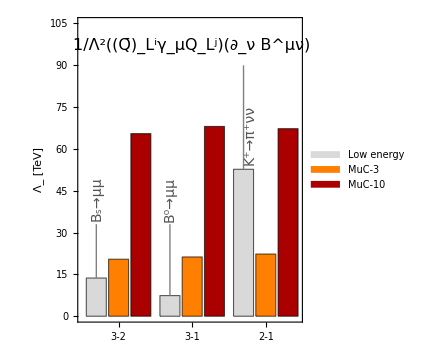

```mathematica
Show[
BarChart[{
Join[{Around[Λ32BsμμNow,{0,Λ32BsμμFuture-Λ32BsμμNow}]},Λ32MuClimits[[1;;2]]],
Join[{Around[Λ31BdμμNow,{0,Λ31BdμμFuture-Λ31BdμμNow}]},Λ31MuClimits[[1;;2]]],
Join[{Around[Λ21KπννNow,{0,Λ21KπννFuture-Λ21KπννNow}]},Λ21MuClimits[[1;;2]]]},(*ChartStyle->{Orange,LightOrange,Lighter[Green],Green,Cyan,LightBlue},*)
(*ChartStyle->"DarkRainbow",*)
ChartStyle->{LightGray,Orange,Darker[Red]},
IntervalMarkersStyle->Gray,
ChartLegends->Placed[{
Style["Low energy",18,Black,FontFamily->"Times"],
Style["MuC-3",18,Black,FontFamily->"Times"],
Style["MuC-10",18,Black,FontFamily->"Times"]},Above],(*BarSpacing->Medium,*)FrameTicks->{Automatic, Automatic},
ChartLabels->{{"3-2","3-1","2-1"},None},
Frame->True,FrameLabel->{None,"Λ_ [TeV]"},ImageSize->320,AspectRatio->1.1,BaseStyle->Directive[16,FontFamily->"Times"],FrameStyle->Directive[Black],PlotRange->{Automatic,{0,105}}],
(**)
Graphics[Text[Style["1/Λ^2((Q̄)_L^iγ_μQ_L^j)(∂_ν B^μν)",16,Black,FontFamily->"Times"],{5.5,97}]],
(**)
Graphics[ Inset[Rotate[Style["B_s→μμ",14,Darker[Gray],FontFamily->"Times"],90Degree],{1.2,42}]],
Graphics[ Inset[Rotate[Style["B^0→μμ",14,Darker[Gray],FontFamily->"Times"],90Degree],{4.5,42}]],
Graphics[ Inset[Rotate[Style["K^+→π^+νν",14,Darker[Gray],FontFamily->"Times"],90Degree],{8.1,65}]]
(**)
]
```

```mathematica
Export["Plot/MuC_flavour_LFU.pdf",%]
```

Plot/MuC_flavour_LFU.pdf

### 1-coefficient bounds - ALL

```mathematica
χSQjjGlobMuC10/.syst->0.2/100/.{SMEFTCoeffListALL[[1]]->cc}/.SMpointSMEFT//Expand
```

(8.16826×10^-28+5.3907×10^-35 ⅈ)-(1.25434×10^-10-1.24749×10^-16 ⅈ) cc+(2.03362×10^7-53.1018 ⅈ) cc^2+$Failed-(1.25434×10^-10+1.49108×10^-16 ⅈ) Conjugate[cc]+(4.06724×10^7+1.12051×10^-13 ⅈ) cc Conjugate[cc]-(3.9341×10^11-601720. ⅈ) cc^2 Conjugate[cc]+(2.03362×10^7+53.1018 ⅈ) Conjugate[cc]^2-(3.9341×10^11+601720. ⅈ) cc Conjugate[cc]^2+(2.07312×10^15+0. ⅈ) cc^2 Conjugate[cc]^2

Make the full table for SMEFT coefficients

```mathematica
Tab2σBoundsSMEFT=Chop[Table[
Block[{χsqtmp},
χsqtmp=Chop[χSQjjGlobMuC10/.syst->0.2/100/.{SMEFTCoeffListALL[[i]]->cc}/.SMpointSMEFT//Expand,10^-15];
{SMEFTCoeffListALL[[i]],cc/.FindRoot[χsqtmp==χSQ1d95,{cc,-10^-4}],cc/.FindRoot[χsqtmp==χSQ1d95,{cc,10^-4}]}
]
,{i,1,Length[SMEFTCoeffListALL]}]];
```

FindRoot::nlnum: The function value {(-2.03388+1.27055×10^-21 ⅈ)+$Failed} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(-3.60752+1.05879×10^-21 ⅈ)+$Failed} is not a list of numbers with dimensions {1} at {cc} = {0.0001}.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(-2.03388+1.27055×10^-21 ⅈ)+$Failed} is not a list of numbers with dimensions {1} at {cc} = {-0.0001}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[χsqtmp==χSQ1d95,{cc,-1/10^4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Tab2σBoundsSMEFT//MatrixForm
```

(Clq1[2,2,1,1] | -0.000205109 | 0.000205109
Clq3[2,2,1,1] | -0.000205109 | 0.000205109
Cqe[1,1,2,2] | -0.000205109 | 0.000205109
Cld[2,2,1,1] | -0.000205109 | 0.000205109
Ced[2,2,1,1] | -0.000205109 | 0.000205109
Cledq[2,2,1,1] | -0.000205109 | 0.000205109
Clu[2,2,1,1] | -0.000205109 | 0.000205109
Ceu[2,2,1,1] | -0.000205109 | 0.000205109
Clequ1[2,2,1,1] | -0.000205109 | 0.000205109
Clequ3[2,2,1,1] | -0.000205109 | 0.000205109
Cledq[2,2,1,2] | -0.000205109 | 0.000205109
Clequ1[2,2,1,2] | -0.000205109 | 0.000205109
Clequ3[2,2,1,2] | -0.000205109 | 0.000205109
Clq1[2,2,2,1] | -0.000205109 | 0.000205109
Clq3[2,2,2,1] | -0.000205109 | 0.000205109
Cqe[2,1,2,2] | -0.000205109 | 0.000205109
Cld[2,2,2,1] | -0.000205109 | 0.000205109
Ced[2,2,2,1] | -0.000205109 | 0.000205109
Cledq[2,2,2,1] | -0.000205109 | 0.000205109
Clu[2,2,2,1] | -0.000205109 | 0.000205109
Ceu[2,2,2,1] | -0.000205109 | 0.000205109
Clequ1[2,2,2,1] | -0.000205109 | 0.000205109
Clequ3[2,2,2,1] | -0.000205109 | 0.000205109
Clq1[2,2,2,2] | -0.000205109 | 0.000205109
Clq3[2,2,2,2] | -0.000205109 | 0.000205109
Cqe[2,2,2,2] | -0.000205109 | 0.000205109
Cld[2,2,2,2] | -0.000205109 | 0.000205109
Ced[2,2,2,2] | -0.000205109 | 0.000205109
Cledq[2,2,2,2] | -0.000205109 | 0.000205109
Clu[2,2,2,2] | -0.000205109 | 0.000205109
Ceu[2,2,2,2] | -0.000205109 | 0.000205109
Clequ1[2,2,2,2] | -0.000205109 | 0.000205109
Clequ3[2,2,2,2] | -0.000205109 | 0.000205109
Clq1[2,2,3,1] | -0.000205109 | 0.000205109
Clq3[2,2,3,1] | -0.000205109 | 0.000205109
Cqe[3,1,2,2] | -0.000205109 | 0.000205109
Cld[2,2,3,1] | -0.000205109 | 0.000205109
Ced[2,2,3,1] | -0.000205109 | 0.000205109
Cledq[2,2,3,1] | -0.000205109 | 0.000205109
Clq1[2,2,3,2] | -0.000205109 | 0.000205109
Clq3[2,2,3,2] | -0.000205109 | 0.000205109
Cqe[3,2,2,2] | -0.000205109 | 0.000205109
Cld[2,2,3,2] | -0.000205109 | 0.000205109
Ced[2,2,3,2] | -0.000205109 | 0.000205109
Cledq[2,2,3,2] | -0.000205109 | 0.000205109
Cledq[2,2,1,3] | -0.000205109 | 0.000205109
Cledq[2,2,2,3] | -0.000205109 | 0.000205109
Clu[2,2,3,1] | -0.000205109 | 0.000205109
Ceu[2,2,3,1] | -0.000205109 | 0.000205109
Clequ1[2,2,3,1] | -0.000205109 | 0.000205109
Clequ3[2,2,3,1] | -0.000205109 | 0.000205109
Clu[2,2,3,2] | -0.000205109 | 0.000205109
Ceu[2,2,3,2] | -0.000205109 | 0.000205109
Clequ1[2,2,3,2] | -0.000205109 | 0.000205109
Clequ3[2,2,3,2] | -0.000205109 | 0.000205109
Clequ1[2,2,1,3] | -0.000205109 | 0.000205109
Clequ3[2,2,1,3] | -0.000205109 | 0.000205109
Clequ1[2,2,2,3] | -0.000205109 | 0.000205109
Clequ3[2,2,2,3] | -0.000205109 | 0.000205109
Clq1[2,2,3,3] | -0.000205109 | 0.000205109
Clq3[2,2,3,3] | -0.000205109 | 0.000205109
Cqe[3,3,2,2] | -0.000205109 | 0.000205109
Cld[2,2,3,3] | -0.000205109 | 0.000205109
Ced[2,2,3,3] | -0.000205109 | 0.000205109
Cledq[2,2,3,3] | -0.000205109 | 0.000205109
Clu[2,2,3,3] | -0.000205109 | 0.000205109
Ceu[2,2,3,3] | -0.000205109 | 0.000205109
Clequ1[2,2,3,3] | -0.000205109 | 0.000205109
Clequ3[2,2,3,3] | -0.000205109 | 0.000205109
CdB[1,1] | -0.000205109 | 0.000205109
CdW[1,1] | -0.000205109 | 0.000205109
CuB[1,1] | -0.000205109 | 0.000205109
CuW[1,1] | -0.000205109 | 0.000205109
CdB[1,2] | -0.000205109 | 0.000205109
CdW[1,2] | -0.000205109 | 0.000205109
CuB[1,2] | -0.000205109 | 0.000205109
CuW[1,2] | -0.000205109 | 0.000205109
CdB[1,3] | -0.000205109 | 0.000205109
CdW[1,3] | -0.000205109 | 0.000205109
CuB[1,3] | -0.000205109 | 0.000205109
CuW[1,3] | -0.000205109 | 0.000205109
CdB[2,1] | -0.000205109 | 0.000205109
CdW[2,1] | -0.000205109 | 0.000205109
CuB[2,1] | -0.000205109 | 0.000205109
CuW[2,1] | -0.000205109 | 0.000205109
CdB[2,2] | -0.000205109 | 0.000205109
CdW[2,2] | -0.000205109 | 0.000205109
CuB[2,2] | -0.000205109 | 0.000205109
CuW[2,2] | -0.000205109 | 0.000205109
CdB[2,3] | -0.000205109 | 0.000205109
CdW[2,3] | -0.000205109 | 0.000205109
CuB[2,3] | -0.000205109 | 0.000205109
CuW[2,3] | -0.000205109 | 0.000205109
CdB[3,1] | -0.000205109 | 0.000205109
CdW[3,1] | -0.000205109 | 0.000205109
CuB[3,1] | -0.000205109 | 0.000205109
CuW[3,1] | -0.000205109 | 0.000205109
CdB[3,2] | -0.000205109 | 0.000205109
CdW[3,2] | -0.000205109 | 0.000205109
CuB[3,2] | -0.000205109 | 0.000205109
CuW[3,2] | -0.000205109 | 0.000205109
CdB[3,3] | -0.000205109 | 0.000205109
CdW[3,3] | -0.000205109 | 0.000205109
CuB[3,3] | -0.000205109 | 0.000205109
CuW[3,3] | -0.000205109 | 0.000205109)

```mathematica
Tab2σBoundsSMEFTprint=Table[
Block[{lowbound,upbound},
lowbound=Tab2σBoundsSMEFT[[i,2]];
upbound=Tab2σBoundsSMEFT[[i,3]];
{SMEFTCoeffListALL[[i]],
"["<>If[lowbound<0,"-","+"]<>"("<>ToString[Round[Abs[lowbound]^(-1/2),0.1]]<>")^-2"<>","<>
If[upbound<0,"-","+"]<>"("<>ToString[Round[Abs[upbound]^(-1/2),0.1]]<>")^-2]"}
]
,{i,1,Length[SMEFTCoeffListALL]}];
Tab2σBoundsSMEFTprint//MatrixForm
```

(Clq1[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[1,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,1,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,1,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,1,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[2,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cqe[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,1,3] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,2,3] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,1,3] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,1,3] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,2,3] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,2,3] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,3,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
CdB[1,1] | [-(69.8)^-2,+(69.8)^-2]
CdW[1,1] | [-(69.8)^-2,+(69.8)^-2]
CuB[1,1] | [-(69.8)^-2,+(69.8)^-2]
CuW[1,1] | [-(69.8)^-2,+(69.8)^-2]
CdB[1,2] | [-(69.8)^-2,+(69.8)^-2]
CdW[1,2] | [-(69.8)^-2,+(69.8)^-2]
CuB[1,2] | [-(69.8)^-2,+(69.8)^-2]
CuW[1,2] | [-(69.8)^-2,+(69.8)^-2]
CdB[1,3] | [-(69.8)^-2,+(69.8)^-2]
CdW[1,3] | [-(69.8)^-2,+(69.8)^-2]
CuB[1,3] | [-(69.8)^-2,+(69.8)^-2]
CuW[1,3] | [-(69.8)^-2,+(69.8)^-2]
CdB[2,1] | [-(69.8)^-2,+(69.8)^-2]
CdW[2,1] | [-(69.8)^-2,+(69.8)^-2]
CuB[2,1] | [-(69.8)^-2,+(69.8)^-2]
CuW[2,1] | [-(69.8)^-2,+(69.8)^-2]
CdB[2,2] | [-(69.8)^-2,+(69.8)^-2]
CdW[2,2] | [-(69.8)^-2,+(69.8)^-2]
CuB[2,2] | [-(69.8)^-2,+(69.8)^-2]
CuW[2,2] | [-(69.8)^-2,+(69.8)^-2]
CdB[2,3] | [-(69.8)^-2,+(69.8)^-2]
CdW[2,3] | [-(69.8)^-2,+(69.8)^-2]
CuB[2,3] | [-(69.8)^-2,+(69.8)^-2]
CuW[2,3] | [-(69.8)^-2,+(69.8)^-2]
CdB[3,1] | [-(69.8)^-2,+(69.8)^-2]
CdW[3,1] | [-(69.8)^-2,+(69.8)^-2]
CuB[3,1] | [-(69.8)^-2,+(69.8)^-2]
CuW[3,1] | [-(69.8)^-2,+(69.8)^-2]
CdB[3,2] | [-(69.8)^-2,+(69.8)^-2]
CdW[3,2] | [-(69.8)^-2,+(69.8)^-2]
CuB[3,2] | [-(69.8)^-2,+(69.8)^-2]
CuW[3,2] | [-(69.8)^-2,+(69.8)^-2]
CdB[3,3] | [-(69.8)^-2,+(69.8)^-2]
CdW[3,3] | [-(69.8)^-2,+(69.8)^-2]
CuB[3,3] | [-(69.8)^-2,+(69.8)^-2]
CuW[3,3] | [-(69.8)^-2,+(69.8)^-2])

```mathematica
{Tab2σBoundsSMEFTprint[[1;;23]]//MatrixForm,Tab2σBoundsSMEFTprint[[24;;47]]//MatrixForm,Tab2σBoundsSMEFTprint[[48;;69]]//MatrixForm}
```

{(Clq1[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[1,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,1,1] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,1,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,1,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,1,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[2,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,2,1] | [-(69.8)^-2,+(69.8)^-2]),(Clq1[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cqe[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,1,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,2,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,1,3] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,2,3] | [-(69.8)^-2,+(69.8)^-2]),(Clu[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,3,1] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,3,2] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,1,3] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,1,3] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,2,3] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,2,3] | [-(69.8)^-2,+(69.8)^-2]
Clq1[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clq3[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Cqe[3,3,2,2] | [-(69.8)^-2,+(69.8)^-2]
Cld[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Ced[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Cledq[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clu[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Ceu[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clequ1[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2]
Clequ3[2,2,3,3] | [-(69.8)^-2,+(69.8)^-2])}

```mathematica
{Tab2σBoundsSMEFTprint[[70;;-1]]//MatrixForm}
```

{(CdB[1,1] | [-(69.8)^-2,+(69.8)^-2]
CdW[1,1] | [-(69.8)^-2,+(69.8)^-2]
CuB[1,1] | [-(69.8)^-2,+(69.8)^-2]
CuW[1,1] | [-(69.8)^-2,+(69.8)^-2]
CdB[1,2] | [-(69.8)^-2,+(69.8)^-2]
CdW[1,2] | [-(69.8)^-2,+(69.8)^-2]
CuB[1,2] | [-(69.8)^-2,+(69.8)^-2]
CuW[1,2] | [-(69.8)^-2,+(69.8)^-2]
CdB[1,3] | [-(69.8)^-2,+(69.8)^-2]
CdW[1,3] | [-(69.8)^-2,+(69.8)^-2]
CuB[1,3] | [-(69.8)^-2,+(69.8)^-2]
CuW[1,3] | [-(69.8)^-2,+(69.8)^-2]
CdB[2,1] | [-(69.8)^-2,+(69.8)^-2]
CdW[2,1] | [-(69.8)^-2,+(69.8)^-2]
CuB[2,1] | [-(69.8)^-2,+(69.8)^-2]
CuW[2,1] | [-(69.8)^-2,+(69.8)^-2]
CdB[2,2] | [-(69.8)^-2,+(69.8)^-2]
CdW[2,2] | [-(69.8)^-2,+(69.8)^-2]
CuB[2,2] | [-(69.8)^-2,+(69.8)^-2]
CuW[2,2] | [-(69.8)^-2,+(69.8)^-2]
CdB[2,3] | [-(69.8)^-2,+(69.8)^-2]
CdW[2,3] | [-(69.8)^-2,+(69.8)^-2]
CuB[2,3] | [-(69.8)^-2,+(69.8)^-2]
CuW[2,3] | [-(69.8)^-2,+(69.8)^-2]
CdB[3,1] | [-(69.8)^-2,+(69.8)^-2]
CdW[3,1] | [-(69.8)^-2,+(69.8)^-2]
CuB[3,1] | [-(69.8)^-2,+(69.8)^-2]
CuW[3,1] | [-(69.8)^-2,+(69.8)^-2]
CdB[3,2] | [-(69.8)^-2,+(69.8)^-2]
CdW[3,2] | [-(69.8)^-2,+(69.8)^-2]
CuB[3,2] | [-(69.8)^-2,+(69.8)^-2]
CuW[3,2] | [-(69.8)^-2,+(69.8)^-2]
CdB[3,3] | [-(69.8)^-2,+(69.8)^-2]
CdW[3,3] | [-(69.8)^-2,+(69.8)^-2]
CuB[3,3] | [-(69.8)^-2,+(69.8)^-2]
CuW[3,3] | [-(69.8)^-2,+(69.8)^-2])}

### 1-coefficient bounds - Marginalised

```mathematica
χSQwork=Chop[χSQjjMuC10SMEFT/.syst->0.2/100//ComplexExpand,10^-10];
```

```mathematica
χSQwork/.{SMEFTCoeffListALL[[1]]->cc}/.SMpointSMEFT//Expand
```

0.+8.13448×10^7 cc^2-7.86819×10^11 cc^3+2.07312×10^15 cc^4

```mathematica
Tab2σBoundsSMEFT[[1]]
```

{Clq1[2,2,1,1],-0.000205109,0.000205109}

Make the full table for SMEFT coefficients

```mathematica
Tab2σBoundsSMEFTmarg={};
```

```mathematica
Czero=Table[0,{i,Length[SMEFTCoeffListALL]-1}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Block[{i,χSQtmp,Clist},
i=1;
χSQtmp=χSQwork/.{SMEFTCoeffListALL[[i]]->cc};
Clist=DeleteCases[SMEFTCoeffListALL,SMEFTCoeffListALL[[i]]];

minTab=Monitor[Table[
FindMinimum[(χSQtmp/.cc->a Tab2σBoundsSMEFT[[i,3]]),Transpose[{Clist,Czero}]][[1]],
{a,-10,10,0.2}],a];
]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

```mathematica
minTab
```

{5487.93,4441.15,3525.32,2733.38,2058.31,1493.21,1031.26,665.649,389.422,195.191,74.4875,15.9846,0.659058,0.0000834719,0.0000878281,0.000116661,0.000142931,0.000153963,0.00015565,0.000119806,0.0000864161,0.0001419,0.000107771,0.000102614,0.000112006,0.0000943321,0.000108649,0.000104047,0.00011229,3.31165×10^-7,3.03856×10^-7,2.33459×10^-7,2.07616×10^-7,1.58239×10^-7,1.27894×10^-7,1.0185×10^-7,9.08498×10^-8,6.37244×10^-8,5.05682×10^-8,3.6369×10^-8,2.53502×10^-8,1.70022×10^-8,1.08672×10^-8,6.53104×10^-9,3.61888×10^-9,1.79355×10^-9,7.55749×10^-10,2.46218×10^-10,7.86056×10^-10,4.80056×10^-11,0.,4.60104×10^-11,7.22132×10^-10,3.59172×10^-9,9.72426×10^-10,2.45569×10^-9,5.26933×10^-9,1.01059×10^-8,1.78542×10^-8,2.96294×10^-8,4.68062×10^-8,7.10577×10^-8,1.044×10^-7,1.49243×10^-7,2.08451×10^-7,2.8541×10^-7,3.84113×10^-7,5.09251×10^-7,6.66328×10^-7,8.61792×10^-7,1.0997×10^-6,1.39409×10^-6,1.72788×10^-6,2.18792×10^-6,2.66469×10^-6,3.34497×10^-6,4.10252×10^-6,5.00852×10^-6,0.000244729,0.00027662,0.000270895,0.000280138,0.000274331,0.000304235,0.000186706,0.000278892,0.000323578,0.000323375,0.000308125,0.000183563,0.000263141,0.000214116,0.00122871,0.0854302,5.09167,40.2403,130.09,288.676,525.479,848.252,1264.12}

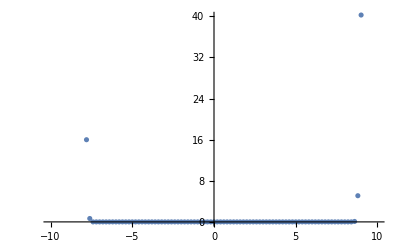

```mathematica
ListPlot[Transpose[{Table[a,{a,-10,10,0.2}],minTab}]]
```

```mathematica
minFunc=Interpolation[Transpose[{Table[a,{a,-10,10,0.2}],minTab}],InterpolationOrder->1]
```

InterpolatingFunction[…]

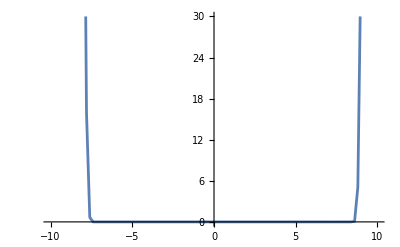

```mathematica
Plot[minFunc[a],{a,-10,10},PlotRange->{0,30}]
```

```mathematica
FindRoot[minFunc[a]==2,{a,-8}]
```

{a→-7.6175}